# Polarized J/ψ production from quark fragmentation in SIDIS

```mathematica
(* This notebook uses the equations in "Polarized TMD fragmentation functions for J/ψ production" to produce the plots shown in the paper *)
```

## Definitions

### MaTeX

```mathematica
(* Matex is a package that formats the plots to the style used in the manuscript *)
```

```mathematica
<<MaTeX`
SetOptions[Plot,AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->12},Frame->True,FrameStyle->Black];
SetOptions[MaTeX,Magnification->1.5];
```

## Constants

```mathematica
(*Defining constants used frequently in the Notebook *)
```

#### Constants

```mathematica
Λ=.200;
nf= 5;
Ca = 3;
Cf = (3^1-1)/(2*3);
```

```mathematica
αsmu[mu_]:= 2Pi/((11-2/3nf)*Log[mu/Λ]);
```

```mathematica
RFF = 1/π^2;
```

```mathematica
NChi = 2/3M*O3S18;
```

```mathematica
O3S18 = .3*10^(-2);
```

```mathematica
Nc =3;
```

## TMDs

### TMD FFs

```mathematica
(*Defining the TMD FFs that will be used to make the plots*)
```

```mathematica
D1 = g^4/(48*Pi*M^4*Nc*z)*(kT^2z^2(z^2-2z+2)+2M^2(z-1)^2)/(kT^2z^2-M^2(z-1))^2*NChi*RFF;
```

```mathematica
D1LL = -g^4/(48*Pi*M^4*Nc*z)*(-kT^2z^2(z^2-2z+2)+4M^2(z-1)^2)/(kT^2z^2-M^2(z-1))^2*NChi*RFF;
```

```mathematica
D1LT = -g^4/(32*Pi*M^2*Nc)*((z-2)(z-1))/(kT^2z^2-M^2(z-1))^2*NChi*RFF;
```

```mathematica
D1TT = -g^4/(16*Pi*M^2*Nc)*(z(z-1))/(kT^2z^2-M^2(z-1))^2*NChi*RFF;
```

```mathematica
G1L = -g^4/(32*Pi*M^4*Nc)*(kT^2z^2(z-2))/(kT^2z^2-M^2(z-1))^2*NChi*RFF;
```

```mathematica
G1Tp = g^4/(16*Pi*M^2*Nc)*(z(z-1))/(kT^2z^2-M^2(z-1))^2*NChi*RFF;
```

```mathematica
G1TT = (g^4 z^3)/(32 π M^4 Nc (M^2 (z-1)-kT^2 z^2)^2)*NChi*RFF;
```

### PDFs

```mathematica
(* PDFs are taken from WW-SIDIS PDF package https://github.com/prokudin/WW-SIDIS - This section defines tables of PDF data taken at the necessary scale for completeness of the notebook *)
```

#### Tables of unpolarized PDFs at Q = 30 GeV

```mathematica
f1udata={{0.001,797.0002487394042},{0.002,343.06537912133473},{0.003,211.67787849824475},{0.004,151.1697550433472},{0.005,116.87356237035604},{0.006,94.9809653844334},{0.007,79.87208122028535},{0.008,68.85715794521347},{0.009000000000000001,60.49170820965949},{0.010000000000000002,53.934220301364775},{0.011,48.662628393527086},{0.012,44.33673820510277},{0.013000000000000001,40.72590885501303},{0.014000000000000002,37.66827697027503},{0.015,35.046988666085795},{0.016,32.77559062465054},{0.017,30.788884808403374},{0.018000000000000002,29.036819984461964},{0.019000000000000003,27.48035564630623},{0.02,26.088606269688526},{0.021,24.8370000812013},{0.022000000000000002,23.70554024162926},{0.023,22.677678561328698},{0.024,21.73976248363305},{0.025,20.880430629098974},{0.026000000000000002,20.090153191942093},{0.027000000000000003,19.360878356124957},{0.028,18.685757330661986},{0.029,18.058928390952715},{0.030000000000000002,17.475345700375648},{0.031,16.93082838850773},{0.032,16.42167178974479},{0.033,15.944442989345855},{0.034,15.496142187114824},{0.035,15.074136547292133},{0.036000000000000004,14.676105775591926},{0.037000000000000005,14.299997076032087},{0.038,13.943987660437632},{0.039,13.606453377916068},{0.04,13.285942333038255},{0.041,12.981337603144969},{0.042,12.69161072938733},{0.043000000000000003,12.415649131210706},{0.044000000000000004,12.152449799430517},{0.045,11.901106122713742},{0.046,11.66079656401321},{0.047,11.430774892081436},{0.048,11.210361725480654},{0.049,10.99893718863181},{0.05,10.795934513548053},{0.051000000000000004,10.600834448634807},{0.052000000000000005,10.413160358597825},{0.053000000000000005,10.232473918091125},{0.054,10.058371317052115},{0.055,9.890479908337504},{0.056,9.728455238789488},{0.057,9.571978413623345},{0.058,9.420753751353752},{0.059000000000000004,9.274506692623365},{0.060000000000000005,9.132981931470633},{0.061,8.996044875575567},{0.062,8.86355459630367},{0.063,8.735273549947252},{0.064,8.61098132745994},{0.065,8.490473137468534},{0.066,8.373558446117062},{0.067,8.260059755358585},{0.068,8.149811503706747},{0.069,8.042659075513038},{0.07,7.938457906600306},{0.07100000000000001,7.837072675602302},{0.07200000000000001,7.738376571670288},{0.07300000000000001,7.642250630341515},{0.074,7.5485831303472075},{0.075,7.457269044990989},{0.076,7.368209542471372},{0.077,7.281311530169224},{0.078,7.196487238486763},{0.079,7.113653840319363},{0.08,7.032733102675335},{0.081,6.9537236761309735},{0.082,6.876616375211908},{0.083,6.801328406365113},{0.084,6.727781922980147},{0.085,6.655903666026565},{0.08600000000000001,6.585624634825682},{0.08700000000000001,6.516879785116039},{0.08800000000000001,6.449607751868057},{0.089,6.383750594565695},{0.09,6.3192535629058195},{0.091,6.256064881072728},{0.092,6.194135548929364},{0.093,6.133419158630646},{0.094,6.073871725310521},{0.095,6.015451530624924},{0.096,5.958118978049567},{0.097,5.901836458935906},{0.098,5.8465682284223455},{0.099,5.792280290381699},{0.1,5.738940290661368},{0.101,5.686574545180549},{0.10200000000000001,5.635204351981073},{0.10300000000000001,5.584792513861383},{0.10400000000000001,5.535303749700415},{0.10500000000000001,5.486704576190558},{0.106,5.438963197899158},{0.107,5.392049405003972},{0.108,5.345934478104672},{0.109,5.300591099563773},{0.11,5.2559932708769015},{0.111,5.21211623561448},{0.112,5.168936407515243},{0.113,5.1264313033467594},{0.114,5.084579480179875},{0.115,5.043360476752749},{0.116,5.002754758626418},{0.117,4.962743666857795},{0.11800000000000001,4.923309369937813},{0.11900000000000001,4.884434818762382},{0.12000000000000001,4.846103704422027},{0.121,4.8083004186127845},{0.122,4.771010016486111},{0.123,4.734218181769609},{0.124,4.697911194003066},{0.125,4.662075897746149},{0.126,4.62674123631358},{0.127,4.591932402711083},{0.128,4.557631658662794},{0.129,4.523822078141845},{0.13,4.490487504257522},{0.131,4.4576125087006115},{0.132,4.425182353579363},{0.133,4.393182955490588},{0.134,4.36160085168143},{0.135,4.330423168167582},{0.136,4.299637589683147},{0.137,4.269232331346077},{0.138,4.239196111931121},{0.139,4.2095181286497105},{0.14,4.180188033343076},{0.14100000000000001,4.151195910001246},{0.14200000000000002,4.122532253526503},{0.14300000000000002,4.094187949665344},{0.14400000000000002,4.066154256038044},{0.14500000000000002,4.038422784199632},{0.146,4.01098548267047},{0.147,3.983834620878631},{0.148,3.956962773960117},{0.149,3.9303628083663344},{0.15,3.904027868231629},{0.151,3.877981702069023},{0.152,3.8522459351587472},{0.153,3.826811031741592},{0.154,3.8016678469513026},{0.155,3.776807608719365},{0.156,3.7522219006033346},{0.157,3.7279026454870454},{0.158,3.7038420901041755},{0.159,3.6800327903396197},{0.16,3.6564675972658454},{0.161,3.6331396438739763},{0.162,3.6100423324617785},{0.163,3.587169322642935},{0.164,3.5645145199441197},{0.165,3.5420720649583437},{0.166,3.5198363230248932},{0.167,3.497801874407887},{0.168,3.4759635049471216},{0.169,3.454316197156372},{0.17,3.4328551217457473},{0.171,3.4115756295460122},{0.17200000000000001,3.3904732438140757},{0.17300000000000001,3.369543652899971},{0.17400000000000002,3.348782703256797},{0.17500000000000002,3.328186392776108},{0.17600000000000002,3.307771912053106},{0.177,3.2875553577382077},{0.178,3.2675313484215978},{0.179,3.247694698580899},{0.18,3.2280404106155602},{0.181,3.208563667236126},{0.182,3.1892598241911263},{0.183,3.17012440331521},{0.184,3.151153085883045},{0.185,3.1323417062542798},{0.186,3.113686245795673},{0.187,3.09518282706719},{0.188,3.0768277082595565},{0.189,3.058617277871413},{0.19,3.040548049614812},{0.191,3.022616657538383},{0.192,3.004819851358022},{0.193,2.987154491985491},{0.194,2.969617547245785},{0.195,2.9522060877745915},{0.196,2.9349172830875867},{0.197,2.9177483978137513},{0.198,2.9006967880852392},{0.199,2.8837598980767316},{0.2,2.8669352566875466},{0.201,2.8502343284841953},{0.202,2.8336680508690204},{0.203,2.817233300737747},{0.20400000000000001,2.8009270548485565},{0.20500000000000002,2.784746386236686},{0.20600000000000002,2.7686884607701114},{0.20700000000000002,2.7527505338402416},{0.20800000000000002,2.7369299471818476},{0.20900000000000002,2.7212241258167116},{0.21,2.705630575115744},{0.211,2.690146877974562},{0.212,2.6747706920977365},{0.213,2.6594997473871587},{0.214,2.644331843430164},{0.215,2.6292648470832636},{0.216,2.6142966901475106},{0.217,2.59942536713172},{0.218,2.5846489330999183},{0.219,2.569965501599573},{0.22,2.555373242667291},{0.221,2.540870380908844},{0.222,2.5264551936504915},{0.223,2.5121260091587314},{0.224,2.4978812049257115},{0.225,2.4837192060176725},{0.226,2.469647361560784},{0.227,2.455672757300846},{0.228,2.4417934987186145},{0.229,2.4280077442567563},{0.23,2.4143137036316404},{0.231,2.4007096362043745},{0.232,2.3871938494088245},{0.233,2.3737646972344324},{0.234,2.360420578761731},{0.23500000000000001,2.347159936748573},{0.23600000000000002,2.3339812562651385},{0.23700000000000002,2.320883063375896},{0.23800000000000002,2.3078639238667256},{0.23900000000000002,2.2949224420155527},{0.24000000000000002,2.282057259404825},{0.241,2.269267053774307},{0.242,2.2565505379126796},{0.243,2.243906458586524},{0.244,2.231333595505302},{0.245,2.2188307603210187},{0.246,2.2063967956612887},{0.247,2.1940305741946093},{0.248,2.1817309977266466},{0.249,2.1694969963264255},{0.25,2.1573275274813355},{0.251,2.145226639705593},{0.252,2.1331983746947114},{0.253,2.121241716932923},{0.254,2.109355673278275},{0.255,2.0975392723557285},{0.256,2.0857915639690123},{0.257,2.074111618530555},{0.258,2.0624985265089104},{0.259,2.050951397893055},{0.26,2.0394693616730013},{0.261,2.0280515653361717},{0.262,2.0166971743789945},{0.263,2.005405371833222},{0.264,1.994175357806475},{0.265,1.9830063490365284},{0.266,1.9718975784589006},{0.267,1.9608482947872878},{0.268,1.9498577621064335},{0.269,1.9389252594770097},{0.27,1.928050080552131},{0.271,1.9172315332051095},{0.272,1.906468939168089},{0.273,1.8957616336812075},{0.274,1.885108965151941},{0.275,1.8745102948243064},{0.276,1.8639673747788863},{0.277,1.8534819826418607},{0.278,1.8430535345972965},{0.279,1.8326814562464266},{0.28,1.8223651824037799},{0.281,1.8121041568986453},{0.28200000000000003,1.8018978323817187},{0.28300000000000003,1.7917456701367722},{0.28400000000000003,1.7816471398971967},{0.28500000000000003,1.771601719667272},{0.28600000000000003,1.761608895548027},{0.28700000000000003,1.7516681615675538},{0.28800000000000003,1.74177901951564},{0.28900000000000003,1.7319409787826023},{0.29,1.7221535562021872},{0.291,1.7124162758984278},{0.292,1.702728669136345},{0.293,1.6930902741763723},{0.294,1.6835006361324008},{0.295,1.6739593068333487},{0.296,1.6644658446881397},{0.297,1.655019814554009},{0.298,1.6456207876080273},{0.299,1.6362683412217651},{0.3,1.6269620588389992},{0.301,1.6177022604845332},{0.302,1.6084893472260549},{0.303,1.5993230297434327},{0.304,1.5902030203090556},{0.305,1.5811290327953298},{0.306,1.5721007826814233},{0.307,1.563117987059282},{0.308,1.554180364638957},{0.309,1.5452876357532623},{0.31,1.5364395223617935},{0.311,1.5276357480543308},{0.312,1.518876038053657},{0.313,1.5101601192178047},{0.314,1.5014877200417656},{0.315,1.492858570658678},{0.316,1.4842724028405196},{0.317,1.4757289499983155},{0.318,1.467227947181894},{0.319,1.4587691310792072},{0.32,1.4503522400152207},{0.321,1.4419770139504127},{0.322,1.433643194478882},{0.323,1.4253505248260905},{0.324,1.4170987498462508},{0.325,1.4088876160193808},{0.326,1.400716419095041},{0.327,1.3925845553167098},{0.328,1.3844919211052367},{0.329,1.3764384102755067},{0.33,1.3684239141388503},{0.331,1.36044832160243},{0.332,1.3525115192656976},{0.333,1.3446133915140066},{0.334,1.3367538206094565},{0.335,1.3289326867790552},{0.336,1.3211498683002785},{0.337,1.3134052415840953},{0.338,1.3056986812555396},{0.339,1.2980300602318922},{0.34,1.2903992497985508},{0.341,1.2828061196826472},{0.342,1.2752505381244772},{0.343,1.267732371946811},{0.34400000000000003,1.2602514866221415},{0.34500000000000003,1.2528077463379286},{0.34600000000000003,1.245401014059901},{0.34700000000000003,1.2380311515934654},{0.34800000000000003,1.2306980196432824},{0.34900000000000003,1.2234014778710602},{0.35000000000000003,1.2161413849516147},{0.35100000000000003,1.2089164017929028},{0.35200000000000004,1.2017252865447705},{0.353,1.194568039661231},{0.354,1.1874446572016162},{0.355,1.1803551309614093},{0.356,1.1732994485996575},{0.357,1.1662775937630618},{0.358,1.1592895462068258},{0.359,1.1523352819123576},{0.36,1.1454147732018987},{0.361,1.1385279888501718},{0.362,1.1316748941931156},{0.363,1.1248554512337934},{0.364,1.1180696187455414},{0.365,1.1113173523724362},{0.366,1.1045986047271479},{0.367,1.0979133254862485},{0.368,1.0912614614830412},{0.369,1.0846429567979783},{0.37,1.0780577528467297},{0.371,1.0715057884659585},{0.372,1.0649869999968702},{0.373,1.0585013213665935},{0.374,1.0520486841674381},{0.375,1.0456290177341008},{0.376,1.0392407187722765},{0.377,1.0328822580203971},{0.378,1.0265536708351424},{0.379,1.0202549881640934},{0.38,1.0139862366639745},{0.381,1.0077474388160297},{0.382,1.0015386130386146},{0.383,0.9953597737970642},{0.384,0.9892109317109071},{0.385,0.9830920936584954},{0.386,0.9770032628791058},{0.387,0.9709444390725847},{0.388,0.9649156184965864},{0.389,0.9589167940614756},{0.39,0.9529479554229384},{0.391,0.9470090890723717},{0.392,0.9411001784250934},{0.393,0.9352212039064338},{0.394,0.9293721430357587},{0.395,0.9235529705084711},{0.396,0.9177636582760461},{0.397,0.9120041756241426},{0.398,0.9062744892488396},{0.399,0.9005745633310435},{0.4,0.8949043596091099},{0.401,0.8892622316386124},{0.402,0.8836465957660826},{0.403,0.8780575030168062},{0.404,0.8724950003510562},{0.405,0.8669591307647093},{0.406,0.8614499333875846},{0.40700000000000003,0.8559674435795578},{0.40800000000000003,0.8505116930245038},{0.40900000000000003,0.8450827098221192},{0.41000000000000003,0.8396805185776682},{0.41100000000000003,0.8343051404897084},{0.41200000000000003,0.8289565934358367},{0.41300000000000003,0.8236348920565026},{0.41400000000000003,0.8183400478369367},{0.41500000000000004,0.8130720691872332},{0.41600000000000004,0.8078309615206299},{0.41700000000000004,0.802616727330032},{0.418,0.7974293662628121},{0.419,0.7922688751939311},{0.42,0.7871352482974187},{0.421,0.7820284771162476},{0.422,0.7769485506306408},{0.423,0.7718954553248456},{0.424,0.7668691752524126},{0.425,0.7618696921000091},{0.426,0.756895250054214},{0.427,0.7519441744599759},{0.428,0.74701656354046},{0.429,0.7421125109834941},{0.43,0.7372321060430307},{0.431,0.7323754336384721},{0.432,0.7275425744519097},{0.433,0.7227336050233173},{0.434,0.7179485978437486},{0.435,0.7131876214465771},{0.436,0.7084507404968265},{0.437,0.7037380158786259},{0.438,0.6990495047808385},{0.439,0.6943852607808957},{0.44,0.6897453339268822},{0.441,0.6851297708179023},{0.442,0.680538614682773},{0.443,0.6759719054570709},{0.444,0.6714296798585769},{0.445,0.6669119714611447},{0.446,0.662418810767035},{0.447,0.6579502252777416},{0.448,0.6535062395633432},{0.449,0.6490868753304174},{0.45,0.6446921514885393},{0.451,0.6403203650334697},{0.452,0.6359698517677533},{0.453,0.6316406840928882},{0.454,0.6273329309249657},{0.455,0.6230466577694832},{0.456,0.618781926794662},{0.457,0.6145387969032965},{0.458,0.6103173238031652},{0.459,0.6061175600760353},{0.46,0.6019395552452901},{0.461,0.5977833558422055},{0.462,0.5936490054709033},{0.463,0.5895365448720121},{0.464,0.5854460119850593},{0.465,0.5813774420096182},{0.466,0.5773308674652423},{0.467,0.5733063182502042},{0.468,0.5693038216990696},{0.46900000000000003,0.5653234026391252},{0.47000000000000003,0.5613650834456879},{0.47100000000000003,0.5574288840963152},{0.47200000000000003,0.5535148222239408},{0.47300000000000003,0.5496229131689558},{0.47400000000000003,0.5457531700302598},{0.47500000000000003,0.5419056037152974},{0.47600000000000003,0.5380786794235756},{0.47700000000000004,0.5342709028678246},{0.47800000000000004,0.5304823418344483},{0.47900000000000004,0.5267130611234494},{0.48000000000000004,0.5229631226091381},{0.481,0.5192325852996884},{0.482,0.5155215053955611},{0.483,0.511829936346821},{0.484,0.508157928909366},{0.485,0.5045055312000888},{0.486,0.5008727887509963},{0.487,0.4972597445623038},{0.488,0.4936664391545239},{0.489,0.4900929106195714},{0.49,0.4865391946709028},{0.491,0.4830053246927078},{0.492,0.4794913317881738},{0.493,0.47599724482683864},{0.494,0.4725230904910511},{0.495,0.4690688933215561},{0.496,0.46563467576222034},{0.497,0.46222045820391705},{0.498,0.45882625902758406},{0.499,0.4554520946464718},{0.5,0.4520979795475991},{0.501,0.44876249216350855},{0.502,0.44544424637511554},{0.503,0.4421433064520407},{0.504,0.43885973407805},{0.505,0.4355935884009141},{0.506,0.43234492608136454},{0.507,0.4291138013411668},{0.508,0.4259002660103266},{0.509,0.4227043695734444},{0.51,0.41952615921523373},{0.511,0.4163656798652217},{0.512,0.41322297424164317},{0.513,0.41009808289454613},{0.514,0.40699104424812155},{0.515,0.4039018946422745},{0.516,0.400830668373445},{0.517,0.39777739773470033},{0.518,0.39474211305510565},{0.519,0.39172484273838887},{0.52,0.38872561330091315},{0.521,0.3857444494089701},{0.522,0.38278137391540223},{0.523,0.37983640789557405},{0.524,0.37690957068269615},{0.525,0.3740008799025206},{0.526,0.37110910147399445},{0.527,0.3682330169793083},{0.528,0.3653726648783859},{0.529,0.3625280817918727},{0.53,0.3596993025358663},{0.531,0.35688636015604086},{0.532,0.3540892859611793},{0.533,0.3513081095561216},{0.534,0.34854285887414044},{0.535,0.3457935602087547},{0.536,0.3430602382449896},{0.537,0.34034291609009504},{0.538,0.3376416153037313},{0.539,0.3349563559276305},{0.54,0.33228715651474466},{0.541,0.3296340341578879},{0.542,0.32699700451788344},{0.543,0.3243760818512234},{0.544,0.3217712790372495},{0.545,0.31918260760486317},{0.546,0.31661007775877514},{0.547,0.3140536984053009},{0.548,0.311513477177709},{0.549,0.30898942046113426},{0.55,0.30648153341705775},{0.551,0.3039887116264682},{0.552,0.30150987905813786},{0.553,0.2990450812259109},{0.554,0.2965943619006223},{0.555,0.2941577631409931},{0.556,0.29173532532401114},{0.557,0.2893270871748119},{0.558,0.28693308579606636},{0.559,0.2845533566968816},{0.56,0.28218793382122687},{0.561,0.27983684957588967},{0.562,0.27750013485797187},{0.5630000000000001,0.2751778190819321},{0.5640000000000001,0.2728699302061843},{0.5650000000000001,0.2705764947592571},{0.5660000000000001,0.2682975378655237},{0.5670000000000001,0.2660330832705093},{0.5680000000000001,0.26378315336578173},{0.5690000000000001,0.2615477692134336},{0.5700000000000001,0.2593269505701632},{0.5710000000000001,0.25712071591095886},{0.5720000000000001,0.2549290824523963},{0.5730000000000001,0.252752066175553},{0.5740000000000001,0.25058968184854763},{0.5750000000000001,0.24844194304870934},{0.5760000000000001,0.24630783239662773},{0.5770000000000001,0.24418635007304393},{0.578,0.24207753402563534},{0.579,0.23998142076869283},{0.58,0.23789804540757412},{0.581,0.23582744166276665},{0.582,0.2337696418935712},{0.583,0.23172467712140776},{0.584,0.2296925770527538},{0.585,0.2276733701017194},{0.586,0.22566708341226302},{0.587,0.2236737428800589},{0.588,0.22169337317401577},{0.589,0.2197259977574577},{0.59,0.21777163890896845},{0.591,0.21583031774290823},{0.592,0.21390205422960576},{0.593,0.2119868672152319},{0.594,0.21008477444135978},{0.595,0.20819579256421702},{0.596,0.20631993717363403},{0.597,0.204457222811694},{0.598,0.20260766299108945},{0.599,0.20077127021318947},{0.6,0.1989480559858231},{0.601,0.19713721599234701},{0.602,0.1953379424347767},{0.603,0.19355024029147808},{0.604,0.19177411378797224},{0.605,0.19000956641040925},{0.606,0.18825660091882976},{0.607,0.1865152193602184},{0.608,0.18478542308135146},{0.609,0.18306721274144275},{0.61,0.1813605883245912},{0.611,0.17966554915203256},{0.612,0.17798209389419814},{0.613,0.17631022058258508},{0.614,0.17464992662143974},{0.615,0.17300120879925762},{0.616,0.17136406330010295},{0.617,0.1697384857147506},{0.618,0.16812447105165307},{0.619,0.16652201374773545},{0.62,0.16493110767902097},{0.621,0.16335174617109013},{0.622,0.16178392200937533},{0.623,0.16022762744929467},{0.624,0.158682854226226},{0.625,0.15714959356532532},{0.626,0.15562718655971838},{0.627,0.1541149876970592},{0.628,0.15261300737079683},{0.629,0.15112125525525874},{0.63,0.1496397403176746},{0.631,0.14816847083002005},{0.632,0.1467074543806828},{0.633,0.1452566978859551},{0.634,0.14381620760135352},{0.635,0.14238598913276945},{0.636,0.14096604744745334},{0.637,0.1395563868848345},{0.638,0.13815701116717904},{0.639,0.13676792341008898},{0.64,0.1353891261328444},{0.641,0.13402062126859107},{0.642,0.13266241017437594},{0.643,0.1313144936410334},{0.644,0.12997687190292304},{0.645,0.12864954464752332},{0.646,0.1273325110248812},{0.647,0.12602576965692108},{0.648,0.12472931864661557},{0.649,0.12344315558701846},{0.65,0.12216727757016406},{0.651,0.12090115126794905},{0.652,0.11964423967176105},{0.653,0.1183965337289377},{0.654,0.11715802405395503},{0.655,0.115928700934672},{0.656,0.11470855433848018},{0.657,0.1134975739183605},{0.658,0.11229574901884773},{0.659,0.11110306868190557},{0.66,0.10991952165271135},{0.661,0.10874509638535428},{0.662,0.10757978104844643},{0.663,0.10642356353064909},{0.664,0.10527643144611525},{0.665,0.10413837213984956},{0.666,0.10300937269298674},{0.667,0.10188941992799021},{0.668,0.10077850041377158},{0.669,0.09967660047073287},{0.67,0.09858370617573137},{0.671,0.09749980336697009},{0.672,0.09642487764881304},{0.673,0.09535891439652813},{0.674,0.09430189876095724},{0.675,0.09325381567311584},{0.676,0.09221426388119201},{0.677,0.09118284407721225},{0.678,0.09015954378738125},{0.679,0.08914435033003759},{0.68,0.08813725081980765},{0.681,0.08713823217169708},{0.682,0.08614728110512057},{0.683,0.08516438414787143},{0.684,0.08418952764003114},{0.685,0.08322269773782037},{0.686,0.0822638804173919},{0.687,0.08131306147856669},{0.6880000000000001,0.08037022654851325},{0.6890000000000001,0.07943536108537226},{0.6900000000000001,0.07850845038182591},{0.6910000000000001,0.07758947956861383},{0.6920000000000001,0.07667843361799606},{0.6930000000000001,0.07577529734716353},{0.6940000000000001,0.07488005542159722},{0.6950000000000001,0.07399269235837651},{0.6960000000000001,0.07311319252943768},{0.6970000000000001,0.07224154016478312},{0.6980000000000001,0.07137771935564191},{0.6990000000000001,0.07052171405758272},{0.7000000000000001,0.06967350809357929},{0.7010000000000001,0.06883281926067215},{0.7020000000000001,0.06799935913482531},{0.7030000000000001,0.06717310213507602},{0.7040000000000001,0.06635402271490387},{0.705,0.06554209536308925},{0.706,0.06473729460455299},{0.707,0.06393959500117913},{0.708,0.06314897115261914},{0.709,0.06236539769707938},{0.71,0.06158884931209128},{0.711,0.060819300715264715},{0.712,0.060056726665025324},{0.713,0.05930110196133496},{0.714,0.058552401446396826},{0.715,0.05781060000534442},{0.716,0.05707567256691544},{0.717,0.05634759410411025},{0.718,0.05562633963483559},{0.719,0.05491188422253344},{0.72,0.054204202976795596},{0.721,0.05350327105396399},{0.722,0.05280906365771701},{0.723,0.052121556039642025},{0.724,0.051440723499794616},{0.725,0.05076654138724422},{0.726,0.05009884888564096},{0.727,0.04943747960736678},{0.728,0.04878240071611656},{0.729,0.0481335795540011},{0.73,0.04749098364049598},{0.731,0.04685458067139694},{0.732,0.04622433851778093},{0.733,0.04560022522497456},{0.734,0.04498220901152791},{0.735,0.0443702582681952},{0.736,0.04376434155692148},{0.737,0.04316442760983551},{0.738,0.042570485328248975},{0.739,0.04198248378166168},{0.74,0.041400392206772864},{0.741,0.04082418000649871},{0.742,0.04025381674899565},{0.743,0.03968927216669007},{0.744,0.039130516155313454},{0.745,0.03857751877294397},{0.746,0.03803025023905353},{0.747,0.037488680933561086},{0.748,0.03695278139589139},{0.749,0.03642252232403994},{0.75,0.03589787457364329},{0.751,0.03537877630394445},{0.752,0.034865158618870455},{0.753,0.03435698213462046},{0.754,0.03385420776648731},{0.755,0.033356796726311394},{0.756,0.03286471051995876},{0.757,0.03237791094482369},{0.758,0.031896360087354886},{0.759,0.031420020320605535},{0.76,0.030948854301806647},{0.761,0.030482824969963622},{0.762,0.030021895543475754},{0.763,0.02956602951777822},{0.764,0.02911519066300678},{0.765,0.028669343021684394},{0.766,0.028228450906429902},{0.767,0.02779247889768841},{0.768,0.0273613918414832},{0.769,0.026935154847188836},{0.77,0.026513733285325275},{0.771,0.026097092785372818},{0.772,0.02568519923360774},{0.773,0.02527801877095814},{0.774,0.02487551779088004},{0.775,0.02447766293725333},{0.776,0.02408448490349713},{0.777,0.023696005774058993},{0.778,0.02331217977280199},{0.779,0.022932961529710534},{0.78,0.022558306077116043},{0.781,0.022188168845960678},{0.782,0.021822505662098913},{0.783,0.021461272742636327},{0.784,0.02110442669230548},{0.785,0.02075192449987807},{0.786,0.02040372353461346},{0.787,0.02005978154274263},{0.788,0.019720056643987672},{0.789,0.01938450732811607},{0.79,0.019053092451529578},{0.791,0.01872577123388723},{0.792,0.018402503254762163},{0.793,0.018083248450331792},{0.794,0.017767967110101094},{0.795,0.017456619873658576},{0.796,0.017149167727464512},{0.797,0.016845572001671208},{0.798,0.016545794366974887},{0.799,0.01624979683149881},{0.8,0.015957541737707397},{0.801,0.01566913308336151},{0.802,0.015384667507253813},{0.803,0.015104096905226782},{0.804,0.014827373626879964},{0.805,0.014554450471284836},{0.806,0.014285280682742969},{0.807,0.014019817946586832},{0.808,0.01375801638502305},{0.809,0.013499830553017325},{0.81,0.013245215434220829},{0.811,0.012994126436937486},{0.812,0.01274651939013173},{0.8130000000000001,0.012502350539476268},{0.8140000000000001,0.012261576543439482},{0.8150000000000001,0.01202415446941195},{0.8160000000000001,0.011790041789871725},{0.8170000000000001,0.011559196378587926},{0.8180000000000001,0.011331576506862237},{0.8190000000000001,0.011107140839807895},{0.8200000000000001,0.010885848432665728},{0.8210000000000001,0.010667658727156934},{0.8220000000000001,0.010452531547872079},{0.8230000000000001,0.010240427098696056},{0.8240000000000001,0.010031305959268521},{0.8250000000000001,0.00982512908147941},{0.8260000000000001,0.009622067585565126},{0.8270000000000001,0.009422282830901497},{0.8280000000000001,0.009225721802162114},{0.8290000000000001,0.009032332009292304},{0.8300000000000001,0.008842061482520591},{0.8310000000000001,0.008654858767420016},{0.8320000000000001,0.008470672920018752},{0.8330000000000001,0.008289453501959528},{0.834,0.008111150575707271},{0.835,0.007935714699804428},{0.836,0.007763096924173676},{0.837,0.007593248785467182},{0.838,0.007426122302462107},{0.839,0.007261669971501889},{0.84,0.007099844761982687},{0.841,0.006940600111884586},{0.842,0.00678388992334709},{0.843,0.006629668558288371},{0.844,0.006477890834067875},{0.845,0.006328512019191746},{0.846,0.006181487829060705},{0.847,0.006036774421759867},{0.848,0.00589432839389005},{0.849,0.005754106776440165},{0.85,0.005616067030700236},{0.851,0.005480423150452655},{0.852,0.005347383389600452},{0.853,0.005216897301048306},{0.854,0.005088914942075661},{0.855,0.004963386869610879},{0.856,0.004840264135551676},{0.857,0.004719498282131276},{0.858,0.004601041337329912},{0.859,0.004484845810331089},{0.86,0.004370864687022201},{0.861,0.004259051425539022},{0.862,0.004149359951853607},{0.863,0.004041744655405157},{0.864,0.003936160384773371},{0.865,0.003832562443393889},{0.866,0.003730906585315346},{0.867,0.00363114901099761},{0.868,0.0035332463631507897},{0.869,0.003437155722614569},{0.87,0.0033428346042774643},{0.871,0.00325024095303557},{0.872,0.003159333139790406},{0.873,0.003070069957485441},{0.874,0.0029824106171809036},{0.875,0.0028963147441664586},{0.876,0.0028120283118056046},{0.877,0.002729789079218209},{0.878,0.0026495450567020525},{0.879,0.0025712447813090494},{0.88,0.0024948373119687657},{0.881,0.002420272224658755},{0.882,0.0023474996076211963},{0.883,0.002276470056625375},{0.884,0.0022071346702755472},{0.885,0.002139445045363679},{0.886,0.002073353272266654},{0.887,0.0020088119303874547},{0.888,0.0019457740836398873},{0.889,0.0018841932759763864},{0.89,0.001824023526958484},{0.891,0.0017652193273694817},{0.892,0.0017077356348689152},{0.893,0.0016515278696883655},{0.894,0.0015965519103682208},{0.895,0.0015427640895349435},{0.896,0.0014901211897184548},{0.897,0.0014385804392092094},{0.898,0.001388099507954579},{0.899,0.0013386365034941212},{0.9,0.0012901499669333545},{0.901,0.001242902353629073},{0.902,0.0011971517571029492},{0.903,0.0011528508598413834},{0.904,0.0011099528226325562},{0.905,0.0010684112802183893},{0.906,0.0010281803369872773},{0.907,0.0009892145627072105},{0.908,0.000951468988298866},{0.909,0.000914899101648272},{0.91,0.0008794608434586506},{0.911,0.0008451106031410425},{0.912,0.0008118052147433303},{0.913,0.0007795019529172735},{0.914,0.0007481585289231736},{0.915,0.0007177330866718019},{0.916,0.0006881841988032098},{0.917,0.0006594708628020578},{0.918,0.0006315524971491007},{0.919,0.0006043889375084672},{0.92,0.0005779404329503815},{0.921,0.000552167642208969},{0.922,0.0005270316299748055},{0.923,0.00050249386322186},{0.924,0.0004785162075684898},{0.925,0.0004550609236721614},{0.926,0.0004323786023357571},{0.927,0.00041071714669267575},{0.928,0.0003900353925492176},{0.929,0.0003702925894311174},{0.93,0.0003514483968942758},{0.931,0.0003334628808693172},{0.932,0.0003162965100396344},{0.933,0.00029991015225259765},{0.934,0.0002842650709636016},{0.935,0.0002693229217126295},{0.936,0.00025504574863301704},{0.937,0.00024139598099209982},{0.9380000000000001,0.0002283364297634374},{0.9390000000000001,0.00021583028423030162},{0.9400000000000001,0.00020384110862012861},{0.9410000000000001,0.00019233283876962952},{0.9420000000000001,0.00018126977882026605},{0.9430000000000001,0.0001706165979437917},{0.9440000000000001,0.00016033832709756943},{0.9450000000000001,0.0001504003558093768},{0.9460000000000001,0.0001407684289914103},{0.9470000000000001,0.00013140864378321062},{0.9480000000000001,0.00012228744642322388},{0.9490000000000001,0.0001133716291487257},{0.9500000000000001,0.00010462832712383228},{0.9510000000000001,0.00009627559772737508},{0.9520000000000001,0.00008853170803514231},{0.9530000000000001,0.00008136460423879755},{0.9540000000000001,0.00007474255176960103},{0.9550000000000001,0.00006863413250849155},{0.9560000000000001,0.00006300824202115894},{0.9570000000000001,0.00005783408681786957},{0.9580000000000001,0.000053081181637807865},{0.9590000000000001,0.00004871934675769921},{0.9600000000000001,0.00004471870532448352},{0.961,0.00004104968071180969},{0.962,0.00003768299390012198},{0.963,0.00003458966088011995},{0.964,0.000031740990079360935},{0.965,0.000029108579811791684},{0.966,0.000026664315749988778},{0.967,0.0000243803684198926},{0.968,0.000022229190717821744},{0.969,0.000020183515449556284},{0.97,0.000018216352891281633},{0.971,0.000016300988372185402},{0.972,0.00001441097987850298},{0.973,0.000012520155678809146},{0.974,0.000010602611970354745},{0.975,8.632710546250601*^-6},{0.976,6.697769219381096*^-6},{0.977,4.901506018648497*^-6},{0.978,3.2430846026517823*^-6},{0.979,1.7216735824846458*^-6},{0.98,3.364464893578102*^-7},{0.981,-9.134182575409792*^-7},{0.982,-2.0287373829511943*^-6},{0.983,-3.0103227872099993*^-6},{0.984,-3.8589815776908005*^-6},{0.985,-4.575516100011826*^-6},{0.986,-5.160723969016633*^-6},{0.987,-5.61539809952831*^-6},{0.988,-5.940326736879373*^-6},{0.989,-6.1362934872190535*^-6},{0.99,-6.20407734759989*^-6},{0.991,-6.14445273584534*^-6},{0.992,-5.958189520200285*^-6},{0.993,-5.646053048766113*^-6},{0.994,-5.208804178722185*^-6},{0.995,-4.647199305335429*^-6},{0.996,-3.9619903907596535*^-6},{0.997,-3.1539249926265537*^-6},{0.998,-2.2237462924297453*^-6},{0.999,-1.1721931237038466*^-6}};
```

```mathematica
f1ddata ={{0.001,764.9243472367359},{0.002,325.1477629389879},{0.003,198.93667248045236},{0.004,141.08875386672992},{0.005,108.41516994814492},{0.006,87.60437636499893},{0.007,73.26097051200664},{0.008,62.815224115717164},{0.009000000000000001,54.88802654174627},{0.010000000000000002,48.676736309922475},{0.011,43.68537255452042},{0.012,39.59269853341543},{0.013000000000000001,36.17667755889261},{0.014000000000000002,33.28257970445242},{0.015,30.802108200883943},{0.016,28.654877961196597},{0.017,26.77788681567602},{0.018000000000000002,25.123033726828254},{0.019000000000000003,23.652974004066174},{0.02,22.338280612828022},{0.021,21.156465915193543},{0.022000000000000002,20.089253635846855},{0.023,19.120760684018205},{0.024,18.237901206298396},{0.025,17.429798776192975},{0.026000000000000002,16.687340377533573},{0.027000000000000003,16.002833926618514},{0.028,15.369742408463267},{0.029,14.782475399856573},{0.030000000000000002,14.23622406378994},{0.031,13.727096617980852},{0.032,13.251666528561799},{0.033,12.806675863683086},{0.034,12.38927364042965},{0.035,11.996954349531851},{0.036000000000000004,11.627507265178707},{0.037000000000000005,11.278974401549972},{0.038,10.949615447596381},{0.039,10.637878368720257},{0.04,10.342374637577656},{0.041,10.06199691361747},{0.042,9.795735375941513},{0.043000000000000003,9.542541679830554},{0.044000000000000004,9.301468894110391},{0.045,9.07165955211427},{0.046,8.852335348210069},{0.047,8.642788222255662},{0.048,8.442372619301402},{0.049,8.250498748201153},{0.05,8.06662669231353},{0.051000000000000004,7.890261249563749},{0.052000000000000005,7.720947398879211},{0.053000000000000005,7.558266306260939},{0.054,7.40183179718036},{0.055,7.251287233129541},{0.056,7.106302739427634},{0.057,6.9665727391361},{0.058,6.83181375443358},{0.059000000000000004,6.701762442268107},{0.060000000000000005,6.576173835718038},{0.061,6.454894554380731},{0.062,6.337769580912083},{0.063,6.2245770136932475},{0.064,6.115110690711662},{0.065,6.00917882309384},{0.066,5.906602767374828},{0.067,5.807215920494185},{0.068,5.7108627235677805},{0.069,5.617397762252897},{0.07,5.5266849530461215},{0.07100000000000001,5.438596806166366},{0.07200000000000001,5.35301375681043},{0.07300000000000001,5.269823557551945},{0.074,5.188920725508388},{0.075,5.110206038643717},{0.076,5.033586076221653},{0.077,4.9589727989902155},{0.078,4.886283165173005},{0.079,4.815438778776421},{0.08,4.746365567103078},{0.081,4.679048155618425},{0.082,4.613466065031478},{0.083,4.549544116178623},{0.084,4.487211513705413},{0.085,4.4264015351742545},{0.08600000000000001,4.367051245731777},{0.08700000000000001,4.309101235963968},{0.08800000000000001,4.252495380811305},{0.089,4.197180617632839},{0.09,4.143106741700592},{0.091,4.090226217576928},{0.092,4.0384940049800075},{0.093,3.9878673978785653},{0.094,3.9383058756786937},{0.095,3.8897709654739616},{0.096,3.842226114427458},{0.097,3.7956365714415394},{0.098,3.749969277349211},{0.099,3.7051927629314223},{0.1,3.661277054127687},{0.101,3.6182326736737753},{0.10200000000000001,3.5760675970164133},{0.10300000000000001,3.5347503049550055},{0.10400000000000001,3.4942508120783544},{0.10500000000000001,3.454540576255429},{0.106,3.4155924142944256},{0.107,3.3773804232968345},{0.108,3.3398799072734713},{0.109,3.3030673086258826},{0.11,3.2669201441297053},{0.111,3.2314169450866013},{0.112,3.1965372013387974},{0.113,3.16226130886512},{0.114,3.1285705207001255},{0.115,3.0954469009385868},{0.116,3.062873281606472},{0.117,3.0308332221967555},{0.11800000000000001,2.9993109716841664},{0.11900000000000001,2.968291432847339},{0.12000000000000001,2.9377601287400292},{0.121,2.907703171165106},{0.122,2.878107231016072},{0.123,2.848959510361051},{0.124,2.820247716153402},{0.125,2.791960035461771},{0.126,2.7641082610060503},{0.127,2.7367027040430996},{0.128,2.709730097610556},{0.129,2.683177715392745},{0.13,2.657033345147217},{0.131,2.631285263631053},{0.132,2.6059222129320134},{0.133,2.580933378116228},{0.134,2.5563083661102737},{0.135,2.532037185741161},{0.136,2.5081102288629635},{0.137,2.484518252503708},{0.138,2.4612523619706055},{0.139,2.438303994855852},{0.14,2.4156649058891166},{0.14100000000000001,2.393327152586352},{0.14200000000000002,2.3712830816479156},{0.14300000000000002,2.3495253160620297},{0.14400000000000002,2.3280467428724956},{0.14500000000000002,2.3068405015721862},{0.146,2.285899973086348},{0.147,2.265218769311991},{0.148,2.2447907231818123},{0.149,2.224609879223065},{0.15,2.204670484583623},{0.151,2.1849796222167885},{0.152,2.1655439251769577},{0.153,2.1463572714801478},{0.154,2.1274137440529706},{0.155,2.1087076223610266},{0.156,2.090233374432589},{0.157,2.071985649256548},{0.158,2.0539592695348445},{0.159,2.0361492247707886},{0.16,2.0185506646757196},{0.161,2.0011588928775},{0.162,1.9839693609152693},{0.163,1.9669776625057858},{0.164,1.9501795280675083},{0.165,1.9335708194893613},{0.166,1.9171475251318544},{0.167,1.900905755048921},{0.168,1.8848417364194772},{0.169,1.8689518091783273},{0.17,1.853232421836589},{0.171,1.8376801274823744},{0.17200000000000001,1.8222915799529362},{0.17300000000000001,1.807063530169991},{0.17400000000000002,1.791992822630364},{0.17500000000000002,1.7770763920445072},{0.17600000000000002,1.7623173205700398},{0.177,1.7477186148899297},{0.178,1.733277225367733},{0.179,1.7189901842928497},{0.18,1.7048546031305185},{0.181,1.6908676698803582},{0.182,1.6770266465385701},{0.183,1.6633288666591795},{0.184,1.6497717330099004},{0.185,1.6363527153184565},{0.186,1.623069348105366},{0.187,1.6099192285994237},{0.188,1.596900014732272},{0.189,1.584009423208645},{0.19,1.5712452276490276},{0.191,1.558605256801633},{0.192,1.5460873928207386},{0.193,1.533689569608577},{0.194,1.5214097712181054},{0.195,1.50924603031409},{0.196,1.4971964266900888},{0.197,1.4852590858390011},{0.198,1.4734321775749784},{0.199,1.4617139147045894},{0.2,1.4501025517452204},{0.201,1.4385988146749296},{0.202,1.4272034849446766},{0.203,1.4159149561403956},{0.20400000000000001,1.4047316548985962},{0.20500000000000002,1.393652040039449},{0.20600000000000002,1.382674601727313},{0.20700000000000002,1.3717978606576948},{0.20800000000000002,1.3610203672696717},{0.20900000000000002,1.350340700982842},{0.21,1.3397574694579268},{0.211,1.3292693078801536},{0.212,1.318874878264621},{0.213,1.30857286878284},{0.214,1.2983619931097181},{0.215,1.2882409897902483},{0.216,1.2782086216252173},{0.217,1.2682636750752665},{0.218,1.2584049596826623},{0.219,1.2486313075101683},{0.22,1.238941572596421},{0.221,1.229334630427252},{0.222,1.2198093774224041},{0.223,1.2103647304371217},{0.224,1.2009996262781129},{0.225,1.191713021233397},{0.226,1.182504363866939},{0.227,1.1733732001277213},{0.228,1.1643186560446728},{0.229,1.155339869921391},{0.23,1.146435992136162},{0.231,1.1376061849454637},{0.232,1.1288496222908957},{0.233,1.120165489609479},{0.234,1.1115529836472784},{0.23500000000000001,1.103011312276282},{0.23600000000000002,1.094539694314493},{0.23700000000000002,1.0861373593491828},{0.23800000000000002,1.077803547563238},{0.23900000000000002,1.0695375095645676},{0.24000000000000002,1.0613385062185046},{0.241,1.0532058084831577},{0.242,1.045138697247659},{0.243,1.0371364631732598},{0.244,1.0291984065372246},{0.245,1.0213238370794717},{0.246,1.013512073851914},{0.247,1.0057624450704534},{0.248,0.9980742879695816},{0.249,0.990446948659536},{0.25,0.9828797819859707},{0.251,0.975371731538208},{0.252,0.9679218133158344},{0.253,0.960529500883706},{0.254,0.9531942726386913},{0.255,0.9459156117898317},{0.256,0.9386930063371509},{0.257,0.9315259490491998},{0.258,0.9244139374394199},{0.259,0.9173564737414046},{0.26,0.9103530648831313},{0.261,0.9034032224602351},{0.262,0.8965064627083907},{0.263,0.8896623064748703},{0.264,0.8828702791893333},{0.265,0.8761299108339089},{0.266,0.8694407359126247},{0.267,0.8628022934202362},{0.268,0.856214126810503},{0.269,0.8496757839639637},{0.27,0.8431868171552477},{0.271,0.8367467830199748},{0.272,0.8303552425212752},{0.273,0.8240117609159728},{0.274,0.8177159077204678},{0.275,0.8114672566763508},{0.276,0.8052643009908804},{0.277,0.7991056654571651},{0.278,0.7929911228081109},{0.279,0.7869204438450992},{0.28,0.7808933975782947},{0.281,0.7749097513615696},{0.28200000000000003,0.7689692710222424},{0.28300000000000003,0.7630717209858132},{0.28400000000000003,0.7572168643958818},{0.28500000000000003,0.7514044632294156},{0.28600000000000003,0.7456342784075379},{0.28700000000000003,0.7399060699019965},{0.28800000000000003,0.7342195968374648},{0.28900000000000003,0.728574617589832},{0.29,0.7229708898806135},{0.291,0.7174081708676332},{0.292,0.7118862172321039},{0.293,0.7064047852622352},{0.294,0.7009636309334906},{0.295,0.6955625099856223},{0.296,0.6902011779965858},{0.297,0.6848793904534559},{0.298,0.6795969028204454},{0.299,0.6743534706041316},{0.3,0.6691488494159898},{0.301,0.6639814533784001},{0.302,0.6588497508720678},{0.303,0.6537535777718585},{0.304,0.648692768380264},{0.305,0.6436671555240173},{0.306,0.6386765706473346},{0.307,0.6337208439018954},{0.308,0.6287998042336723},{0.309,0.6239132794667096},{0.31,0.6190610963839539},{0.311,0.6142430808052325},{0.312,0.6094590576624762},{0.313,0.6047088510722703},{0.314,0.5999922844058313},{0.315,0.5953091803564836},{0.316,0.5906593610047267},{0.317,0.5860426478809657},{0.318,0.5814588620259827},{0.319,0.5769078240492294},{0.32,0.5723893541849995},{0.321,0.5679032723465636},{0.322,0.5634493981783235},{0.323,0.5590275511060554},{0.324,0.5546375503853027},{0.325,0.5502792151479788},{0.326,0.5459510054857237},{0.327,0.5416514647912964},{0.328,0.5373805347130487},{0.329,0.5331381538327088},{0.33,0.5289242577785876},{0.331,0.5247387793354407},{0.332,0.5205816485510818},{0.333,0.5164527928398482},{0.334,0.512352137083005},{0.335,0.5082796037261818},{0.336,0.5042351128739279},{0.337,0.5002185823814691},{0.338,0.49622992794374954},{0.339,0.4922690631818358},{0.34,0.48833589972676306},{0.341,0.4844303473008942},{0.342,0.4805523137968666},{0.343,0.47670170535419587},{0.34400000000000003,0.4728784264336039},{0.34500000000000003,0.469082379889139},{0.34600000000000003,0.46531346703814874},{0.34700000000000003,0.4615715877291706},{0.34800000000000003,0.45785664040779855},{0.34900000000000003,0.45416852218058534},{0.35000000000000003,0.4505071288770351},{0.35100000000000003,0.44687085906351465},{0.35200000000000004,0.4432581836496432},{0.353,0.43966910335125287},{0.354,0.4361036153628751},{0.355,0.4325617134653928},{0.356,0.42904338813082676},{0.357,0.4255486266243381},{0.358,0.4220774131035171},{0.359,0.4186297287150362},{0.36,0.41520555168873396},{0.361,0.41180485742920214},{0.362,0.4084276186049411},{0.363,0.4050738052351481},{0.364,0.4017433847742038},{0.365,0.3984363221939168},{0.366,0.39515258006358633},{0.367,0.3918921186279413},{0.368,0.38865489588301144},{0.369,0.38544086764998725},{0.37,0.38224998764712015},{0.371,0.3790822075597148},{0.372,0.37593747710826586},{0.373,0.3728157441147856},{0.374,0.3697169545673726},{0.375,0.36664105268306585},{0.376,0.3635865858433093},{0.377,0.3605521388505636},{0.378,0.3575377087811198},{0.379,0.3545432901310941},{0.38,0.3515688748910427},{0.381,0.3486144526187115},{0.382,0.3456800105099669},{0.383,0.34276553346795696},{0.384,0.3398710041705437},{0.385,0.33699640313605345},{0.386,0.33414170878738464},{0.387,0.3313068975145178},{0.388,0.3284919437354641},{0.389,0.32569681995569505},{0.39,0.32292149682608795},{0.391,0.3201659431994289},{0.392,0.3174301261855035},{0.393,0.3147140112048156},{0.394,0.3120175620409663},{0.395,0.30934074089172514},{0.396,0.30668350841882863},{0.397,0.30404582379653583},{0.398,0.301427644758973},{0.399,0.2988289276462962},{0.4,0.29624962744970174},{0.401,0.29368844803082694},{0.402,0.29114413768017433},{0.403,0.28861671515238924},{0.404,0.2861061967283082},{0.405,0.283612596279056},{0.406,0.2811359253286592},{0.40700000000000003,0.27867619311521313},{0.40800000000000003,0.2762334066506345},{0.40900000000000003,0.27380757077903495},{0.41000000000000003,0.2713986882337458},{0.41100000000000003,0.2690067596930278},{0.41200000000000003,0.26663178383449554},{0.41300000000000003,0.2642737573882864},{0.41400000000000003,0.26193267518900476},{0.41500000000000004,0.2596085302264685},{0.41600000000000004,0.25730131369528636},{0.41700000000000004,0.25501101504329443},{0.418,0.25273762201887645},{0.419,0.25048112071719497},{0.42,0.24824149562535922},{0.421,0.24601872966655286},{0.422,0.2438128042431467},{0.423,0.24162369927881935},{0.424,0.23945139325970988},{0.425,0.23729586327462257},{0.426,0.23515590884904275},{0.427,0.23303036464260132},{0.428,0.2309192577486117},{0.429,0.2288226130731403},{0.43,0.22674045338727092},{0.431,0.22467279937823573},{0.432,0.22261966969944158},{0.433,0.22058108101941262},{0.434,0.21855704806967605},{0.435,0.2165475836916123},{0.436,0.21455269888229456},{0.437,0.2125724028393371},{0.438,0.21060670300477757},{0.439,0.208655605108012},{0.44,0.20671911320780428},{0.441,0.20479722973338998},{0.442,0.2028899555246958},{0.443,0.20099728987169105},{0.444,0.19911923055289418},{0.445,0.19725577387304807},{0.446,0.1954069146999875},{0.447,0.19357264650071082},{0.448,0.19175296137667802},{0.449,0.18994785009834866},{0.45,0.18815730213897827},{0.451,0.18638029065010744},{0.452,0.18461580577779077},{0.453,0.18286386037200592},{0.454,0.18112446576207614},{0.455,0.17939763179199292},{0.456,0.17768336685500913},{0.457,0.1759816779275155},{0.458,0.17429257060221742},{0.459,0.17261604912062553},{0.46,0.17095211640487556},{0.461,0.1693007740888907},{0.462,0.16766202254890053},{0.463,0.16603586093333025},{0.464,0.16442228719207358},{0.465,0.16282129810516083},{0.466,0.16123288931083687},{0.467,0.1596570553330595},{0.468,0.15809378960843162},{0.46900000000000003,0.1565430845125779},{0.47000000000000003,0.15500493138597818},{0.47100000000000003,0.1534793205592688},{0.47200000000000003,0.1519662413780227},{0.47300000000000003,0.15046568222701898},{0.47400000000000003,0.14897763055401317},{0.47500000000000003,0.14750207289301756},{0.47600000000000003,0.146038184034013},{0.47700000000000004,0.14458515006044967},{0.47800000000000004,0.14314297299027784},{0.47900000000000004,0.14171165381430983},{0.48000000000000004,0.14029119251971195},{0.481,0.13888158811302917},{0.482,0.13748283864275118},{0.483,0.13609494122143126},{0.484,0.1347178920473641},{0.485,0.13335168642583325},{0.486,0.13199631878993667},{0.487,0.1306517827209986},{0.488,0.12931807096857506},{0.489,0.12799517547006353},{0.49,0.1266830873699223},{0.491,0.12538179703850819},{0.492,0.1240912940905411},{0.493,0.12281156740320101},{0.494,0.12154260513386664},{0.495,0.12028439473750159},{0.496,0.1190369229836954},{0.497,0.11780017597336659},{0.498,0.11657413915513384},{0.499,0.11535879734136262},{0.5,0.1141541347238932},{0.501,0.11295951126245111},{0.502,0.11177429131887913},{0.503,0.11059846478375734},{0.504,0.10943202096125355},{0.505,0.10827494858308163},{0.506,0.10712723582218776},{0.507,0.10598887030616974},{0.508,0.1048598391304354},{0.509,0.10374012887110459},{0.51,0.10262972559765914},{0.511,0.10152861488534719},{0.512,0.10043678182734533},{0.513,0.09935421104668367},{0.514,0.09828088670793847},{0.515,0.09721679252869732},{0.516,0.09616191179079955},{0.517,0.09511622735135873},{0.518,0.0940797216535694},{0.519,0.09305237673730271},{0.52,0.09203417424949578},{0.521,0.09102509545433814},{0.522,0.0900251212432584},{0.523,0.08903423214471692},{0.524,0.08805240833380622},{0.525,0.08707962964166407},{0.526,0.08611542565857967},{0.527,0.08515932637530384},{0.528,0.08421131178001345},{0.529,0.08327136161170623},{0.53,0.08233945536734386},{0.531,0.08141557230885364},{0.532,0.08049969146999245},{0.533,0.07959179166307466},{0.534,0.07869185148556682},{0.535,0.077799849326552},{0.536,0.07691576337306574},{0.537,0.07603957161630645},{0.538,0.07517125185772267},{0.539,0.07431078171497917},{0.54,0.07345813862780458},{0.541,0.07261329986372245},{0.542,0.07177624252366813},{0.543,0.07094694354749402},{0.544,0.07012537971936442},{0.545,0.06931152767304269},{0.546,0.0685053638970728},{0.547,0.06770686473985725},{0.548,0.06691600641463243},{0.549,0.06613276500434513},{0.55,0.06535711646643004},{0.551,0.06458872920012032},{0.552,0.06382727048287999},{0.553,0.06307271447315758},{0.554,0.06232503529839563},{0.555,0.061584207057915764},{0.556,0.06085020382574017},{0.557,0.060122999653351286},{0.558,0.059402568572391415},{0.559,0.05868888459730166},{0.56,0.05798192172790365},{0.561,0.05728165395192319},{0.562,0.05658805524745838},{0.5630000000000001,0.05590109958539211},{0.5640000000000001,0.05522076093175124},{0.5650000000000001,0.054547013250012204},{0.5660000000000001,0.05387983050335499},{0.5670000000000001,0.05321918665686642},{0.5680000000000001,0.05256505567969305},{0.5690000000000001,0.05191741154714556},{0.5700000000000001,0.0512762282427548},{0.5710000000000001,0.05064147976028086},{0.5720000000000001,0.05001314010567606},{0.5730000000000001,0.04939118329900261},{0.5740000000000001,0.048775583376305894},{0.5750000000000001,0.048166314391443865},{0.5760000000000001,0.0475631844889664},{0.5770000000000001,0.0469659938203136},{0.578,0.04637470465612153},{0.579,0.04578927952153125},{0.58,0.04520968119432181},{0.581,0.04463587270305687},{0.582,0.0440678173252459},{0.583,0.043505478585518904},{0.584,0.04294882025381527},{0.585,0.04239780634358659},{0.586,0.041852401110012614},{0.587,0.04131256904823147},{0.588,0.04077827489158285},{0.589,0.04024948360986499},{0.59,0.039726160407604634},{0.591,0.03920827072234049},{0.592,0.038695780222919696},{0.593,0.03818865480780733},{0.594,0.0376868606034088},{0.595,0.03719036396240531},{0.596,0.036699131462101804},{0.597,0.03621312990278773},{0.598,0.035732326306110396},{0.599,0.03525668791346072},{0.6,0.0347861821843715},{0.601,0.0343207367479635},{0.602,0.03386027290409741},{0.603,0.03340474906700533},{0.604,0.03295412402901662},{0.605,0.032508356956654494},{0.606,0.03206740738677837},{0.607,0.03163123522277134},{0.608,0.031199800730772193},{0.609,0.030773064535951404},{0.61,0.030350987618830587},{0.611,0.029933531311644664},{0.612,0.02952065729474629},{0.613,0.029112327593052132},{0.614,0.028708504572530102},{0.615,0.0283091509367274},{0.616,0.027914229723338537},{0.617,0.027523704300812975},{0.618,0.02713753836500185},{0.619,0.026755695935843225},{0.62,0.026378141354085373},{0.621,0.026004839278047715},{0.622,0.025635754680418735},{0.623,0.025270852845090626},{0.624,0.024910099364029898},{0.625,0.024553460134183806},{0.626,0.024200943700326282},{0.627,0.02385255223270068},{0.628,0.023508242630261876},{0.629,0.02316797223717078},{0.63,0.022831698837842394},{0.631,0.022499380652054434},{0.632,0.022170976330115857},{0.633,0.021846444948094495},{0.634,0.0215257460031028},{0.635,0.021208839408641083},{0.636,0.02089568548999745},{0.637,0.02058624497970368},{0.638,0.020280479013046183},{0.639,0.01997834912363146},{0.64,0.019679817239005262},{0.641,0.019384845676324702},{0.642,0.01909339713808258},{0.643,0.01880543470788349},{0.644,0.018520921846270542},{0.645,0.018239822386602565},{0.646,0.017962100530980643},{0.647,0.01768772084622368},{0.648,0.017416648259892167},{0.649,0.01714884805635953},{0.65,0.016884285872930498},{0.651,0.01662303059629256},{0.652,0.01636514482844541},{0.653,0.01611058540274937},{0.654,0.015859309629124053},{0.655,0.015611275288645437},{0.656,0.01536644062820898},{0.657,0.015124764355257926},{0.658,0.014886205632575842},{0.659,0.014650724073142822},{0.66,0.014418279735054022},{0.661,0.014188833116500156},{0.662,0.013962345150808901},{0.663,0.013738777201546398},{0.664,0.013518091057678192},{0.665,0.013300248928788687},{0.666,0.013085213440358385},{0.667,0.012872947629098175},{0.668,0.012663414938339897},{0.669,0.012456579213482484},{0.67,0.01225240469749282},{0.671,0.012050856026460796},{0.672,0.011851898225207666},{0.673,0.011655496702947157},{0.674,0.011461617248998489},{0.675,0.011270226028550778},{0.676,0.011081440289991716},{0.677,0.0108953705492193},{0.678,0.01071197352948867},{0.679,0.010531206452699868},{0.68,0.010353027033738025},{0.681,0.010177393474881665},{0.682,0.010004264460278333},{0.683,0.009833599150486717},{0.684,0.009665357177084236},{0.685,0.009499498637339414},{0.686,0.009335984088948104},{0.687,0.009174774544832766},{0.6880000000000001,0.009015831468003901},{0.6890000000000001,0.008859116766483037},{0.6900000000000001,0.00870459278828618},{0.6910000000000001,0.008552222316467213},{0.6920000000000001,0.008401968564220342},{0.6930000000000001,0.008253795170040814},{0.6940000000000001,0.008107666192943216},{0.6950000000000001,0.007963546107736587},{0.6960000000000001,0.007821399800355597},{0.6970000000000001,0.007681192563247111},{0.6980000000000001,0.007542890090811383},{0.6990000000000001,0.007406458474897235},{0.7000000000000001,0.007271864200350437},{0.7010000000000001,0.007139249623827907},{0.7020000000000001,0.007008753027981319},{0.7030000000000001,0.006880335421054893},{0.7040000000000001,0.006753958263619763},{0.705,0.00662958346352747},{0.706,0.006507173370922645},{0.707,0.006386690773314357},{0.708,0.006268098890705159},{0.709,0.006151361370777215},{0.71,0.006036442284134787},{0.711,0.005923306119602323},{0.712,0.005811917779577516},{0.713,0.005702242575438518},{0.714,0.005594246223004801},{0.715,0.005487894838050815},{0.716,0.0053831549318719115},{0.717,0.005279993406901794},{0.718,0.005178377552380911},{0.719,0.005078275040075075},{0.72,0.004979653920043792},{0.721,0.0048824826164575565},{0.722,0.004786729923463601},{0.723,0.004692365001099423},{0.724,0.004599357371253564},{0.725,0.0045076769136729875},{0.726,0.004417468522877433},{0.727,0.004328874182063106},{0.728,0.004241859967058791},{0.729,0.004156392346290776},{0.73,0.004072438176494726},{0.731,0.003989964698476585},{0.732,0.003908939532921827},{0.733,0.0038293306762526235},{0.734,0.0037511064965321784},{0.735,0.00367423572941574},{0.736,0.003598687474147709},{0.737,0.00352443118960424},{0.738,0.0034514366903808306},{0.739,0.0033796741429243135},{0.74,0.0033091140617087056},{0.741,0.0032397273054544217},{0.742,0.003171485073390252},{0.743,0.0031043589015576924},{0.744,0.003038320659156967},{0.745,0.002973342544934384},{0.746,0.0029093970836104057},{0.747,0.0028464571223480277},{0.748,0.002784495827260907},{0.749,0.002723486679960818},{0.75,0.002663403474143915},{0.751,0.002604384116632967},{0.752,0.0025465644857786142},{0.753,0.0024899158146761977},{0.754,0.002434409667002177},{0.755,0.0023800179334850648},{0.756,0.002326712828415597},{0.757,0.0022744668861956886},{0.758,0.0022232529579256843},{0.759,0.002173044208029461},{0.76,0.0021238141109169413},{0.761,0.002075536447683552},{0.762,0.002028185302846208},{0.763,0.0019817350611153624},{0.764,0.0019361604042027372},{0.765,0.0018914363076642585},{0.766,0.0018475380377778166},{0.767,0.0018044411484554321},{0.768,0.0017621214781894177},{0.769,0.0017205551470321266},{0.77,0.0016797185536089041},{0.771,0.0016395883721638392},{0.772,0.0016001415496379521},{0.773,0.0015613553027794044},{0.774,0.0015232071152853786},{0.775,0.001485674734975249},{0.776,0.0014488880620347393},{0.777,0.001412974888183335},{0.778,0.0013779102112086506},{0.779,0.0013436693148290294},{0.78,0.0013102277657065866},{0.781,0.0012775614104925809},{0.782,0.0012456463729047542},{0.783,0.0012144590508362599},{0.784,0.0011839761134958264},{0.785,0.0011541744985787729},{0.786,0.0011250314094685475},{0.787,0.0010965243124684075},{0.788,0.0010686309340629154},{0.789,0.0010413292582088982},{0.79,0.0010145975236555236},{0.791,0.000988414221293175},{0.792,0.0009627580915307766},{0.793,0.0009376081217012514},{0.794,0.0009129435434947874},{0.795,0.0008887438304195941},{0.796,0.0008649886952898295},{0.797,0.000841658087740393},{0.798,0.0008187321917682714},{0.799,0.0007961914233001405},{0.8,0.000774016427785915},{0.801,0.0007523154811129299},{0.802,0.0007311976816038506},{0.803,0.0007106452297920252},{0.804,0.0006906405255346189},{0.805,0.0006711661659869212},{0.806,0.0006522049435979549},{0.807,0.0006337398441271376},{0.808,0.0006157540446817691},{0.809,0.0005982309117750974},{0.81,0.0005811539994047435},{0.811,0.0005645070471512517},{0.812,0.0005482739782965391},{0.8130000000000001,0.0005324388979620227},{0.8140000000000001,0.0005169860912662035},{0.8150000000000001,0.00050190002150149},{0.8160000000000001,0.0004871653283300463},{0.8170000000000001,0.00047276682599845085},{0.8180000000000001,0.00045868950157096036},{0.8190000000000001,0.0004449185131811656},{0.8200000000000001,0.0004314391883018384},{0.8210000000000001,0.0004182370220327676},{0.8220000000000001,0.0004052976754063807},{0.8230000000000001,0.00039260697371095804},{0.8240000000000001,0.000380150904831242},{0.8250000000000001,0.00036791561760624676},{0.8260000000000001,0.0003559868231371657},{0.8270000000000001,0.00034444981742315025},{0.8280000000000001,0.0003332903655898579},{0.8290000000000001,0.00032249439043399535},{0.8300000000000001,0.00031204797085761194},{0.8310000000000001,0.0003019373403184254},{0.8320000000000001,0.00029214888529599823},{0.8330000000000001,0.0002826691437735966},{0.834,0.000273484803735555},{0.835,0.0002645827016799771},{0.836,0.0002559498211466172},{0.837,0.00024757329125975813},{0.838,0.00023944038528593342},{0.839,0.00023153851920633417},{0.84,0.00022385525030373254},{0.841,0.00021637827576377004},{0.842,0.00020909543129045432},{0.843,0.00020199468973570653},{0.844,0.00019506415974281192},{0.845,0.00018829208440361803},{0.846,0.00018166683992933694},{0.847,0.00017517693433480075},{0.848,0.00016881100613602568},{0.849,0.00016255782306094226},{0.85,0.0001564062807731485},{0.851,0.00015042061647481378},{0.852,0.00014466629349541244},{0.853,0.00013913421645113044},{0.854,0.00013381538861403501},{0.855,0.00012870091095795453},{0.856,0.00012378198121385935},{0.857,0.00011904989293463707},{0.858,0.00011449603456916876},{0.859,0.00011011188854560156},{0.86,0.00010588903036372328},{0.861,0.00010181912769634153},{0.862,0.00009789393949957162},{0.863,0.00009410531513193973},{0.864,0.00009044519348220626},{0.865,0.00008690560210581979},{0.866,0.00008347865636990827},{0.867,0.00008015655860671813},{0.868,0.00007693159727541231},{0.869,0.00007379614613213899},{0.87,0.00007074266340828387},{0.871,0.00006776369099681987},{0.872,0.00006485185364666958},{0.873,0.00006199985816499564},{0.874,0.00005920049262733648},{0.875,0.000056446625595504424},{0.876,0.00005378163009753272},{0.877,0.00005124949334605333},{0.878,0.0000488441142984462},{0.879,0.00004655945704199928},{0.88,0.00004438955017900887},{0.881,0.00004232848621784328},{0.882,0.00004037042096990691},{0.883,0.00003850957295244458},{0.884,0.00003674022279712543},{0.885,0.000035056712664346215},{0.886,0.000033453445663195536},{0.887,0.000031924885277020434},{0.888,0.000030465554794537283},{0.889,0.00002907003674643014},{0.89,0.00002773297234738012},{0.891,0.000026449060943469828},{0.892,0.000025213059464907462},{0.893,0.000024019781884016294},{0.894,0.00002286409867843538},{0.895,0.000021740936299477896},{0.896,0.00002064527664559458},{0.897,0.000019572156540889756},{0.898,0.000018516667218638653},{0.899,0.000017473953809754415},{0.9,0.000016439214836154586},{0.901,0.00001543946428344286},{0.902,0.000014502734487919767},{0.903,0.00001362581660295149},{0.904,0.000012805535350969},{0.905,0.000012038748714416526},{0.906,0.000011322347629618374},{0.907,0.000010653255683535018},{0.908,0.00001002842881337924},{0.909,9.444855009063368*^-6},{0.91,8.899554018449451*^-6},{0.911,8.389577055373826*^-6},{0.912,7.912006510418515*^-6},{0.913,7.463955664401703*^-6},{0.914,7.04256840456007*^-6},{0.915,6.645018943396038*^-6},{0.916,6.26851154016323*^-6},{0.917,5.910280224963738*^-6},{0.918,5.5675885254310886*^-6},{0.919,5.237729195973098*^-6},{0.92,4.918023949549073*^-6},{0.921,4.605823191956067*^-6},{0.922,4.298505758599162*^-6},{0.923,3.993478653721131*^-6},{0.924,3.688176792066896*^-6},{0.925,3.380062742958717*^-6},{0.926,3.0828493642989512*^-6},{0.927,2.810953084074486*^-6},{0.928,2.562923652161377*^-6},{0.929,2.337325693181111*^-6},{0.93,2.132738572876116*^-6},{0.931,1.9477562657151083*^-6},{0.932,1.7809872237160568*^-6},{0.933,1.631054246474924*^-6},{0.934,1.4965943523883037*^-6},{0.935,1.376258651058262*^-6},{0.936,1.268712216867821*^-6},{0.937,1.172633963715596*^-6},{0.9380000000000001,1.0867165208982987*^-6},{0.9390000000000001,1.0096661101298494*^-6},{0.9400000000000001,9.402024236860325*^-7},{0.9410000000000001,8.770585036636944*^-7},{0.9420000000000001,8.189806223436406*^-7},{0.9430000000000001,7.647281636464641*^-7},{0.9440000000000001,7.130735056706798*^-7},{0.9450000000000001,6.628019043026452*^-7},{0.9460000000000001,6.127113778878273*^-7},{0.9470000000000001,5.616125929531542*^-7},{0.9480000000000001,5.08328750970211*^-7},{0.9490000000000001,4.516954761492127*^-7},{0.9500000000000001,3.9056070425376867*^-7},{0.9510000000000001,3.306207480544809*^-7},{0.9520000000000001,2.780138538383227*^-7},{0.9530000000000001,2.3226364336824289*^-7},{0.9540000000000001,1.928985288983993*^-7},{0.9550000000000001,1.5945167116373686*^-7},{0.9560000000000001,1.3146093774656425*^-7},{0.9570000000000001,1.084688618165199*^-7},{0.9580000000000001,9.002260124035903*^-8},{0.9590000000000001,7.567389805802061*^-8},{0.9600000000000001,6.497903832147998*^-8},{0.961,5.7498812292921884*^-8},{0.962,5.279847499880354*^-8},{0.963,5.0447707136427056*^-8},{0.964,5.0020576329647745*^-8},{0.965,5.1095498730408516*^-8},{0.966,5.3255200962806536*^-8},{0.967,5.608668240643924*^-8},{0.968,5.9181177815805614*^-8},{0.969,6.213412027257866*^-8},{0.97,6.454510446758841*^-8},{0.971,6.601785030939624*^-8},{0.972,6.616016685636619*^-8},{0.973,6.45839165691752*^-8},{0.974,6.090497988072944*^-8},{0.975,5.474322008049749*^-8},{0.976,4.74383149613961*^-8},{0.977,4.0579592679344126*^-8},{0.978,3.416437026313395*^-8},{0.979,2.81899806125811*^-8},{0.98,2.2653772394821716*^-8},{0.981,1.7553109941370934*^-8},{0.982,1.2885373145936186*^-8},{0.983,8.647957362978965*^-9},{0.984,4.838273307019133*^-9},{0.985,1.4537469526756238*^-9},{0.986,-1.5081805645625476*^-9},{0.987,-4.050053046840975*^-9},{0.988,-6.1743993317259395*^-9},{0.989,-7.883733389278086*^-9},{0.99,-9.180554418419166*^-9},{0.991,-1.0067346942597958*^-8},{0.992,-1.0546580904760738*^-8},{0.993,-1.062071176163208*^-8},{0.994,-1.0292180577311907*^-8},{0.995,-9.563414116193724*^-9},{0.996,-8.436824935209967*^-9},{0.997,-6.914811475410058*^-9},{0.998,-4.999758152876067*^-9},{0.999,-2.694035448981723*^-9}};
```

#### Tables of polarized PDFs at Q = 30 GeV

```mathematica
g1udata = {{0.001,7.936359266221708},{0.002,7.8596928329350515},{0.003,7.783026399648394},{0.004,7.706359966361736},{0.005,7.629693533075079},{0.006,7.553027099788421},{0.007,7.476360666501765},{0.008,7.399694233215107},{0.009000000000000001,7.323027799928449},{0.010000000000000002,7.246361366641792},{0.011,7.169694933355135},{0.012,7.093028500068478},{0.013000000000000001,7.01636206678182},{0.014000000000000002,6.9396956334951625},{0.015,6.863029200208506},{0.016,6.786362766921848},{0.017,6.709696333635191},{0.018000000000000002,6.633029900348533},{0.019000000000000003,6.5563634670618764},{0.02,6.479697033775219},{0.021,5.7987244843620225},{0.022000000000000002,5.763116662797709},{0.023,5.727508841233396},{0.024,5.691901019669084},{0.025,5.656293198104771},{0.026000000000000002,5.620685376540457},{0.027000000000000003,5.585077554976145},{0.028,5.549469733411832},{0.029,5.51386191184752},{0.030000000000000002,5.478254090283206},{0.031,5.005938507523635},{0.032,4.983089537729676},{0.033,4.960240567935718},{0.034,4.937391598141759},{0.035,4.9145426283478},{0.036000000000000004,4.891693658553842},{0.037000000000000005,4.868844688759882},{0.038,4.8459957189659235},{0.039,4.823146749171965},{0.04,4.800297779378006},{0.041,4.4334833247865575},{0.042,4.4161305542324465},{0.043000000000000003,4.3987777836783355},{0.044000000000000004,4.381425013124225},{0.045,4.364072242570114},{0.046,4.346719472016003},{0.047,4.329366701461892},{0.048,4.312013930907782},{0.049,4.294661160353671},{0.05,4.27730838979956},{0.051000000000000004,3.977566248465459},{0.052000000000000005,3.9632780908339327},{0.053000000000000005,3.9489899332024065},{0.054,3.93470177557088},{0.055,3.920413617939354},{0.056,3.9061254603078273},{0.057,3.891837302676301},{0.058,3.8775491450447745},{0.059000000000000004,3.8632609874132484},{0.060000000000000005,3.8489728297817223},{0.061,3.5982729616305047},{0.062,3.5855074085198826},{0.063,3.5727418554092605},{0.064,3.5599763022986384},{0.065,3.5472107491880163},{0.066,3.534445196077394},{0.067,3.5216796429667716},{0.068,3.5089140898561495},{0.069,3.4961485367455274},{0.07,3.4833829836349053},{0.07100000000000001,3.27145649838045},{0.07200000000000001,3.260095526186011},{0.07300000000000001,3.248734553991572},{0.074,3.2373735817971334},{0.075,3.2260126096026944},{0.076,3.2146516374082554},{0.077,3.2032906652138164},{0.078,3.1919296930193775},{0.079,3.1805687208249385},{0.08,3.1692077486305},{0.081,2.981539267140923},{0.082,2.97066769282606},{0.083,2.9597961185111967},{0.084,2.948924544196334},{0.085,2.938052969881471},{0.08600000000000001,2.927181395566608},{0.08700000000000001,2.916309821251745},{0.08800000000000001,2.905438246936882},{0.089,2.894566672622019},{0.09,2.883695098307156},{0.091,2.720529941846698},{0.092,2.7105007360055295},{0.093,2.7004715301643616},{0.094,2.690442324323193},{0.095,2.680413118482025},{0.096,2.670383912640857},{0.097,2.6603547067996884},{0.098,2.65032550095852},{0.099,2.640296295117352},{0.1,2.6302670892761837},{0.101,2.4892000241240964},{0.10200000000000001,2.4793472535699856},{0.10300000000000001,2.469494483015875},{0.10400000000000001,2.4596417124617638},{0.10500000000000001,2.449788941907653},{0.106,2.4399361713535423},{0.107,2.4300834007994316},{0.108,2.420230630245321},{0.109,2.41037785969121},{0.11,2.400525089137099},{0.111,2.2764377369944935},{0.112,2.2671983891249194},{0.113,2.2579590412553454},{0.114,2.248719693385772},{0.115,2.239480345516198},{0.116,2.2302409976466238},{0.117,2.2210016497770497},{0.11800000000000001,2.211762301907476},{0.11900000000000001,2.202522954037902},{0.12000000000000001,2.193283606168328},{0.121,2.083180001431681},{0.122,2.0742320118337614},{0.123,2.0652840222358417},{0.124,2.056336032637922},{0.125,2.0473880430400024},{0.126,2.038440053442083},{0.127,2.029492063844163},{0.128,2.0205440742462435},{0.129,2.011596084648324},{0.13,2.002648095050404},{0.131,1.9064813513422363},{0.132,1.8978012153150308},{0.133,1.8891210792878255},{0.134,1.88044094326062},{0.135,1.8717608072334144},{0.136,1.8630806712062091},{0.137,1.8544005351790036},{0.138,1.8457203991517983},{0.139,1.8370402631245928},{0.14,1.8283601270973873},{0.14100000000000001,1.7426399438091362},{0.14200000000000002,1.7343956949593662},{0.14300000000000002,1.7261514461095964},{0.14400000000000002,1.7179071972598263},{0.14500000000000002,1.7096629484100563},{0.146,1.7014186995602867},{0.147,1.6931744507105166},{0.148,1.6849302018607468},{0.149,1.6766859530109768},{0.15,1.668441704161207},{0.151,1.5937549938122013},{0.152,1.5855846597453878},{0.153,1.5774143256785744},{0.154,1.569243991611761},{0.155,1.5610736575449478},{0.156,1.5529033234781342},{0.157,1.5447329894113209},{0.158,1.5365626553445075},{0.159,1.5283923212776942},{0.16,1.5202219872108806},{0.161,1.4541026165636586},{0.162,1.4463208602123883},{0.163,1.438539103861118},{0.164,1.4307573475098476},{0.165,1.4229755911585775},{0.166,1.4151938348073072},{0.167,1.4074120784560369},{0.168,1.3996303221047666},{0.169,1.3918485657534965},{0.17,1.3840668094022262},{0.171,1.327296392116721},{0.17200000000000001,1.3197409810345044},{0.17300000000000001,1.312185569952288},{0.17400000000000002,1.3046301588700715},{0.17500000000000002,1.297074747787855},{0.17600000000000002,1.2895193367056388},{0.177,1.2819639256234225},{0.178,1.274408514541206},{0.179,1.2668531034589896},{0.18,1.2592976923767731},{0.181,1.2100386654655848},{0.182,1.202704998732238},{0.183,1.1953713319988915},{0.184,1.1880376652655447},{0.185,1.180703998532198},{0.186,1.1733703317988513},{0.187,1.1660366650655045},{0.188,1.158702998332158},{0.189,1.1513693315988112},{0.19,1.1440356648654646},{0.191,1.1005625085512192},{0.192,1.0935540068508791},{0.193,1.086545505150539},{0.194,1.079537003450199},{0.195,1.0725285017498587},{0.196,1.0655200000495186},{0.197,1.0585114983491786},{0.198,1.0515029966488385},{0.199,1.0444944949484984},{0.2,1.0374859932481584},{0.201,1.000522760077769},{0.202,0.9936333822021939},{0.203,0.9867440043266188},{0.20400000000000001,0.9798546264510437},{0.20500000000000002,0.9729652485754686},{0.20600000000000002,0.9660758706998934},{0.20700000000000002,0.9591864928243183},{0.20800000000000002,0.9522971149487433},{0.20900000000000002,0.945407737073168},{0.21,0.9385183591975932},{0.211,0.9073150902428871},{0.212,0.9007294731194625},{0.213,0.8941438559960377},{0.214,0.8875582388726131},{0.215,0.8809726217491884},{0.216,0.8743870046257638},{0.217,0.867801387502339},{0.218,0.8612157703789144},{0.219,0.8546301532554897},{0.22,0.8480445361320651},{0.221,0.8216097053500077},{0.222,0.8152309295948567},{0.223,0.8088521538397055},{0.224,0.8024733780845545},{0.225,0.7960946023294035},{0.226,0.7897158265742524},{0.227,0.7833370508191014},{0.228,0.7769582750639503},{0.229,0.7705794993087993},{0.23,0.7642007235536483},{0.231,0.7416151371690894},{0.232,0.7354406022621081},{0.233,0.7292660673551267},{0.234,0.7230915324481453},{0.23500000000000001,0.7169169975411638},{0.23600000000000002,0.7107424626341824},{0.23700000000000002,0.704567927727201},{0.23800000000000002,0.6983933928202196},{0.23900000000000002,0.6922188579132382},{0.24000000000000002,0.6860443230062568},{0.241,0.6673681402506431},{0.242,0.6614614589143758},{0.243,0.6555547775781085},{0.244,0.6496480962418413},{0.245,0.643741414905574},{0.246,0.6378347335693068},{0.247,0.6319280522330395},{0.248,0.6260213708967722},{0.249,0.620114689560505},{0.25,0.6142080082242377},{0.251,0.6002266457178911},{0.252,0.594451890766901},{0.253,0.5886771358159107},{0.254,0.5829023808649205},{0.255,0.5771276259139303},{0.256,0.5713528709629402},{0.257,0.56557811601195},{0.258,0.5598033610609597},{0.259,0.5540286061099695},{0.26,0.5482538511589793},{0.261,0.5372541832029665},{0.262,0.5317333790421344},{0.263,0.5262125748813021},{0.264,0.52069177072047},{0.265,0.5151709665596378},{0.266,0.5096501623988057},{0.267,0.5041293582379736},{0.268,0.49860855407714133},{0.269,0.4930877499163092},{0.27,0.48756694575547704},{0.271,0.47949276490809184},{0.272,0.4741605984748052},{0.273,0.4688284320415185},{0.274,0.4634962656082318},{0.275,0.45816409917494516},{0.276,0.4528319327416585},{0.277,0.4474997663083718},{0.278,0.44216759987508514},{0.279,0.4368354334417985},{0.28,0.4315032670085118},{0.281,0.42680463263014},{0.28200000000000003,0.4216586334303},{0.28300000000000003,0.4165126342304601},{0.28400000000000003,0.4113666350306201},{0.28500000000000003,0.40622063583078016},{0.28600000000000003,0.4010746366309402},{0.28700000000000003,0.39592863743110024},{0.28800000000000003,0.39078263823126025},{0.28900000000000003,0.3856366390314203},{0.29,0.3804906398315806},{0.291,0.3779322304260667},{0.292,0.3730145168833581},{0.293,0.36809680334064954},{0.294,0.363179089797941},{0.295,0.3582613762552324},{0.296,0.3533436627125238},{0.297,0.3484259491698153},{0.298,0.3435082356271067},{0.299,0.3385905220843981},{0.3,0.33367280854168957},{0.301,0.3331636171477553},{0.302,0.32837745991630896},{0.303,0.3235913026848627},{0.304,0.31880514545341637},{0.305,0.3140189882219701},{0.306,0.3092328309905238},{0.307,0.3044466737590775},{0.308,0.2996605165276312},{0.309,0.29487435929618494},{0.31,0.2900882020647386},{0.311,0.2914332922336965},{0.312,0.28686440845694117},{0.313,0.2822955246801858},{0.314,0.27772664090343047},{0.315,0.2731577571266751},{0.316,0.26858887334991977},{0.317,0.2640199895731644},{0.318,0.25945110579640907},{0.319,0.2548822220196537},{0.32,0.25031333824289836},{0.321,0.25374193766168907},{0.322,0.24934101747765228},{0.323,0.24494009729361546},{0.324,0.24053917710957864},{0.325,0.23613825692554183},{0.326,0.231737336741505},{0.327,0.2273364165574682},{0.328,0.2229354963734314},{0.329,0.2185345761893946},{0.33,0.21413365600535778},{0.331,0.21927722371082295},{0.332,0.21504196665941266},{0.333,0.21080670960800238},{0.334,0.2065714525565921},{0.335,0.20233619550518184},{0.336,0.19810093845377155},{0.337,0.19386568140236127},{0.338,0.18963042435095098},{0.339,0.1853951672995407},{0.34,0.1811599102481304},{0.341,0.18750201015079881},{0.342,0.1834637324952677},{0.343,0.1794254548397366},{0.34400000000000003,0.1753871771842055},{0.34500000000000003,0.17134889952867438},{0.34600000000000003,0.16731062187314327},{0.34700000000000003,0.16327234421761216},{0.34800000000000003,0.15923406656208106},{0.34900000000000003,0.15519578890654995},{0.35000000000000003,0.15115751125101887},{0.35100000000000003,0.15917509016252301},{0.35200000000000004,0.1552608173079521},{0.353,0.1513465444533814},{0.354,0.14743227159881048},{0.355,0.14351799874423957},{0.356,0.13960372588966866},{0.357,0.13568945303509775},{0.358,0.13177518018052684},{0.359,0.12786090732595592},{0.36,0.12394663447138501},{0.361,0.13269673184884456},{0.362,0.12896983646976873},{0.363,0.12524294109069292},{0.364,0.1215160457116171},{0.365,0.11778915033254128},{0.366,0.11406225495346545},{0.367,0.11033535957438963},{0.368,0.1066084641953138},{0.369,0.10288156881623799},{0.37,0.09915467343716217},{0.371,0.10896671342024601},{0.372,0.10538928793514897},{0.373,0.10181186245005194},{0.374,0.0982344369649549},{0.375,0.09465701147985786},{0.376,0.09107958599476083},{0.377,0.0875021605096638},{0.378,0.08392473502456677},{0.379,0.08034730953946972},{0.38,0.0767698840543727},{0.381,0.08745815203263413},{0.382,0.08402770594341627},{0.383,0.08059725985419842},{0.384,0.07716681376498058},{0.385,0.07373636767576273},{0.386,0.07030592158654489},{0.387,0.06687547549732703},{0.388,0.06344502940810919},{0.389,0.06001458331889134},{0.39,0.05658413722967349},{0.391,0.06780646549484266},{0.392,0.06454584337041779},{0.393,0.061285221245992894},{0.394,0.05802459912156801},{0.395,0.054763976997143124},{0.396,0.05150335487271823},{0.397,0.04824273274829335},{0.398,0.04498211062386846},{0.399,0.04172148849944357},{0.4,0.038460866375018686},{0.401,0.05132217704979335},{0.402,0.048149672548893165},{0.403,0.04497716804799298},{0.404,0.04180466354709281},{0.405,0.03863215904619263},{0.406,0.03545965454529244},{0.40700000000000003,0.03228715004439227},{0.40800000000000003,0.02911464554349209},{0.40900000000000003,0.02594214104259191},{0.41000000000000003,0.02276963654169173},{0.41100000000000003,0.035885038528390804},{0.41200000000000003,0.03287670686205754},{0.41300000000000003,0.029868375195724276},{0.41400000000000003,0.02686004352939101},{0.41500000000000004,0.023851711863057748},{0.41600000000000004,0.020843380196724486},{0.41700000000000004,0.01783504853039122},{0.418,0.014826716864058122},{0.419,0.011818385197724858},{0.42,0.008810053531391594},{0.421,0.022173676616022008},{0.422,0.01932200628195519},{0.423,0.016470335947888378},{0.424,0.013618665613821563},{0.425,0.010766995279754749},{0.426,0.007915324945687936},{0.427,0.005063654611621119},{0.428,0.002211984277554306},{0.429,-0.0006396860565125104},{0.43,-0.0034913563905793234},{0.431,0.010022209762660148},{0.432,0.007320069334574533},{0.433,0.0046179289064889155},{0.434,0.0019157884784033012},{0.435,-0.0007863519496823165},{0.436,-0.0034884923777679325},{0.437,-0.0061906328058535486},{0.438,-0.008892773233939163},{0.439,-0.01159491366202478},{0.44,-0.014297054090110397},{0.441,-0.0006404478888578213},{0.442,-0.0031999297852370974},{0.443,-0.005759411681616373},{0.444,-0.008318893577995649},{0.445,-0.010878375474374924},{0.446,-0.0134378573707542},{0.447,-0.015997339267133474},{0.448,-0.01855682116351275},{0.449,-0.021116303059892025},{0.45,-0.023675784956271304},{0.451,-0.009227947139113984},{0.452,-0.01172618678704359},{0.453,-0.014224426434973193},{0.454,-0.0167226660829028},{0.455,-0.0192209057308324},{0.456,-0.021719145378762007},{0.457,-0.02421738502669161},{0.458,-0.026715624674621217},{0.459,-0.029213864322550822},{0.46,-0.031712103970480424},{0.461,-0.01730722639269202},{0.462,-0.019665698087030888},{0.463,-0.022024169781369753},{0.464,-0.024382641475708622},{0.465,-0.026741113170047487},{0.466,-0.029099584864386355},{0.467,-0.031458056558725224},{0.468,-0.03381652825306409},{0.46900000000000003,-0.036174999947402954},{0.47000000000000003,-0.022043136813685155},{0.47100000000000003,-0.024268461878698157},{0.47200000000000003,-0.026493786943711163},{0.47300000000000003,-0.028719112008724165},{0.47400000000000003,-0.03094443707373717},{0.47500000000000003,-0.033169762138750176},{0.47600000000000003,-0.03539508720376318},{0.47700000000000004,-0.03762041226877619},{0.47800000000000004,-0.03984573733378919},{0.47900000000000004,-0.04207106239880219},{0.48000000000000004,-0.0442963874638152},{0.481,-0.030268705701110128},{0.482,-0.03236720540105011},{0.483,-0.0344657051009901},{0.484,-0.03656420480093008},{0.485,-0.03866270450087007},{0.486,-0.04076120420081005},{0.487,-0.042859703900750036},{0.488,-0.04495820360069003},{0.489,-0.04705670330063001},{0.49,-0.04915520300057},{0.491,-0.035279755145880616},{0.492,-0.03725742067898724},{0.493,-0.039235086212093866},{0.494,-0.04121275174520049},{0.495,-0.043190417278307115},{0.496,-0.04516808281141374},{0.497,-0.047145748344520365},{0.498,-0.04912341387762699},{0.499,-0.051101079410733614},{0.5,-0.036587611235955386},{0.501,-0.03850532477866394},{0.502,-0.040423038321372486},{0.503,-0.04234075186408104},{0.504,-0.044258465406789585},{0.505,-0.04617617894949814},{0.506,-0.04809389249220669},{0.507,-0.05001160603491524},{0.508,-0.05192931957762379},{0.509,-0.053847033120332344},{0.51,-0.03972893472806369},{0.511,-0.04152944483008409},{0.512,-0.04332995493210448},{0.513,-0.04513046503412488},{0.514,-0.046930975136145275},{0.515,-0.04873148523816567},{0.516,-0.05053199534018606},{0.517,-0.05233250544220646},{0.518,-0.05413301554422685},{0.519,-0.05593352564624725},{0.52,-0.042244680266844845},{0.521,-0.043933848100411566},{0.522,-0.045623015933978286},{0.523,-0.04731218376754501},{0.524,-0.04900135160111173},{0.525,-0.05069051943467845},{0.526,-0.05237968726824518},{0.527,-0.0540688551018119},{0.528,-0.05575802293537862},{0.529,-0.05744719076894535},{0.53,-0.04419348133896976},{0.531,-0.04577688802030602},{0.532,-0.04736029470164228},{0.533,-0.048943701382978544},{0.534,-0.050527108064314805},{0.535,-0.052110514745651065},{0.536,-0.05369392142698732},{0.537,-0.05527732810832358},{0.538,-0.05686073478965984},{0.539,-0.0584441414709961},{0.54,-0.04544894687880596},{0.541,-0.04693191347212464},{0.542,-0.04841488006544331},{0.543,-0.049897846658761985},{0.544,-0.05138081325208065},{0.545,-0.05286377984539933},{0.546,-0.054346746438717994},{0.547,-0.05582971303203667},{0.548,-0.05731267962535534},{0.549,-0.058795646218674016},{0.55,-0.04551802867449514},{0.551,-0.046944603989558145},{0.552,-0.04837117930462115},{0.553,-0.04979775461968416},{0.554,-0.05122432993474716},{0.555,-0.05265090524981016},{0.556,-0.05407748056487317},{0.557,-0.055504055879936176},{0.558,-0.05693063119499918},{0.559,-0.05835720651006218},{0.56,-0.04566038526109214},{0.561,-0.04699071132630519},{0.562,-0.04832103739151824},{0.5630000000000001,-0.04965136345673129},{0.5640000000000001,-0.05098168952194434},{0.5650000000000001,-0.05231201558715739},{0.5660000000000001,-0.05364234165237044},{0.5670000000000001,-0.05497266771758349},{0.5680000000000001,-0.05630299378279654},{0.5690000000000001,-0.05763331984800959},{0.5700000000000001,-0.04547790691667563},{0.5710000000000001,-0.04671708475224274},{0.5720000000000001,-0.04795626258780985},{0.5730000000000001,-0.04919544042337696},{0.5740000000000001,-0.05043461825894406},{0.5750000000000001,-0.05167379609451117},{0.5760000000000001,-0.05291297393007828},{0.5770000000000001,-0.05415215176564539},{0.578,-0.05539132960121236},{0.579,-0.05663050743677947},{0.58,-0.044930510290828264},{0.581,-0.046083470882946696},{0.582,-0.04723643147506512},{0.583,-0.048389392067183554},{0.584,-0.049542352659301986},{0.585,-0.05069531325142041},{0.586,-0.05184827384353884},{0.587,-0.05300123443565727},{0.588,-0.0541541950277757},{0.589,-0.05530715561989413},{0.59,-0.044067520828650744},{0.591,-0.04513896511750852},{0.592,-0.046210409406366296},{0.593,-0.04728185369522408},{0.594,-0.048353297984081854},{0.595,-0.04942474227293963},{0.596,-0.050496186561797406},{0.597,-0.05156763085065518},{0.598,-0.052639075139512964},{0.599,-0.05371051942837074},{0.6,-0.04249915774821769},{0.601,-0.04352003392345274},{0.602,-0.044540910098687776},{0.603,-0.04556178627392282},{0.604,-0.04658266244915786},{0.605,-0.0476035386243929},{0.606,-0.048624414799627945},{0.607,-0.049645290974862984},{0.608,-0.05066616715009803},{0.609,-0.05168704332533307},{0.61,-0.04101665281852113},{0.611,-0.04196047858367417},{0.612,-0.0429043043488272},{0.613,-0.04384813011398024},{0.614,-0.044791955879133274},{0.615,-0.04573578164428631},{0.616,-0.04667960740943935},{0.617,-0.04762343317459238},{0.618,-0.048567258939745415},{0.619,-0.049511084704898456},{0.62,-0.03940137523222711},{0.621,-0.04027260447807627},{0.622,-0.04114383372392544},{0.623,-0.0420150629697746},{0.624,-0.04288629221562377},{0.625,-0.04375752146147293},{0.626,-0.0446287507073221},{0.627,-0.04549997995317126},{0.628,-0.04637120919902043},{0.629,-0.04724243844486959},{0.63,-0.03767965548674444},{0.631,-0.03848258907346179},{0.632,-0.03928552266017914},{0.633,-0.040088456246896484},{0.634,-0.04089138983361384},{0.635,-0.041694323420331185},{0.636,-0.04249725700704854},{0.637,-0.043300190593765886},{0.638,-0.04410312418048323},{0.639,-0.04490605776720058},{0.64,-0.035885402746486925},{0.641,-0.03662414449483659},{0.642,-0.037362886243186254},{0.643,-0.03810162799153592},{0.644,-0.03884036973988558},{0.645,-0.03957911148823525},{0.646,-0.04031785323658492},{0.647,-0.04105659498493458},{0.648,-0.04179533673328425},{0.649,-0.042534078481633916},{0.65,-0.033540841840300255},{0.651,-0.034236303932718745},{0.652,-0.03493176602513723},{0.653,-0.03562722811755572},{0.654,-0.0363226902099742},{0.655,-0.03701815230239269},{0.656,-0.037713614394811176},{0.657,-0.03840907648722967},{0.658,-0.03910453857964816},{0.659,-0.03980000067206664},{0.66,-0.03141887505763787},{0.661,-0.0320546932212706},{0.662,-0.03269051138490334},{0.663,-0.033326329548536066},{0.664,-0.033962147712168794},{0.665,-0.03459796587580152},{0.666,-0.03523378403943425},{0.667,-0.03586960220306699},{0.668,-0.036505420366699716},{0.669,-0.037141238530332445},{0.67,-0.02932003628179828},{0.671,-0.029900039282398396},{0.672,-0.030480042282998512},{0.673,-0.031060045283598632},{0.674,-0.03164004828419875},{0.675,-0.032220051284798865},{0.676,-0.032800054285398984},{0.677,-0.033380057285999104},{0.678,-0.03396006028659922},{0.679,-0.03454006328719934},{0.68,-0.02725529050565211},{0.681,-0.027783179083367655},{0.682,-0.028311067661083197},{0.683,-0.028838956238798744},{0.684,-0.02936684481651429},{0.685,-0.029894733394229836},{0.686,-0.030422621971945382},{0.687,-0.03095051054966093},{0.6880000000000001,-0.031478399127376475},{0.6890000000000001,-0.03200628770509202},{0.6900000000000001,-0.025234319759499826},{0.6910000000000001,-0.025713615618671658},{0.6920000000000001,-0.02619291147784349},{0.6930000000000001,-0.026672207337015322},{0.6940000000000001,-0.027151503196187154},{0.6950000000000001,-0.027630799055358986},{0.6960000000000001,-0.028110094914530814},{0.6970000000000001,-0.028589390773702646},{0.6980000000000001,-0.02906868663287448},{0.6990000000000001,-0.02954798249204631},{0.7000000000000001,-0.0229465363577213},{0.7010000000000001,-0.023390858222094177},{0.7020000000000001,-0.023835180086467057},{0.7030000000000001,-0.024279501950839933},{0.7040000000000001,-0.024723823815212813},{0.705,-0.02516814567958564},{0.706,-0.025612467543958517},{0.707,-0.026056789408331393},{0.708,-0.026501111272704273},{0.709,-0.02694543313707715},{0.71,-0.020882556444994142},{0.711,-0.0212826804697991},{0.712,-0.02168280449460406},{0.713,-0.022082928519409017},{0.714,-0.022483052544213976},{0.715,-0.022883176569018934},{0.716,-0.023283300593823893},{0.717,-0.02368342461862885},{0.718,-0.02408354864343381},{0.719,-0.02448367266823877},{0.72,-0.01894154199235502},{0.721,-0.019300708825721696},{0.722,-0.01965987565908837},{0.723,-0.020019042492455046},{0.724,-0.02037820932582172},{0.725,-0.020737376159188397},{0.726,-0.021096542992555072},{0.727,-0.02145570982592175},{0.728,-0.021814876659288426},{0.729,-0.0221740434926551},{0.73,-0.017092128873370662},{0.731,-0.01741345513862371},{0.732,-0.01773478140387676},{0.733,-0.01805610766912981},{0.734,-0.018377433934382858},{0.735,-0.018698760199635907},{0.736,-0.019020086464888956},{0.737,-0.019341412730142005},{0.738,-0.019662738995395054},{0.739,-0.019984065260648103},{0.74,-0.015347265763038692},{0.741,-0.015633706051096305},{0.742,-0.015920146339153916},{0.743,-0.01620658662721153},{0.744,-0.016493026915269143},{0.745,-0.016779467203326758},{0.746,-0.01706590749138437},{0.747,-0.017352347779441984},{0.748,-0.017638788067499595},{0.749,-0.01792522835555721},{0.75,-0.013499895830356653},{0.751,-0.013759897830756736},{0.752,-0.014019899831156818},{0.753,-0.014279901831556899},{0.754,-0.01453990383195698},{0.755,-0.014799905832357062},{0.756,-0.015059907832757144},{0.757,-0.015319909833157225},{0.758,-0.015579911833557307},{0.759,-0.01583991383395739},{0.76,-0.011852529018207802},{0.761,-0.012081699852374634},{0.762,-0.012310870686541468},{0.763,-0.0125400415207083},{0.764,-0.012769212354875131},{0.765,-0.012998383189041963},{0.766,-0.013227554023208795},{0.767,-0.013456724857375629},{0.768,-0.01368589569154246},{0.769,-0.013915066525709292},{0.77,-0.010361600285585037},{0.771,-0.010562608487225365},{0.772,-0.010763616688865696},{0.773,-0.010964624890506024},{0.774,-0.011165633092146354},{0.775,-0.011366641293786683},{0.776,-0.011567649495427011},{0.777,-0.011768657697067341},{0.778,-0.01196966589870767},{0.779,-0.012170674100348},{0.78,-0.008995487546499098},{0.781,-0.009170878324654727},{0.782,-0.009346269102810358},{0.783,-0.009521659880965988},{0.784,-0.009697050659121619},{0.785,-0.009872441437277248},{0.786,-0.01004783221543288},{0.787,-0.010223222993588509},{0.788,-0.01039861377174414},{0.789,-0.01057400454989977},{0.79,-0.0077541332592006434},{0.791,-0.00790630239302741},{0.792,-0.008058471526854176},{0.793,-0.008210640660680942},{0.794,-0.008362809794507708},{0.795,-0.008514978928334475},{0.796,-0.008667148062161241},{0.797,-0.008819317195988007},{0.798,-0.008971486329814773},{0.799,-0.00912365546364154},{0.8,-0.0065095055336208876},{0.801,-0.00664345712393895},{0.802,-0.006777408714257013},{0.803,-0.006911360304575076},{0.804,-0.007045311894893139},{0.805,-0.007179263485211202},{0.806,-0.007313215075529265},{0.807,-0.007447166665847328},{0.808,-0.0075811182561653905},{0.809,-0.007715069846483453},{0.81,-0.00544428608251792},{0.811,-0.005558544934288275},{0.812,-0.005672803786058629},{0.8130000000000001,-0.005787062637828984},{0.8140000000000001,-0.005901321489599339},{0.8150000000000001,-0.006015580341369694},{0.8160000000000001,-0.006129839193140049},{0.8170000000000001,-0.0062440980449104035},{0.8180000000000001,-0.006358356896680758},{0.8190000000000001,-0.006472615748451113},{0.8200000000000001,-0.004508412780917913},{0.8210000000000001,-0.004605083515064743},{0.8220000000000001,-0.004701754249211572},{0.8230000000000001,-0.0047984249833584024},{0.8240000000000001,-0.004895095717505233},{0.8250000000000001,-0.004991766451652062},{0.8260000000000001,-0.005088437185798892},{0.8270000000000001,-0.005185107919945722},{0.8280000000000001,-0.005281778654092552},{0.8290000000000001,-0.005378449388239382},{0.8300000000000001,-0.0036937765480198736},{0.8310000000000001,-0.003774840860882446},{0.8320000000000001,-0.0038559051737450177},{0.8330000000000001,-0.0039369694866075895},{0.834,-0.004018033799470153},{0.835,-0.004099098112332725},{0.836,-0.004180162425195297},{0.837,-0.004261226738057869},{0.838,-0.004342291050920441},{0.839,-0.004423355363783014},{0.84,-0.002990126146251468},{0.841,-0.0030574272064635105},{0.842,-0.0031247282666755534},{0.843,-0.0031920293268875963},{0.844,-0.003259330387099639},{0.845,-0.0033266314473116817},{0.846,-0.0033939325075237245},{0.847,-0.0034612335677357674},{0.848,-0.00352853462794781},{0.849,-0.003595835688159853},{0.85,-0.00232303461844049},{0.851,-0.0023793790873342688},{0.852,-0.002435723556228047},{0.853,-0.0024920680251218257},{0.854,-0.002548412494015604},{0.855,-0.0026047569629093826},{0.856,-0.002661101431803161},{0.857,-0.0027174459006969395},{0.858,-0.002773790369590718},{0.859,-0.0028301348384844965},{0.86,-0.00178415862191307},{0.861,-0.0018295886079102697},{0.862,-0.0018750185939074692},{0.863,-0.001920448579904669},{0.864,-0.0019658785659018687},{0.865,-0.0020113085518990684},{0.866,-0.002056738537896268},{0.867,-0.002102168523893468},{0.868,-0.0021475985098906676},{0.869,-0.0021930284958878673},{0.87,-0.001343599512602332},{0.871,-0.0013796605848167744},{0.872,-0.0014157216570312172},{0.873,-0.00145178272924566},{0.874,-0.0014878438014601027},{0.875,-0.0015239048736745454},{0.876,-0.001559965945888988},{0.877,-0.0015960270181034307},{0.878,-0.0016320880903178735},{0.879,-0.0016681491625323162},{0.88,-0.0009885652632530295},{0.881,-0.0010166790760155822},{0.882,-0.001044792888778135},{0.883,-0.0010729067015406875},{0.884,-0.0011010205143032403},{0.885,-0.0011291343270657928},{0.886,-0.0011572481398283456},{0.887,-0.0011853619525908983},{0.888,-0.0012134757653534509},{0.889,-0.0012415895781160036},{0.89,-0.0007074835287972332},{0.891,-0.0007289423105535844},{0.892,-0.0007504010923099355},{0.893,-0.0007718598740662866},{0.894,-0.0007933186558226378},{0.895,-0.0008147774375789889},{0.896,-0.0008362362193353401},{0.897,-0.0008576950010916913},{0.898,-0.0008791537828480424},{0.899,-0.0009006125646043936},{0.9,-0.00047000346703497995},{0.901,-0.00048609371508458995},{0.902,-0.0005021839631342},{0.903,-0.00051827421118381},{0.904,-0.00053436445923342},{0.905,-0.00055045470728303},{0.906,-0.00056654495533264},{0.907,-0.00058263520338225},{0.908,-0.00059872545143186},{0.909,-0.00061481569948147},{0.91,-0.0002985263751051632},{0.911,-0.0003101016401581739},{0.912,-0.00032167690521118456},{0.913,-0.00033325217026419524},{0.914,-0.0003448274353172059},{0.915,-0.0003564027003702166},{0.916,-0.0003679779654232273},{0.917,-0.00037955323047623795},{0.918,-0.0003911284955292486},{0.919,-0.00040270376058225925},{0.92,-0.0001784568876928213},{0.921,-0.00018646556942916856},{0.922,-0.00019447425116551578},{0.923,-0.000202482932901863},{0.924,-0.00021049161463821022},{0.925,-0.00021850029637455744},{0.926,-0.00022650897811090466},{0.927,-0.0002345176598472519},{0.928,-0.00024252634158359912},{0.929,-0.00025053502331994637},{0.93,-0.00009822599008858157},{0.931,-0.00010349893467749938},{0.932,-0.0001087718792664172},{0.933,-0.00011404482385533501},{0.934,-0.00011931776844425282},{0.935,-0.00012459071303317065},{0.936,-0.00012986365762208846},{0.937,-0.00013513660221100627},{0.9380000000000001,-0.00014040954679992408},{0.9390000000000001,-0.0001456824913888419},{0.9400000000000001,-0.000048077003495753824},{0.9410000000000001,-0.000051328955886231904},{0.9420000000000001,-0.00005458090827670998},{0.9430000000000001,-0.00005783286066718806},{0.9440000000000001,-0.00006108481305766614},{0.9450000000000001,-0.00006433676544814422},{0.9460000000000001,-0.0000675887178386223},{0.9470000000000001,-0.00007084067022910037},{0.9480000000000001,-0.00007409262261957845},{0.9490000000000001,-0.00007734457501005653},{0.9500000000000001,-0.00001405426368476009},{0.9510000000000001,-0.000015948741580339217},{0.9520000000000001,-0.000017843219475918344},{0.9530000000000001,-0.000019737697371497474},{0.9540000000000001,-0.0000216321752670766},{0.9550000000000001,-0.000023526653162655728},{0.9560000000000001,-0.000025421131058234855},{0.9570000000000001,-0.00002731560895381398},{0.9580000000000001,-0.000029210086849393108},{0.9590000000000001,-0.000031104564744972235},{0.9600000000000001,-1.5019474345457633*^-6},{0.961,-2.396824409940738*^-6},{0.962,-3.2917013853358126*^-6},{0.963,-4.186578360730886*^-6},{0.964,-5.081455336125961*^-6},{0.965,-5.976332311521035*^-6},{0.966,-6.87120928691611*^-6},{0.967,-7.766086262311184*^-6},{0.968,-8.660963237706257*^-6},{0.969,-9.555840213101333*^-6},{0.97,1.2309617652564926*^-6},{0.971,8.995920913217038*^-7},{0.972,5.682224173869148*^-7},{0.973,2.3685274345212586*^-7},{0.974,-9.45169304826632*^-8},{0.975,-4.2588660441745206*^-7},{0.976,-7.572562783522411*^-7},{0.977,-1.08862595228703*^-6},{0.978,-1.4199956262218188*^-6},{0.979,-1.7513653001566077*^-6},{0.98,-2.0583844460014605*^-6},{0.981,-2.136102785669395*^-6},{0.982,-2.213821125337329*^-6},{0.983,-2.291539465005263*^-6},{0.984,-2.369257804673197*^-6},{0.985,-2.446976144341131*^-6},{0.986,-2.524694484009065*^-6},{0.987,-2.602412823676999*^-6},{0.988,-2.6801311633449335*^-6},{0.989,-2.757849503012867*^-6},{0.99,-2.8355678426808015*^-6},{0.991,-2.9132861823487355*^-6},{0.992,-2.9910045220166695*^-6},{0.993,-3.0687228616846035*^-6},{0.994,-3.1464412013525376*^-6},{0.995,-3.224159541020472*^-6},{0.996,-3.3018778806884056*^-6},{0.997,-3.37959622035634*^-6},{0.998,-3.4573145600242736*^-6},{0.999,-3.535032899692208*^-6}};
```

```mathematica
g1ddata = {{0.001,-5.332375997556621},{0.002,-5.236089640285167},{0.003,-5.139803283013713},{0.004,-5.043516925742258},{0.005,-4.947230568470804},{0.006,-4.850944211199349},{0.007,-4.7546578539278945},{0.008,-4.65837149665644},{0.009000000000000001,-4.562085139384986},{0.010000000000000002,-4.465798782113532},{0.011,-4.369512424842077},{0.012,-4.273226067570623},{0.013000000000000001,-4.176939710299169},{0.014000000000000002,-4.0806533530277145},{0.015,-3.98436699575626},{0.016,-3.888080638484806},{0.017,-3.7917942812133516},{0.018000000000000002,-3.695507923941897},{0.019000000000000003,-3.5992215666704426},{0.02,-3.5029352093989887},{0.021,-3.061535370224698},{0.022000000000000002,-3.0158615354577445},{0.023,-2.9701877006907913},{0.024,-2.924513865923838},{0.025,-2.8788400311568845},{0.026000000000000002,-2.8331661963899313},{0.027000000000000003,-2.7874923616229776},{0.028,-2.7418185268560245},{0.029,-2.6961446920890713},{0.030000000000000002,-2.6504708573221176},{0.031,-2.384407957238568},{0.032,-2.3559405637598725},{0.033,-2.3274731702811766},{0.034,-2.2990057768024807},{0.035,-2.270538383323785},{0.036000000000000004,-2.242070989845089},{0.037000000000000005,-2.2136035963663936},{0.038,-2.1851362028876977},{0.039,-2.1566688094090023},{0.04,-2.1282014159303064},{0.041,-1.9509153644796395},{0.042,-1.9301369087885014},{0.043000000000000003,-1.909358453097363},{0.044000000000000004,-1.888579997406225},{0.045,-1.8678015417150868},{0.046,-1.8470230860239485},{0.047,-1.8262446303328104},{0.048,-1.805466174641672},{0.049,-1.7846877189505337},{0.05,-1.7639092632593956},{0.051000000000000004,-1.6354282191898317},{0.052000000000000005,-1.6194456226705278},{0.053000000000000005,-1.603463026151224},{0.054,-1.58748042963192},{0.055,-1.5714978331126161},{0.056,-1.5555152365933123},{0.057,-1.5395326400740086},{0.058,-1.5235500435547047},{0.059000000000000004,-1.5075674470354008},{0.060000000000000005,-1.491584850516097},{0.061,-1.3937716427263047},{0.062,-1.380971982794318},{0.063,-1.3681723228623317},{0.064,-1.3553726629303453},{0.065,-1.342573002998359},{0.066,-1.3297733430663725},{0.067,-1.3169736831343861},{0.068,-1.3041740232023997},{0.069,-1.2913743632704133},{0.07,-1.2785747033384267},{0.07100000000000001,-1.2047463466087651},{0.07200000000000001,-1.1939576888772188},{0.07300000000000001,-1.1831690311456726},{0.074,-1.1723803734141263},{0.075,-1.1615917156825801},{0.076,-1.1508030579510338},{0.077,-1.1400144002194874},{0.078,-1.1292257424879413},{0.079,-1.118437084756395},{0.08,-1.1076484270248486},{0.081,-1.0463647724802838},{0.082,-1.03714642881155},{0.083,-1.0279280851428163},{0.084,-1.0187097414740824},{0.085,-1.0094913978053488},{0.08600000000000001,-1.000273054136615},{0.08700000000000001,-0.9910547104678812},{0.08800000000000001,-0.9818363667991474},{0.089,-0.9726180231304138},{0.09,-0.96339967946168},{0.091,-0.916362305553682},{0.092,-0.9083263883702454},{0.093,-0.9002904711868087},{0.094,-0.892254554003372},{0.095,-0.8842186368199353},{0.096,-0.8761827196364986},{0.097,-0.8681468024530619},{0.098,-0.8601108852696252},{0.099,-0.8520749680861885},{0.1,-0.8440390509027519},{0.101,-0.8048212391288854},{0.10200000000000001,-0.7976528754561508},{0.10300000000000001,-0.7904845117834163},{0.10400000000000001,-0.7833161481106817},{0.10500000000000001,-0.7761477844379471},{0.106,-0.7689794207652126},{0.107,-0.7618110570924781},{0.108,-0.7546426934197435},{0.109,-0.747474329747009},{0.11,-0.7403059660742743},{0.111,-0.709266241948425},{0.112,-0.7028881963393032},{0.113,-0.6965101507301814},{0.114,-0.6901321051210596},{0.115,-0.6837540595119378},{0.116,-0.6773760139028159},{0.117,-0.6709979682936941},{0.11800000000000001,-0.6646199226845723},{0.11900000000000001,-0.6582418770754505},{0.12000000000000001,-0.6518638314663286},{0.121,-0.6266197222447012},{0.122,-0.6208267736549832},{0.123,-0.6150338250652653},{0.124,-0.6092408764755473},{0.125,-0.6034479278858293},{0.126,-0.5976549792961114},{0.127,-0.5918620307063934},{0.128,-0.5860690821166755},{0.129,-0.5802761335269575},{0.13,-0.5744831849372396},{0.131,-0.5539422538218177},{0.132,-0.5486542662242982},{0.133,-0.5433662786267788},{0.134,-0.5380782910292592},{0.135,-0.5327903034317397},{0.136,-0.5275023158342202},{0.137,-0.5222143282367007},{0.138,-0.5169263406391812},{0.139,-0.5116383530416617},{0.14,-0.5063503654441421},{0.14100000000000001,-0.4901226780732159},{0.14200000000000002,-0.48531874728705865},{0.14300000000000002,-0.48051481650090144},{0.14400000000000002,-0.4757108857147442},{0.14500000000000002,-0.470906954928587},{0.146,-0.4661030241424299},{0.147,-0.46129909335627267},{0.148,-0.4564951625701154},{0.149,-0.4516912317839582},{0.15,-0.446887300997801},{0.151,-0.43407131285276906},{0.152,-0.4295674520806146},{0.153,-0.42506359130846016},{0.154,-0.4205597305363057},{0.155,-0.41605586976415126},{0.156,-0.41155200899199684},{0.157,-0.40704814821984237},{0.158,-0.40254428744768794},{0.159,-0.39804042667553347},{0.16,-0.39353656590337904},{0.161,-0.3837388689940507},{0.162,-0.3796159744151349},{0.163,-0.3754930798362191},{0.164,-0.3713701852573033},{0.165,-0.3672472906783875},{0.166,-0.3631243960994718},{0.167,-0.359001501520556},{0.168,-0.3548786069416402},{0.169,-0.3507557123627244},{0.17,-0.3466328177838086},{0.171,-0.33930726939322947},{0.17200000000000001,-0.3354622903974303},{0.17300000000000001,-0.33161731140163114},{0.17400000000000002,-0.327772332405832},{0.17500000000000002,-0.3239273534100328},{0.17600000000000002,-0.32008237441423365},{0.177,-0.3162373954184346},{0.178,-0.31239241642263543},{0.179,-0.30854743742683627},{0.18,-0.3047024584310371},{0.181,-0.2995451161294494},{0.182,-0.29595283767375824},{0.183,-0.2923605592180671},{0.184,-0.288768280762376},{0.185,-0.28517600230668483},{0.186,-0.2815837238509937},{0.187,-0.2779914453953025},{0.188,-0.27439916693961136},{0.189,-0.27080688848392026},{0.19,-0.2672146100282291},{0.191,-0.26378747690794574},{0.192,-0.26046839309118236},{0.193,-0.257149309274419},{0.194,-0.25383022545765566},{0.195,-0.2505111416408923},{0.196,-0.2471920578241289},{0.197,-0.24387297400736554},{0.198,-0.2405538901906022},{0.199,-0.2372348063738388},{0.2,-0.23391572255707546},{0.201,-0.23229673079174687},{0.202,-0.2291384991454176},{0.203,-0.22598026749908834},{0.20400000000000001,-0.22282203585275906},{0.20500000000000002,-0.2196638042064298},{0.20600000000000002,-0.21650557256010053},{0.20700000000000002,-0.21334734091377128},{0.20800000000000002,-0.210189109267442},{0.20900000000000002,-0.20703087762111275},{0.21,-0.20387264597478355},{0.211,-0.2034833252144771},{0.212,-0.20055629980939607},{0.213,-0.19762927440431505},{0.214,-0.19470224899923405},{0.215,-0.19177522359415303},{0.216,-0.188848198189072},{0.217,-0.185921172783991},{0.218,-0.18299414737890998},{0.219,-0.18006712197382896},{0.22,-0.17714009656874796},{0.221,-0.1779296879416306},{0.222,-0.1751756271294682},{0.223,-0.17242156631730576},{0.224,-0.1696675055051433},{0.225,-0.1669134446929809},{0.226,-0.16415938388081844},{0.227,-0.16140532306865601},{0.228,-0.15865126225649356},{0.229,-0.15589720144433114},{0.23,-0.1531431406321687},{0.231,-0.1550975079510026},{0.232,-0.15250503945730387},{0.233,-0.1499125709636051},{0.234,-0.14732010246990637},{0.23500000000000001,-0.14472763397620764},{0.23600000000000002,-0.14213516548250887},{0.23700000000000002,-0.13954269698881014},{0.23800000000000002,-0.1369502284951114},{0.23900000000000002,-0.13435776000141264},{0.24000000000000002,-0.1317652915077139},{0.241,-0.13435437807900577},{0.242,-0.13194169554249846},{0.243,-0.12952901300599118},{0.244,-0.12711633046948387},{0.245,-0.12470364793297657},{0.246,-0.12229096539646928},{0.247,-0.11987828285996198},{0.248,-0.11746560032345468},{0.249,-0.11505291778694737},{0.25,-0.11264023525044008},{0.251,-0.11625654640364906},{0.252,-0.11395624634363706},{0.253,-0.11165594628362505},{0.254,-0.10935564622361305},{0.255,-0.10705534616360105},{0.256,-0.10475504610358903},{0.257,-0.10245474604357703},{0.258,-0.10015444598356502},{0.259,-0.09785414592355302},{0.26,-0.09555384586354101},{0.261,-0.09959910840821244},{0.262,-0.09745636986050289},{0.263,-0.09531363131279336},{0.264,-0.09317089276508382},{0.265,-0.09102815421737429},{0.266,-0.08888541566966474},{0.267,-0.0867426771219552},{0.268,-0.08459993857424566},{0.269,-0.08245720002653611},{0.27,-0.08031446147882658},{0.271,-0.08494059030525464},{0.272,-0.08292127644248207},{0.273,-0.08090196257970952},{0.274,-0.07888264871693697},{0.275,-0.07686333485416441},{0.276,-0.07484402099139185},{0.277,-0.0728247071286193},{0.278,-0.07080539326584674},{0.279,-0.06878607940307419},{0.28,-0.06676676554030163},{0.281,-0.07196564866614238},{0.28200000000000003,-0.07006298813403597},{0.28300000000000003,-0.06816032760192954},{0.28400000000000003,-0.06625766706982313},{0.28500000000000003,-0.0643550065377167},{0.28600000000000003,-0.06245234600561028},{0.28700000000000003,-0.06054968547350386},{0.28800000000000003,-0.05864702494139744},{0.28900000000000003,-0.05674436440929101},{0.29,-0.05484170387718469},{0.291,-0.060076998331580755},{0.292,-0.05830209335058455},{0.293,-0.05652718836958834},{0.294,-0.05475228338859213},{0.295,-0.05297737840759592},{0.296,-0.05120247342659971},{0.297,-0.049427568445603504},{0.298,-0.047652663464607295},{0.299,-0.045877758483611086},{0.3,-0.04410285350261488},{0.301,-0.04997460118989476},{0.302,-0.04828763379641606},{0.303,-0.04660066640293737},{0.304,-0.04491369900945867},{0.305,-0.04322673161597998},{0.306,-0.04153976422250128},{0.307,-0.03985279682902258},{0.308,-0.03816582943554389},{0.309,-0.03647886204206519},{0.31,-0.034791894648586494},{0.311,-0.04068538253022208},{0.312,-0.03911206786728949},{0.313,-0.03753875320435691},{0.314,-0.035965438541424324},{0.315,-0.034392123878491734},{0.316,-0.032818809215559144},{0.317,-0.03124549455262656},{0.318,-0.029672179889693978},{0.319,-0.028098865226761388},{0.32,-0.026525550563828805},{0.321,-0.032695567838733786},{0.322,-0.031215601845535144},{0.323,-0.029735635852336507},{0.324,-0.02825566985913787},{0.325,-0.026775703865939228},{0.326,-0.025295737872740587},{0.327,-0.02381577187954195},{0.328,-0.02233580588634331},{0.329,-0.02085583989314467},{0.33,-0.01937587389994603},{0.331,-0.025634759828611565},{0.332,-0.024243311538953635},{0.333,-0.022851863249295702},{0.334,-0.02146041495963777},{0.335,-0.02006896666997984},{0.336,-0.018677518380321907},{0.337,-0.017286070090663977},{0.338,-0.015894621801006044},{0.339,-0.014503173511348113},{0.34,-0.013111725221690181},{0.341,-0.019282321344946948},{0.342,-0.01798480184104617},{0.343,-0.016687282337145386},{0.34400000000000003,-0.015389762833244607},{0.34500000000000003,-0.014092243329343827},{0.34600000000000003,-0.012794723825443045},{0.34700000000000003,-0.011497204321542265},{0.34800000000000003,-0.010199684817641485},{0.34900000000000003,-0.008902165313740705},{0.35000000000000003,-0.0076046458098399244},{0.35100000000000003,-0.014028946421440355},{0.35200000000000004,-0.012802021036363341},{0.353,-0.011575095651286393},{0.354,-0.010348170266209378},{0.355,-0.009121244881132364},{0.356,-0.00789431949605535},{0.357,-0.006667394110978334},{0.358,-0.005440468725901319},{0.359,-0.004213543340824305},{0.36,-0.002986617955747289},{0.361,-0.009221240630604357},{0.362,-0.008078202022882813},{0.363,-0.006935163415161269},{0.364,-0.005792124807439725},{0.365,-0.004649086199718181},{0.366,-0.0035060475919966375},{0.367,-0.002363008984275093},{0.368,-0.001219970376553549},{0.369,-0.00007693176883200514},{0.37,0.001066106838889539},{0.371,-0.005149515522193286},{0.372,-0.004078101239336706},{0.373,-0.0030066869564801253},{0.374,-0.001935272673623545},{0.375,-0.0008638583907669651},{0.376,0.0002075558920896156},{0.377,0.0012789701749461955},{0.378,0.0023503844578027754},{0.379,0.003421798740659357},{0.38,0.004493213023515937},{0.381,-0.0016993951810646635},{0.382,-0.0006958444709226365},{0.383,0.00030770623921939086},{0.384,0.0013112569493614178},{0.385,0.0023148076595034452},{0.386,0.0033183583696454718},{0.387,0.004321909079787499},{0.388,0.005325459789929526},{0.389,0.006329010500071553},{0.39,0.0073325612102135805},{0.391,0.0012523078240317415},{0.392,0.0021860845793828113},{0.393,0.003119861334733881},{0.394,0.004053638090084951},{0.395,0.004987414845436021},{0.396,0.00592119160078709},{0.397,0.00685496835613816},{0.398,0.00778874511148923},{0.399,0.0087225218668403},{0.4,0.00965629862219137},{0.401,0.003614739468566441},{0.402,0.004496595839840696},{0.403,0.005378452211114951},{0.404,0.0062603085823892055},{0.405,0.007142164953663461},{0.406,0.008024021324937715},{0.40700000000000003,0.00890587769621197},{0.40800000000000003,0.009787734067486226},{0.40900000000000003,0.01066959043876048},{0.41000000000000003,0.011551446810034735},{0.41100000000000003,0.005647555064056228},{0.41200000000000003,0.00646654086121566},{0.41300000000000003,0.007285526658375093},{0.41400000000000003,0.008104512455534526},{0.41500000000000004,0.008923498252693958},{0.41600000000000004,0.009742484049853391},{0.41700000000000004,0.010561469847012825},{0.418,0.011380455644172213},{0.419,0.012199441441331645},{0.42,0.013018427238491078},{0.421,0.007383672269195785},{0.422,0.008143987332208388},{0.423,0.00890430239522099},{0.424,0.009664617458233594},{0.425,0.010424932521246195},{0.426,0.011185247584258798},{0.427,0.0119455626472714},{0.428,0.012705877710284003},{0.429,0.013466192773296606},{0.43,0.014226507836309209},{0.431,0.008791912559338963},{0.432,0.009497447666360369},{0.433,0.010202982773381771},{0.434,0.010908517880403175},{0.435,0.01161405298742458},{0.436,0.012319588094445983},{0.437,0.013025123201467387},{0.438,0.013730658308488792},{0.439,0.014436193415510196},{0.44,0.0151417285225316},{0.441,0.009920051494976791},{0.442,0.010574435371752147},{0.443,0.011228819248527502},{0.444,0.011883203125302859},{0.445,0.012537587002078214},{0.446,0.01319197087885357},{0.447,0.013846354755628926},{0.448,0.01450073863240428},{0.449,0.015155122509179636},{0.45,0.01580950638595499},{0.451,0.010604198318401158},{0.452,0.011220517582253932},{0.453,0.011836836846106705},{0.454,0.012453156109959479},{0.455,0.013069475373812253},{0.456,0.013685794637665026},{0.457,0.0143021139015178},{0.458,0.014918433165370573},{0.459,0.015534752429223347},{0.46,0.01615107169307612},{0.461,0.01119105868640986},{0.462,0.01176112770021262},{0.463,0.01233119671401538},{0.464,0.012901265727818141},{0.465,0.013471334741620903},{0.466,0.014041403755423664},{0.467,0.014611472769226426},{0.468,0.015181541783029186},{0.46900000000000003,0.015751610796831947},{0.47000000000000003,0.011073931565412047},{0.47100000000000003,0.011600842947688502},{0.47200000000000003,0.012127754329964957},{0.47300000000000003,0.012654665712241414},{0.47400000000000003,0.013181577094517869},{0.47500000000000003,0.013708488476794324},{0.47600000000000003,0.014235399859070779},{0.47700000000000004,0.014762311241347234},{0.47800000000000004,0.015289222623623689},{0.47900000000000004,0.015816134005900144},{0.48000000000000004,0.0163430453881766},{0.481,0.011836950073926926},{0.482,0.0123235894017925},{0.483,0.012810228729658073},{0.484,0.013296868057523647},{0.485,0.013783507385389221},{0.486,0.014270146713254793},{0.487,0.014756786041120367},{0.488,0.01524342536898594},{0.489,0.015730064696851512},{0.49,0.016216704024717088},{0.491,0.011937170840640424},{0.492,0.012386235653603018},{0.493,0.01283530046656561},{0.494,0.013284365279528202},{0.495,0.013733430092490794},{0.496,0.014182494905453388},{0.497,0.01463155971841598},{0.498,0.015080624531378572},{0.499,0.015529689344341166},{0.5,0.011368525617976986},{0.501,0.011787792471347662},{0.502,0.01220705932471834},{0.503,0.012626326178089016},{0.504,0.013045593031459694},{0.505,0.01346485988483037},{0.506,0.013884126738201046},{0.507,0.014303393591571723},{0.508,0.0147226604449424},{0.509,0.015141927298313075},{0.51,0.011224232096778577},{0.511,0.01160988722780478},{0.512,0.011995542358830982},{0.513,0.012381197489857186},{0.514,0.012766852620883389},{0.515,0.013152507751909591},{0.516,0.013538162882935793},{0.517,0.013923818013961996},{0.518,0.0143094731449882},{0.519,0.014695128276014402},{0.52,0.011007985966811611},{0.521,0.01136234283818589},{0.522,0.011716699709560165},{0.523,0.012071056580934443},{0.524,0.01242541345230872},{0.525,0.012779770323682996},{0.526,0.013134127195057275},{0.527,0.013488484066431551},{0.528,0.013842840937805828},{0.529,0.014197197809180105},{0.53,0.010697374590692846},{0.531,0.011022596635101726},{0.532,0.011347818679510607},{0.533,0.011673040723919486},{0.534,0.011998262768328365},{0.535,0.012323484812737246},{0.536,0.012648706857146126},{0.537,0.012973928901555007},{0.538,0.013299150945963886},{0.539,0.013624372990372766},{0.54,0.010350484395194072},{0.541,0.010648604019118858},{0.542,0.010946723643043646},{0.543,0.011244843266968433},{0.544,0.011542962890893219},{0.545,0.011841082514818005},{0.546,0.012139202138742793},{0.547,0.01243732176266758},{0.548,0.012735441386592366},{0.549,0.013033561010517152},{0.55,0.009878340856958179},{0.551,0.010154067002187224},{0.552,0.010429793147416268},{0.553,0.010705519292645313},{0.554,0.010981245437874357},{0.555,0.011256971583103402},{0.556,0.011532697728332446},{0.557,0.01180842387356149},{0.558,0.012084150018790535},{0.559,0.01235987616401958},{0.56,0.009400866047365609},{0.561,0.009652643402836704},{0.562,0.009904420758307799},{0.5630000000000001,0.010156198113778894},{0.5640000000000001,0.010407975469249991},{0.5650000000000001,0.010659752824721086},{0.5660000000000001,0.010911530180192182},{0.5670000000000001,0.011163307535663277},{0.5680000000000001,0.011415084891134374},{0.5690000000000001,0.011666862246605469},{0.5700000000000001,0.008920768936955552},{0.5710000000000001,0.009150331849538068},{0.5720000000000001,0.009379894762120583},{0.5730000000000001,0.009609457674703097},{0.5740000000000001,0.009839020587285613},{0.5750000000000001,0.010068583499868129},{0.5760000000000001,0.010298146412450644},{0.5770000000000001,0.01052770932503316},{0.578,0.01075727223761565},{0.579,0.010986835150198163},{0.58,0.00841895370907743},{0.581,0.008627928504036424},{0.582,0.008836903298995415},{0.583,0.009045878093954409},{0.584,0.009254852888913402},{0.585,0.009463827683872396},{0.586,0.009672802478831389},{0.587,0.00988177727379038},{0.588,0.010090752068749374},{0.589,0.010299726863708367},{0.59,0.007902577197731603},{0.591,0.008092490180328123},{0.592,0.008282403162924643},{0.593,0.008472316145521163},{0.594,0.008662229128117685},{0.595,0.008852142110714206},{0.596,0.009042055093310726},{0.597,0.009231968075907246},{0.598,0.009421881058503766},{0.599,0.009611794041100286},{0.6,0.007341383468873652},{0.601,0.007515287249629802},{0.602,0.007689191030385952},{0.603,0.007863094811142102},{0.604,0.008036998591898253},{0.605,0.008210902372654403},{0.606,0.008384806153410553},{0.607,0.008558709934166703},{0.608,0.008732613714922854},{0.609,0.008906517495679004},{0.61,0.006811385699993371},{0.611,0.00696866215528443},{0.612,0.007125938610575489},{0.613,0.007283215065866548},{0.614,0.007440491521157607},{0.615,0.007597767976448666},{0.616,0.007755044431739726},{0.617,0.007912320887030784},{0.618,0.008069597342321844},{0.619,0.008226873797612902},{0.62,0.006297335027950147},{0.621,0.006439281417228001},{0.622,0.006581227806505856},{0.623,0.0067231741957837115},{0.624,0.006865120585061566},{0.625,0.007007066974339421},{0.626,0.007149013363617276},{0.627,0.00729095975289513},{0.628,0.007432906142172986},{0.629,0.007574852531450841},{0.63,0.0057994515698441},{0.631,0.005927284636457424},{0.632,0.006055117703070747},{0.633,0.00618295076968407},{0.634,0.006310783836297394},{0.635,0.006438616902910717},{0.636,0.00656644996952404},{0.637,0.006694283036137364},{0.638,0.006822116102750688},{0.639,0.006949949169364011},{0.64,0.005314416545592298},{0.641,0.005429275517386656},{0.642,0.005544134489181014},{0.643,0.005658993460975373},{0.644,0.005773852432769731},{0.645,0.005888711404564089},{0.646,0.006003570376358448},{0.647,0.006118429348152805},{0.648,0.006233288319947163},{0.649,0.006348147291741522},{0.65,0.004821764167238051},{0.651,0.004925665247454095},{0.652,0.0050295663276701385},{0.653,0.005133467407886182},{0.654,0.005237368488102226},{0.655,0.00534126956831827},{0.656,0.005445170648534314},{0.657,0.005549071728750358},{0.658,0.005652972808966402},{0.659,0.005756873889182446},{0.66,0.004367105494431141},{0.661,0.004459871647661787},{0.662,0.004552637800892434},{0.663,0.00464540395412308},{0.664,0.004738170107353727},{0.665,0.004830936260584374},{0.666,0.004923702413815021},{0.667,0.005016468567045667},{0.668,0.005109234720276314},{0.669,0.00520200087350696},{0.67,0.003935952506649179},{0.671,0.004018542424632775},{0.672,0.004101132342616371},{0.673,0.004183722260599968},{0.674,0.004266312178583564},{0.675,0.0043489020965671605},{0.676,0.004431492014550757},{0.677,0.004514081932534353},{0.678,0.0045966718505179496},{0.679,0.004679261768501546},{0.68,0.0035315159586843765},{0.681,0.0036048269208768156},{0.682,0.0036781378830692546},{0.683,0.003751448845261693},{0.684,0.0038247598074541323},{0.685,0.0038980707696465713},{0.686,0.003971381731839011},{0.687,0.004044692694031449},{0.6880000000000001,0.004118003656223888},{0.6890000000000001,0.0041913146184163275},{0.6900000000000001,0.00315274766078833},{0.6910000000000001,0.0032176154343430403},{0.6920000000000001,0.0032824832078977508},{0.6930000000000001,0.0033473509814524616},{0.6940000000000001,0.003412218755007172},{0.6950000000000001,0.0034770865285618825},{0.6960000000000001,0.003541954302116593},{0.6970000000000001,0.003606822075671304},{0.6980000000000001,0.0036716898492260143},{0.6990000000000001,0.0037365576227807247},{0.7000000000000001,0.0027843399342634507},{0.7010000000000001,0.002842105987474093},{0.7020000000000001,0.002899872040684736},{0.7030000000000001,0.0029576380938953783},{0.7040000000000001,0.0030154041471060207},{0.705,0.0030731702003166566},{0.706,0.0031309362535272994},{0.707,0.0031887023067379418},{0.708,0.003246468359948584},{0.709,0.0033042344131592265},{0.71,0.0024505901412256678},{0.711,0.0025012617755525326},{0.712,0.002551933409879398},{0.713,0.002602605044206263},{0.714,0.002653276678533128},{0.715,0.002703948312859993},{0.716,0.0027546199471868583},{0.717,0.002805291581513723},{0.718,0.0028559632158405884},{0.719,0.0029066348501674533},{0.72,0.0021461348369652884},{0.721,0.002190405391076111},{0.722,0.0022346759451869333},{0.723,0.002278946499297756},{0.724,0.002323217053408578},{0.725,0.002367487607519401},{0.726,0.002411758161630223},{0.727,0.0024560287157410457},{0.728,0.002500299269851868},{0.729,0.0025445698239626906},{0.73,0.001867885681905078},{0.731,0.001906399284625622},{0.732,0.001944912887346166},{0.733,0.00198342649006671},{0.734,0.002021940092787254},{0.735,0.0020604536955077975},{0.736,0.0020989672982283415},{0.737,0.0021374809009488856},{0.738,0.0021759945036694296},{0.739,0.0022145081063899732},{0.74,0.0016140841867136276},{0.741,0.0016474361571077066},{0.742,0.0016807881275017855},{0.743,0.0017141400978958644},{0.744,0.0017474920682899436},{0.745,0.0017808440386840225},{0.746,0.0018141960090781015},{0.747,0.0018475479794721804},{0.748,0.0018808999498662595},{0.749,0.0019142519202603385},{0.75,0.0013761218132908527},{0.751,0.0014051812251732294},{0.752,0.001434240637055606},{0.753,0.0014633000489379829},{0.754,0.0014923594608203595},{0.755,0.001521418872702736},{0.756,0.0015504782845851127},{0.757,0.0015795376964674894},{0.758,0.001608597108349866},{0.759,0.0016376565202322426},{0.76,0.0011681186376736336},{0.761,0.0011929697078876763},{0.762,0.001217820778101719},{0.763,0.0012426718483157617},{0.764,0.0012675229185298044},{0.765,0.001292373988743847},{0.766,0.0013172250589578896},{0.767,0.0013420761291719323},{0.768,0.001366927199385975},{0.769,0.0013917782696000176},{0.77,0.0009827386545475582},{0.771,0.0010038637595685626},{0.772,0.0010249888645895667},{0.773,0.001046113969610571},{0.774,0.0010672390746315754},{0.775,0.0010883641796525798},{0.776,0.0011094892846735841},{0.777,0.0011306143896945885},{0.778,0.0011517394947155929},{0.779,0.001172864599736597},{0.78,0.000819885363072123},{0.781,0.0008377278015598205},{0.782,0.0008555702400475179},{0.783,0.0008734126785352154},{0.784,0.0008912551170229128},{0.785,0.0009090975555106103},{0.786,0.0009269399939983077},{0.787,0.0009447824324860051},{0.788,0.0009626248709737026},{0.789,0.0009804673094614},{0.79,0.0006773401386218937},{0.791,0.0006923041714284551},{0.792,0.0007072682042350165},{0.793,0.0007222322370415779},{0.794,0.0007371962698481394},{0.795,0.0007521603026547008},{0.796,0.0007671243354612622},{0.797,0.0007820883682678236},{0.798,0.000797052401074385},{0.799,0.0008120164338809464},{0.8,0.0005488595022719022},{0.801,0.0005614804764667411},{0.802,0.00057410145066158},{0.803,0.000586722424856419},{0.804,0.0005993433990512578},{0.805,0.0006119643732460967},{0.806,0.0006245853474409356},{0.807,0.0006372063216357745},{0.808,0.0006498272958306134},{0.809,0.0006624482700254524},{0.81,0.000441229851261043},{0.811,0.0004516077168341577},{0.812,0.00046198558240727235},{0.8130000000000001,0.00047236344798038706},{0.8140000000000001,0.00048274131355350176},{0.8150000000000001,0.0004931191791266164},{0.8160000000000001,0.0005034970446997311},{0.8170000000000001,0.0005138749102728458},{0.8180000000000001,0.0005242527758459605},{0.8190000000000001,0.0005346306414190752},{0.8200000000000001,0.00035008933441022216},{0.8210000000000001,0.000358539854514243},{0.8220000000000001,0.00036699037461826385},{0.8230000000000001,0.0003754408947222847},{0.8240000000000001,0.00038389141482630555},{0.8250000000000001,0.0003923419349303264},{0.8260000000000001,0.00040079245503434725},{0.8270000000000001,0.0004092429751383681},{0.8280000000000001,0.00041769349524238894},{0.8290000000000001,0.0004261440153464098},{0.8300000000000001,0.000273583654186116},{0.8310000000000001,0.00028039116568841644},{0.8320000000000001,0.00028719867719071687},{0.8330000000000001,0.0002940061886930173},{0.834,0.00030081370019531696},{0.835,0.0003076212116976174},{0.836,0.0003144287231999178},{0.837,0.00032123623470221824},{0.838,0.00032804374620451867},{0.839,0.0003348512577068191},{0.84,0.00021036412262045713},{0.841,0.0002157824162791889},{0.842,0.0002212007099379207},{0.843,0.00022661900359665247},{0.844,0.00023203729725538425},{0.845,0.000237455590914116},{0.846,0.00024287388457284778},{0.847,0.00024829217823157956},{0.848,0.0002537104718903113},{0.849,0.0002591287655490431},{0.85,0.00015632156753822178},{0.851,0.0001606476527552652},{0.852,0.00016497373797230857},{0.853,0.00016929982318935195},{0.854,0.00017362590840639533},{0.855,0.0001779519936234387},{0.856,0.00018227807884048212},{0.857,0.0001866041640575255},{0.858,0.00019093024927456889},{0.859,0.00019525633449161227},{0.86,0.00011430304248562117},{0.861,0.00011762705328778162},{0.862,0.00012095106408994207},{0.863,0.00012427507489210253},{0.864,0.000127599085694263},{0.865,0.00013092309649642342},{0.866,0.00013424710729858388},{0.867,0.00013757111810074434},{0.868,0.00014089512890290477},{0.869,0.00014421913970506523},{0.87,0.00008143618691767926},{0.871,0.00008394359439917554},{0.872,0.00008645100188067184},{0.873,0.00008895840936216812},{0.874,0.0000914658168436644},{0.875,0.00009397322432516069},{0.876,0.00009648063180665697},{0.877,0.00009898803928815326},{0.878,0.00010149544676964955},{0.879,0.00010400285425114583},{0.88,0.000056267253499327576},{0.881,0.000058119024853598445},{0.882,0.000059970796207869306},{0.883,0.00006182256756214017},{0.884,0.00006367433891641104},{0.885,0.0000655261102706819},{0.886,0.00006737788162495277},{0.887,0.00006922965297922364},{0.888,0.0000710814243334945},{0.889,0.00007293319568776536},{0.89,0.00003745275159431875},{0.891,0.00003878674639327854},{0.892,0.000040120741192238324},{0.893,0.00004145473599119811},{0.894,0.00004278873079015789},{0.895,0.000044122725589117675},{0.896,0.00004545672038807746},{0.897,0.00004679071518703725},{0.898,0.00004812470998599703},{0.899,0.000049458704784956815},{0.9,0.0000236560594778046},{0.901,0.000024601961658240693},{0.902,0.000025547863838676786},{0.903,0.00002649376601911288},{0.904,0.000027439668199548972},{0.905,0.000028385570379985065},{0.906,0.000029331472560421157},{0.907,0.00003027737474085725},{0.908,0.000031223276921293346},{0.909,0.000032169179101729436},{0.91,0.000014212941822879206},{0.911,0.000014845263587232081},{0.912,0.000015477585351584956},{0.913,0.00001610990711593783},{0.914,0.000016742228880290704},{0.915,0.000017374550644643577},{0.916,0.000018006872408996454},{0.917,0.000018639194173349328},{0.918,0.0000192715159377022},{0.919,0.000019903837702055075},{0.92,7.918128383867456*^-6},{0.921,8.322243306852052*^-6},{0.922,8.726358229836646*^-6},{0.923,9.13047315282124*^-6},{0.924,9.534588075805836*^-6},{0.925,9.93870299879043*^-6},{0.926,0.000010342817921775025},{0.927,0.00001074693284475962},{0.928,0.000011151047767744215},{0.929,0.000011555162690728809},{0.93,3.976907559012927*^-6},{0.931,4.220774132327592*^-6},{0.932,4.464640705642256*^-6},{0.933,4.7085072789569205*^-6},{0.934,4.952373852271585*^-6},{0.935,5.196240425586249*^-6},{0.936,5.4401069989009135*^-6},{0.937,5.683973572215578*^-6},{0.9380000000000001,5.927840145530242*^-6},{0.9390000000000001,6.171706718844906*^-6},{0.9400000000000001,1.7129777969683154*^-6},{0.9410000000000001,1.8493928799849182*^-6},{0.9420000000000001,1.9858079630015207*^-6},{0.9430000000000001,2.1222230460181233*^-6},{0.9440000000000001,2.258638129034726*^-6},{0.9450000000000001,2.3950532120513288*^-6},{0.9460000000000001,2.5314682950679313*^-6},{0.9470000000000001,2.667883378084534*^-6},{0.9480000000000001,2.8042984611011364*^-6},{0.9490000000000001,2.940713544117739*^-6},{0.9500000000000001,2.6613911405293605*^-7},{0.9510000000000001,3.405158994100079*^-7},{0.9520000000000001,4.148926847670798*^-7},{0.9530000000000001,4.892694701241517*^-7},{0.9540000000000001,5.636462554812235*^-7},{0.9550000000000001,6.380230408382954*^-7},{0.9560000000000001,7.123998261953671*^-7},{0.9570000000000001,7.86776611552439*^-7},{0.9580000000000001,8.611533969095109*^-7},{0.9590000000000001,9.355301822665827*^-7},{0.9600000000000001,-3.5624878316422555*^-8},{0.961,-8.025596460054496*^-9},{0.962,1.9573685396316634*^-8},{0.963,4.717296725268776*^-8},{0.964,7.477224910905889*^-8},{0.965,1.0237153096543002*^-7},{0.966,1.2997081282180113*^-7},{0.967,1.5757009467817227*^-7},{0.968,1.851693765345434*^-7},{0.969,2.1276865839091451*^-7},{0.97,-4.231327216406694*^-8},{0.971,-3.48693673831107*^-8},{0.972,-2.742546260215447*^-8},{0.973,-1.9981557821198235*^-8},{0.974,-1.2537653040242*^-8},{0.975,-5.093748259285763*^-9},{0.976,2.3501565216704676*^-9},{0.977,9.794061302626705*^-9},{0.978,1.7237966083582942*^-8},{0.979,2.4681870864539173*^-8},{0.98,3.1518218216882695*^-8},{0.981,3.263339978319597*^-8},{0.982,3.3748581349509235*^-8},{0.983,3.48637629158225*^-8},{0.984,3.5978944482135775*^-8},{0.985,3.709412604844904*^-8},{0.986,3.820930761476231*^-8},{0.987,3.932448918107558*^-8},{0.988,4.043967074738885*^-8},{0.989,4.1554852313702116*^-8},{0.99,4.267003388001538*^-8},{0.991,4.3785215446328656*^-8},{0.992,4.490039701264192*^-8},{0.993,4.601557857895519*^-8},{0.994,4.7130760145268457*^-8},{0.995,4.824594171158173*^-8},{0.996,4.9361123277895003*^-8},{0.997,5.0476304844208264*^-8},{0.998,5.159148641052154*^-8},{0.999,5.2706667976834804*^-8}};
```

#### Interpolating PDF data

```mathematica
f1u30[x_]:= Interpolation[f1udata][x];
f1d30[x_]:= Interpolation[f1ddata][x];
g1u30[x_]:= Interpolation[g1udata][x];
g1d30[x_]:= Interpolation[g1ddata][x];
```

### Convolutions

#### Collinear Structure Functions

```mathematica
(* μFF is the scale at which the fragmentation occurs. Taken to be the mass of the J/ψ *)
```

```mathematica
μFF = 3.1;
```

```mathematica
(* Convolution integrals of TMD fragmentation function with TMD PDF. TMD dependence of PDF is taken to be a delta function *)
```

```mathematica
D1PT[zmin_,zmax_,PT_]:=Block[{M=3.1}, NIntegrate[D1/.{g->Sqrt[4Pi*αsmu[μFF]],kT-> PT/z},{z, zmin,zmax},Method->{"LocalAdaptive","SingularityHandler"->"IMT"}]]
```

```mathematica
D1LLPT[zmin_,zmax_,PT_]:=Block[{M=3.1}, NIntegrate[D1LL/.{g->Sqrt[4Pi*αsmu[μFF]],kT-> PT/z},{z, zmin,zmax},Method->{"LocalAdaptive","SingularityHandler"->"IMT"}]]
```

### Cross Section Formulas

#### dσ_UU

```mathematica
μQ = 30;
```

```mathematica
(*Expressions for unpolarized TMD factorized Cross Sections. Light quark flavors are summed over.*)
```

```mathematica
(* Kinematic constraint that 0 <= y <= 1 is implemented through piecewise function*)
```

```mathematica
dσUU[x_,Q2_,FUU_,FULL_]:=  Block[{M = 3.1,se = 63^2},Piecewise[{{4Pi^2*α^2se/(Q2^2*x*se)*(1-y+y^2/2)x*(*(FUU+SLL*FULL)*)(f1u30[x]*eu^2+f1d30[x]*ed^2),1>=y>=0}},0]/.{α-> 1/137,y-> Q2/(x*se),Q-> Sqrt[Q2],eu-> 2/3, ed-> 1/3}]
```

```mathematica
dσUUa[x_,Q2_,FUU_,FULL_]:=(Block[{M = 3.1,se = 63^2},Piecewise[{{4Pi^2*α^2se/(Q2^2*x*se)*(1-y+y^2/2)x*(f1u30[x]*eu^2+f1d30[x]*ed^2),1>=y>=0}},0]/.{α-> 1/137,y-> Q2/(x*se),Q-> Sqrt[Q2],eu-> 2/3, ed-> 1/3}])
```

```mathematica
dσUUb[x_,Q2_,FUU_,FULL_]:= Block[{M = 3.1,se = 63^2},Piecewise[{{4Pi^2*α^2se/(Q2^2*x*se)*(1-y+y^2/2)x*(f1u30[x]*eu^2+f1d30[x]*ed^2),1>=y>=0}},0]/.{α-> 1/137,y-> Q2/(x*se),Q-> Sqrt[Q2],eu-> 2/3, ed-> 1/3}]
```

#### dσ_LL

```mathematica
(*Expressions for longitudinally polarized beam to longitudinally polarized target TMD factorized Cross Sections. Light quark flavors are summed over. Polarized PDFs are used*)
```

```mathematica
(* Kinematic constraint that 0 <= y <= 1 is implemented through piecewise function*)
```

```mathematica
dσLL[x_,Q2_]:= Block[{M = 3.1,O3S1=1.32,se = 63^2},Piecewise[{{4Pi^2*α^2se/(Q2^2*x*se)*(1-y+y^2/2)x*y*(1-1/2y)/(1-y+1/2y^2)*SqL*λe(g1u30[x]*eu^2+g1d30[x]*ed^2),1>=y>=0}},0]/.{α-> 1/137,y-> Q2/(x*se),Q-> Sqrt[Q2],eu-> 2/3, ed-> 1/3}]
```

```mathematica
dσLLa[x_,Q2_]:= Block[{M = 3.1,O3S1=1.32,se = 63^2},Piecewise[{{4Pi^2*α^2se/(Q2^2*x*se)*(1-y+y^2/2)x*y*(1-1/2y)/(1-y+1/2y^2)*SqL*λe(g1u30[x]*eu^2+g1d30[x]*ed^2),1>=y>=0}},0]/.{α-> 1/137,y-> Q2/(x*se),Q-> Sqrt[Q2],eu-> 2/3, ed-> 1/3}]
```

```mathematica
dσLLb[x_,Q2_]:=  Block[{M = 3.1,O3S1=1.32,se = 63^2},Piecewise[{{4Pi^2*α^2se/(Q2^2*x*se)*(1-y+y^2/2)x*y*(1-1/2y)/(1-y+1/2y^2)*SqL*λe(g1u30[x]*eu^2+g1d30[x]*ed^2),1>=y>=0}},0]/.{α-> 1/137,y-> Q2/(x*se),Q-> Sqrt[Q2],eu-> 2/3, ed-> 1/3}]
```

## Plots

## Cross Section Bins

```mathematica
FFBin[σ_, xmin_?NumericQ,xmax_?NumericQ,zmin_,zmax_,Qmin_?NumericQ,Qmax_?NumericQ]:=(*1/((Qmax^2-Qmin^2)(xmax-xmin)(zmax-zmin)) *)NIntegrate[σ,{x,xmin,xmax},{Q2,Qmin^2,Qmax^2}]
```

### Structure Function Bins over z

```mathematica
D1zrange1 = Table[D1PT[.1,.4,PT],{PT,0.01,1.5,.05}]
```

{6.12475×10^-8,6.12199×10^-8,6.11529×10^-8,6.10469×10^-8,6.09022×10^-8,6.07194×10^-8,6.04991×10^-8,6.02422×10^-8,5.99497×10^-8,5.96227×10^-8,5.92622×10^-8,5.88696×10^-8,5.84462×10^-8,5.79935×10^-8,5.75129×10^-8,5.70061×10^-8,5.64746×10^-8,5.592×10^-8,5.53441×10^-8,5.47484×10^-8,5.41345×10^-8,5.35042×10^-8,5.28591×10^-8,5.22007×10^-8,5.15306×10^-8,5.08504×10^-8,5.01614×10^-8,4.94652×10^-8,4.87631×10^-8,4.80565×10^-8}

```mathematica
D1zrange2 = Table[D1PT[.4,.8,PT],{PT,0.01,6,.2}]
```

{3.06238×10^-8,3.0485×10^-8,3.00729×10^-8,2.93507×10^-8,2.83081×10^-8,2.69814×10^-8,2.54433×10^-8,2.37806×10^-8,2.20739×10^-8,2.03877×10^-8,1.87673×10^-8,1.72413×10^-8,1.58248×10^-8,1.45234×10^-8,1.3336×10^-8,1.22578×10^-8,1.12816×10^-8,1.03993×10^-8,9.60228×10^-9,8.88235×10^-9,8.23162×10^-9,7.64286×10^-9,7.10947×10^-9,6.62553×10^-9,6.18572×10^-9,5.78532×10^-9,5.42015×10^-9,5.08649×10^-9,4.78106×10^-9,4.50097×10^-9}

```mathematica
D1LLzrange1 = Table[D1LLPT[.1,.4,PT],{PT,0.01,1.5,.05}]
```

{-1.22492×10^-7,-1.22347×10^-7,-1.21995×10^-7,-1.21439×10^-7,-1.20682×10^-7,-1.1973×10^-7,-1.18588×10^-7,-1.17263×10^-7,-1.15764×10^-7,-1.14099×10^-7,-1.1228×10^-7,-1.10315×10^-7,-1.08217×10^-7,-1.05996×10^-7,-1.03666×10^-7,-1.01237×10^-7,-9.87213×10^-8,-9.61315×10^-8,-9.34791×10^-8,-9.07756×10^-8,-8.80323×10^-8,-8.52599×10^-8,-8.24687×10^-8,-7.96684×10^-8,-7.68683×10^-8,-7.4077×10^-8,-7.13025×10^-8,-6.8552×10^-8,-6.58323×10^-8,-6.31494×10^-8}

```mathematica
D1LLzrange2 = Table[D1LLPT[.4,.8,PT],{PT,0.01,6,.2}]
```

{-6.12436×10^-8,-5.92498×10^-8,-5.40719×10^-8,-4.67579×10^-8,-3.85185×10^-8,-3.03621×10^-8,-2.29422×10^-8,-1.65767×10^-8,-1.13418×10^-8,-7.17034×10^-9,-3.92733×10^-9,-1.4573×10^-9,3.89371×10^-10,1.74441×10^-9,2.71795×10^-9,3.39902×10^-9,3.85806×10^-9,4.14996×10^-9,4.31705×10^-9,4.39172×10^-9,4.39865×10^-9,4.35653×10^-9,4.27951×10^-9,4.17822×10^-9,4.06066×10^-9,3.93281×10^-9,3.7991×10^-9,3.66282×10^-9,3.52637×10^-9,3.3915×10^-9}

### dσ_UU Bins

```mathematica
FFUUBin1C = FFBin[dσUU[x,Q2,FUUzrange1,FULLzrange1],.1,.5,.1,.4,10,30]*(D1zrange1+SLL*D1LLzrange1);
```

```mathematica
FFUUBin1aC = FFBin[dσUUa[x,Q2,FUUzrange1,FULLzrange1],.1,.5,.1,.4,10,30]*(D1zrange1);
```

```mathematica
FFUUBin1bC =FFBin[dσUUb[x,Q2,FUUzrange1,FULLzrange1],.1,.5,.1,.4,10,30]*(D1LLzrange1*SLL);
```

```mathematica
FFUUBin2C = FFBin[dσUU[x,Q2,FUUzrange2,FULLzrange2],.1,.5,.1,.4,30,50]*(D1zrange1+SLL*D1LLzrange1);
```

```mathematica
FFUUBin2aC =FFBin[dσUUa[x,Q2,FUUzrange1,FULLzrange1],.1,.5,.1,.4,30,50]*(D1zrange1);
```

```mathematica
FFUUBin2bC = FFBin[dσUUb[x,Q2,FUUzrange1,FULLzrange1],.1,.5,.1,.4,30,50]*(D1LLzrange1*SLL);
```

```mathematica
FFUUBin3C = FFBin[dσUU[x,Q2,FUUzrange2,FULLzrange2],.1,.5,.4,.8,10,30]*(D1zrange2+SLL*D1LLzrange2);
```

```mathematica
FFUUBin3aC = FFBin[dσUUa[x,Q2,FUUzrange1,FULLzrange1],.1,.5,.4,.8,10,30]*(D1zrange2);
```

```mathematica
FFUUBin3bC = FFBin[dσUUb[x,Q2,FUUzrange1,FULLzrange1],.1,.5,.4,.8,10,30]*(D1LLzrange2*SLL);
```

```mathematica
FFUUBin4C = FFBin[dσUU[x,Q2,FUUzrange2,FULLzrange2],.1,.5,.4,.8,30,50]*(D1zrange2+SLL*D1LLzrange2);
```

```mathematica
FFUUBin4aC =FFBin[dσUUa[x,Q2,FUUzrange1,FULLzrange1],.1,.5,.4,.8,30,50]*(D1zrange2);
```

```mathematica
FFUUBin4bC =FFBin[dσUUb[x,Q2,FUUzrange1,FULLzrange1],.1,.5,.4,.8,30,50]*(D1LLzrange2*SLL);
```

```mathematica
FFUUBin5C = FFBin[dσUU[x,Q2,FUUzrange1,FULLzrange1],.5,.9,.1,.4,10,30]*(D1zrange1+SLL*D1LLzrange1);
```

```mathematica
FFUUBin5aC =FFBin[dσUUa[x,Q2,FUUzrange1,FULLzrange1],.5,.9,.1,.4,10,30]*(D1zrange1);
```

```mathematica
FFUUBin5bC =FFBin[dσUUb[x,Q2,FUUzrange1,FULLzrange1],.5,.9,.1,.4,10,30]*(D1LLzrange1*SLL);
```

```mathematica
FFUUBin6C = FFBin[dσUU[x,Q2,FUUzrange2,FULLzrange2],.5,.9,.1,.4,30,50]*(D1zrange1+SLL*D1LLzrange1);
```

```mathematica
FFUUBin6aC = FFBin[dσUUa[x,Q2,FUUzrange1,FULLzrange1],.5,.9,.1,.4,30,50]*(D1zrange1);
```

```mathematica
FFUUBin6bC =FFBin[dσUUb[x,Q2,FUUzrange1,FULLzrange1],.5,.9,.1,.4,30,50]*(D1LLzrange1*SLL);
```

```mathematica
FFUUBin7C =FFBin[dσUU[x,Q2,FUUzrange1,FULLzrange1],.5,.9,.4,.8,10,30]*(D1zrange2+SLL*D1LLzrange2);
```

```mathematica
FFUUBin7aC =FFBin[dσUUa[x,Q2,FUUzrange1,FULLzrange1],.5,.9,.4,.8,10,30]*(D1zrange2);
```

```mathematica
FFUUBin7bC = FFBin[dσUUb[x,Q2,FUUzrange1,FULLzrange1],.5,.9,.4,.8,10,30]*(D1LLzrange2*SLL);
```

```mathematica
FFUUBin8C =FFBin[dσUU[x,Q2,FUUzrange2,FULLzrange2],.5,.9,.4,.8,30,50]*(D1zrange2+SLL*D1LLzrange2);
```

```mathematica
FFUUBin8aC = FFBin[dσUUa[x,Q2,FUUzrange1,FULLzrange1],.5,.9,.4,.8,30,50]*(D1zrange2);
```

```mathematica
FFUUBin8bC = FFBin[dσUUb[x,Q2,FUUzrange1,FULLzrange1],.5,.9,.4,.8,30,50]*(D1LLzrange2*SLL);
```

### dσ_LL Bins

```mathematica
FFLLBin1C = Block[{λe = 1/2, SqL = 1/2},FFBin[dσLL[x,Q2],.1,.5,.1,.4,10,30]*(D1zrange1+SLL*D1LLzrange1)];
```

```mathematica
FFLLBin1aC = Block[{λe = 1/2, SqL = 1/2},FFBin[dσLLa[x,Q2],.1,.5,.1,.4,10,30]*(D1zrange1)];
```

```mathematica
FFLLBin1bC =Block[{λe = 1/2, SqL = 1/2},FFBin[dσLLb[x,Q2],.1,.5,.1,.4,10,30]*(D1LLzrange1*SLL)];
```

```mathematica
FFLLBin2C = Block[{λe = 1/2, SqL = 1/2},FFBin[dσLL[x,Q2],.1,.5,.1,.4,30,50]*(D1zrange1+SLL*D1LLzrange1)];//Quiet
```

```mathematica
FFLLBin2aC =Block[{λe = 1/2, SqL = 1/2},FFBin[dσLLa[x,Q2],.1,.5,.1,.4,30,50]*(D1zrange1)];//Quiet
```

```mathematica
FFLLBin2bC = Block[{λe = 1/2, SqL = 1/2},FFBin[dσLLb[x,Q2],.1,.5,.1,.4,30,50]*(D1LLzrange1*SLL)];//Quiet
```

```mathematica
FFLLBin3C = Block[{λe = 1/2, SqL = 1/2},FFBin[dσLL[x,Q2],.1,.5,.4,.8,10,30]*(D1zrange2+SLL*D1LLzrange2)];//Quiet
```

```mathematica
FFLLBin3aC =Block[{λe = 1/2, SqL = 1/2}, FFBin[dσLLa[x,Q2],.1,.5,.4,.8,10,30]*(D1zrange2)];//Quiet
```

```mathematica
FFLLBin3bC = Block[{λe = 1/2, SqL = 1/2},FFBin[dσLLb[x,Q2],.1,.5,.4,.8,10,30]*(D1LLzrange2*SLL)];//Quiet
```

```mathematica
FFLLBin4C = Block[{λe = 1/2, SqL = 1/2},FFBin[dσLL[x,Q2],.1,.5,.4,.8,30,50]*(D1zrange2+SLL*D1LLzrange2)];//Quiet
```

```mathematica
FFLLBin4aC =Block[{λe = 1/2, SqL = 1/2},FFBin[dσLLa[x,Q2],.1,.5,.4,.8,30,50]*(D1zrange2)];//Quiet
```

```mathematica
FFLLBin4bC =Block[{λe = 1/2, SqL = 1/2},FFBin[dσLLb[x,Q2],.1,.5,.4,.8,30,50]*(D1LLzrange2*SLL)];//Quiet
```

```mathematica
FFLLBin5C = Block[{λe = 1/2, SqL = 1/2},FFBin[dσLL[x,Q2],.5,.9,.1,.4,10,30]*(D1zrange1+SLL*D1LLzrange1)];//Quiet
```

```mathematica
FFLLBin5aC =Block[{λe = 1/2, SqL = 1/2},FFBin[dσLLa[x,Q2],.5,.9,.1,.4,10,30]*(D1zrange1)];//Quiet
```

```mathematica
FFLLBin5bC =Block[{λe = 1/2, SqL = 1/2},FFBin[dσLLb[x,Q2],.5,.9,.1,.4,10,30]*(D1LLzrange1*SLL)];//Quiet
```

```mathematica
FFLLBin6C = Block[{λe = 1/2, SqL = 1/2},FFBin[dσLL[x,Q2],.5,.9,.1,.4,30,50]*(D1zrange1+SLL*D1LLzrange1)];//Quiet
```

```mathematica
FFLLBin6aC = Block[{λe = 1/2, SqL = 1/2},FFBin[dσLLa[x,Q2],.5,.9,.1,.4,30,50]*(D1zrange1)];//Quiet
```

```mathematica
FFLLBin6bC =Block[{λe = 1/2, SqL = 1/2},FFBin[dσLLb[x,Q2],.5,.9,.1,.4,30,50]*(D1LLzrange1*SLL)];//Quiet
```

```mathematica
FFLLBin7C =Block[{λe = 1/2, SqL = 1/2},FFBin[dσLL[x,Q2],.5,.9,.4,.8,10,30]*(D1zrange2+SLL*D1LLzrange2)];//Quiet
```

```mathematica
FFLLBin7aC =Block[{λe = 1/2, SqL = 1/2},FFBin[dσLLa[x,Q2],.5,.9,.4,.8,10,30]*(D1zrange2)];//Quiet
```

```mathematica
FFLLBin7bC = Block[{λe = 1/2, SqL = 1/2},FFBin[dσLLb[x,Q2],.5,.9,.4,.8,10,30]*(D1LLzrange2*SLL)];//Quiet
```

```mathematica
FFLLBin8C =Block[{λe = 1/2, SqL = 1/2},FFBin[dσLL[x,Q2],.5,.9,.4,.8,30,50]*(D1zrange2+SLL*D1LLzrange2)];//Quiet
```

```mathematica
FFLLBin8aC = Block[{λe = 1/2, SqL = 1/2},FFBin[dσLLa[x,Q2],.5,.9,.4,.8,30,50]*(D1zrange2)];//Quiet
```

```mathematica
FFLLBin8bC = Block[{λe = 1/2, SqL = 1/2},FFBin[dσLLb[x,Q2],.5,.9,.4,.8,30,50]*(D1LLzrange2*SLL)];//Quiet
```

### Making dσ_UUCol. data set

```mathematica
PTrange1 = Table[PT,{PT,0.01,30*.1/2,.05}]
```

{0.01,0.06,0.11,0.16,0.21,0.26,0.31,0.36,0.41,0.46,0.51,0.56,0.61,0.66,0.71,0.76,0.81,0.86,0.91,0.96,1.01,1.06,1.11,1.16,1.21,1.26,1.31,1.36,1.41,1.46}

```mathematica
PTrange2 = Table[PT,{PT,0.01,30*.4/2,.2}]
```

{0.01,0.21,0.41,0.61,0.81,1.01,1.21,1.41,1.61,1.81,2.01,2.21,2.41,2.61,2.81,3.01,3.21,3.41,3.61,3.81,4.01,4.21,4.41,4.61,4.81,5.01,5.21,5.41,5.61,5.81}

```mathematica
Bin1listFFC = Transpose[{PTrange1,FFUUBin1C}];
Bin2listFFC = Transpose[{PTrange1,FFUUBin2C}];
Bin3listFFC = Transpose[{PTrange2,FFUUBin3C}];
Bin4listFFC = Transpose[{PTrange2,FFUUBin4C}];
Bin5listFFC= Transpose[{PTrange1,FFUUBin5C}];
Bin6listFFC = Transpose[{PTrange1,FFUUBin6C}];
Bin7listFFC = Transpose[{PTrange2,FFUUBin7C}];
Bin8listFFC = Transpose[{PTrange2,FFUUBin8C}];
```

```mathematica
Bin1listFFaC = Transpose[{PTrange1,FFUUBin1aC}];
Bin2listFFaC = Transpose[{PTrange1,FFUUBin2aC}];
Bin3listFFaC = Transpose[{PTrange2,FFUUBin3aC}];
Bin4listFFaC = Transpose[{PTrange2,FFUUBin4aC}];
Bin5listFFaC = Transpose[{PTrange1,FFUUBin5aC}];
Bin6listFFaC = Transpose[{PTrange1,FFUUBin6aC}];
Bin7listFFaC = Transpose[{PTrange2,FFUUBin7aC}];
Bin8listFFaC = Transpose[{PTrange2,FFUUBin8aC}];
```

```mathematica
Bin1listFFbC = Transpose[{PTrange1,FFUUBin1bC}];
Bin2listFFbC= Transpose[{PTrange1,FFUUBin2bC}];
Bin3listFFbC= Transpose[{PTrange2,FFUUBin3bC}];
Bin4listFFbC = Transpose[{PTrange2,FFUUBin4bC}];
Bin5listFFbC = Transpose[{PTrange1,FFUUBin5bC}];
Bin6listFFbC = Transpose[{PTrange1,FFUUBin6bC}];
Bin7listFFbC = Transpose[{PTrange2,FFUUBin7bC}];
Bin8listFFbC = Transpose[{PTrange2,FFUUBin8bC}];
```

```mathematica
dσCset = {{Bin1listFFC,Bin1listFFaC,Bin1listFFbC},{Bin2listFFC,Bin2listFFaC,Bin2listFFbC},{Bin3listFFC,Bin3listFFaC,Bin3listFFbC},{Bin4listFFC,Bin4listFFaC,Bin4listFFbC},{Bin5listFFC,Bin5listFFaC,Bin5listFFbC},{Bin6listFFC,Bin6listFFaC,Bin6listFFbC},{Bin7listFFC,Bin7listFFaC,Bin7listFFbC},{Bin8listFFC,Bin8listFFaC,Bin8listFFbC}};
```

### Making dσ_LL Col. data set

```mathematica
PTrange1 = Table[PT,{PT,0.01,30*.1/2,.05}]
```

{0.01,0.06,0.11,0.16,0.21,0.26,0.31,0.36,0.41,0.46,0.51,0.56,0.61,0.66,0.71,0.76,0.81,0.86,0.91,0.96,1.01,1.06,1.11,1.16,1.21,1.26,1.31,1.36,1.41,1.46}

```mathematica
PTrange2 = Table[PT,{PT,0.01,30*.4/2,.2}]
```

{0.01,0.21,0.41,0.61,0.81,1.01,1.21,1.41,1.61,1.81,2.01,2.21,2.41,2.61,2.81,3.01,3.21,3.41,3.61,3.81,4.01,4.21,4.41,4.61,4.81,5.01,5.21,5.41,5.61,5.81}

```mathematica
Bin1listFFCLL = Transpose[{PTrange1,FFLLBin1C}];
Bin2listFFCLL = Transpose[{PTrange1,FFLLBin2C}];
Bin3listFFCLL = Transpose[{PTrange2,FFLLBin3C}];
Bin4listFFCLL = Transpose[{PTrange2,FFLLBin4C}];
Bin5listFFCLL= Transpose[{PTrange1,FFLLBin5C}];
Bin6listFFCLL = Transpose[{PTrange1,FFLLBin6C}];
Bin7listFFCLL = Transpose[{PTrange2,FFLLBin7C}];
Bin8listFFCLL = Transpose[{PTrange2,FFLLBin8C}];
```

```mathematica
Bin1listFFaCLL = Transpose[{PTrange1,FFLLBin1aC}];
Bin2listFFaCLL = Transpose[{PTrange1,FFLLBin2aC}];
Bin3listFFaCLL = Transpose[{PTrange2,FFLLBin3aC}];
Bin4listFFaCLL = Transpose[{PTrange2,FFLLBin4aC}];
Bin5listFFaCLL = Transpose[{PTrange1,FFLLBin5aC}];
Bin6listFFaCLL = Transpose[{PTrange1,FFLLBin6aC}];
Bin7listFFaCLL = Transpose[{PTrange2,FFLLBin7aC}];
Bin8listFFaCLL = Transpose[{PTrange2,FFLLBin8aC}];
```

```mathematica
Bin1listFFbCLL = Transpose[{PTrange1,FFLLBin1bC}];
Bin2listFFbCLL= Transpose[{PTrange1,FFLLBin2bC}];
Bin3listFFbCLL= Transpose[{PTrange2,FFLLBin3bC}];
Bin4listFFbCLL = Transpose[{PTrange2,FFLLBin4bC}];
Bin5listFFbCLL = Transpose[{PTrange1,FFLLBin5bC}];
Bin6listFFbCLL = Transpose[{PTrange1,FFLLBin6bC}];
Bin7listFFbCLL = Transpose[{PTrange2,FFLLBin7bC}];
Bin8listFFbCLL = Transpose[{PTrange2,FFLLBin8bC}];
```

```mathematica
dσCsetLL = {{Bin1listFFCLL,Bin1listFFaCLL,Bin1listFFbCLL},{Bin2listFFCLL,Bin2listFFaCLL,Bin2listFFbCLL},{Bin3listFFCLL,Bin3listFFaCLL,Bin3listFFbCLL},{Bin4listFFCLL,Bin4listFFaCLL,Bin4listFFbCLL},{Bin5listFFCLL,Bin5listFFaCLL,Bin5listFFbCLL},{Bin6listFFCLL,Bin6listFFaC,Bin6listFFbCLL},{Bin7listFFCLL,Bin7listFFaCLL,Bin7listFFbCLL},{Bin8listFFCLL,Bin8listFFaCLL,Bin8listFFbCLL}};
```

## Plots

### dσ_UUPlots

#### Formatting plots for dσ_UU

```mathematica
(*Function that makes grid of Subscript[dσ, UU] plots with different bins in the style used for the paper*)
```

```mathematica
PlotAll[CS_,Color_, Range_,Norm_]:= Module[{P1,P2,P3,P4,P5,P6,P7,P8,grid},
SetOptions[MaTeX,Magnification->1.2];
normlabels={MaTeX["\\mathcal{N} =2\\times 10^4"],MaTeX["\\mathcal{N} = 2 \\times 10^6"],MaTeX["\\mathcal{N} = 5\\times 10^4"],MaTeX["\\mathcal{N} = 5 \\times 10^6"],MaTeX["\\mathcal{N} = 2 \\times 10^5"],MaTeX["\\mathcal{N} = 5 \\times 10^6"],MaTeX["\\mathcal{N} = 5 \\times 10^5"],MaTeX["\\mathcal{N} = 2 \\times 10^7"]};
padding={{15,5},{15,5}};
epilog[i_]:=Inset[normlabels[[i]],ImageScaled[{0.95,0.92}],ImageScaled[{1,1}]];

leftonly={Automatic,Directive[FontOpacity->0,FontSize->0]};
noticks=Directive[FontOpacity->0,FontSize->0];
leftandbottom=Automatic;
bottomonly={Directive[FontOpacity->0,FontSize->0],Automatic};
ticksArray[i_]:={leftonly,noticks,noticks,noticks,leftandbottom,bottomonly,bottomonly,bottomonly}[[i]];

P1=Plot[Evaluate[Norm[[1]]CS[[1]]],{PT,0,.5},PlotStyle->Color,PlotRange-> Range,Epilog-> epilog[1],FrameTicksStyle->ticksArray[1],ImagePadding->padding];
P2= Plot[Evaluate[Norm[[2]]CS[[2]]],{PT,0,1.5},PlotStyle->Color,PlotRange-> Range,Epilog-> epilog[2],FrameTicksStyle->ticksArray[2],ImagePadding->padding];
P3 = Plot[Evaluate[Norm[[3]] CS[[3]]],{PT,0,2},PlotStyle->Color,PlotRange-> Range,Epilog-> epilog[3],FrameTicksStyle->ticksArray[3],ImagePadding->padding];
P4=Plot[Evaluate[Norm[[4]] CS[[4]]],{PT,0,6},PlotStyle->Color,PlotRange-> Range,Epilog-> epilog[4],FrameTicksStyle->ticksArray[4],ImagePadding->padding];
P5 = Plot[Evaluate[Norm[[5]] CS[[5]]],{PT,0,.5},PlotStyle->Color,PlotRange-> Range,Epilog-> epilog[5],FrameTicksStyle->ticksArray[5],ImagePadding->padding]; 
P6 = Plot[Evaluate[Norm[[6]] CS[[6]]],{PT,0,1.5},PlotStyle->Color,PlotRange-> Range,Epilog-> epilog[6],FrameTicksStyle->ticksArray[6],ImagePadding->padding];
P7 = Plot[Evaluate[Norm[[7]] CS[[7]]],{PT,0,2},PlotStyle->Color,PlotRange-> Range,Epilog-> epilog[7],FrameTicksStyle->ticksArray[7],ImagePadding->padding];
P8 = Plot[Evaluate[Norm[[8]] CS[[8]]],{PT,0,6},PlotStyle->Color,PlotRange-> Range,Epilog-> epilog[8],FrameTicksStyle->ticksArray[8],ImagePadding->padding];

grid=Grid[{{MaTeX["z\\in[0.1,0.4], \\; Q\\in[10,30]"],MaTeX["z\\in[0.1,0.4], \\; Q\\in[30,50]"],MaTeX["z\\in[0.4,0.8], \\; Q\\in[10,30]"],MaTeX["z\\in[0.4,0.8], \\; Q\\in[30,50]"],""},{P1,P2,P3,P4,Rotate[MaTeX["x\\in[0.1,0.5]"],-90Degree]},{P5,P6,P7,P8,Rotate[MaTeX["x\\in[0.5,1.0]"],-90Degree]},{"","","",MaTeX["\\; \\; \\; \\;  {\\bf P}_\\perp \\; \\rm [GeV]"],""}},Spacings->{0,0}]
]
```

```mathematica
(*Plot Normalizations*)
OF = 1;
N1 = OF*2*10^4/(2.56819*10^(-9));
N2 =OF*2*10^6/(2.56819*10^(-9));
N3 =OF*5*10^4/(2.56819*10^(-9));
N4 =OF* 5*10^6/(2.56819*10^(-9));
N5 = OF*2*10^5/(2.56819*10^(-9));
N6 = OF*5*10^6/(2.56819*10^(-9));
N7 =OF* 5*10^5/(2.56819*10^(-9));
N8 = OF*2*10^7/(2.56819*10^(-9));
```

```mathematica
Yrange = {All, {-10,10}};
```

```mathematica
YNorms = {N1,N2,N3,N4,N5,N6,N7,N8};
```

#### Transversely Polarized J/ψ

```mathematica
(*Interpolating data to be plotted*)
```

```mathematica
dσCsetinterp[i_,j_] := Interpolation[dσCset[[i,j]]][PT]
```

```mathematica
dσCfset = Table[dσCsetinterp[i,j],{i,1,Length[dσCset]},{j,1,Length[dσCset[[1]]]}];
```

```mathematica
(*Plots of transversely polarized J/ψ*)
```

```mathematica
Ucolors = {Darker[Green],{Darker[Green],Dashing[.04]}, {Darker[Green],Dashing[.015]}};
```

InterpolatingFunction::dmval: Input value {0.0000102143} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

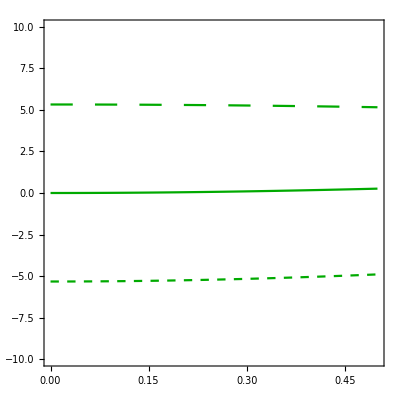
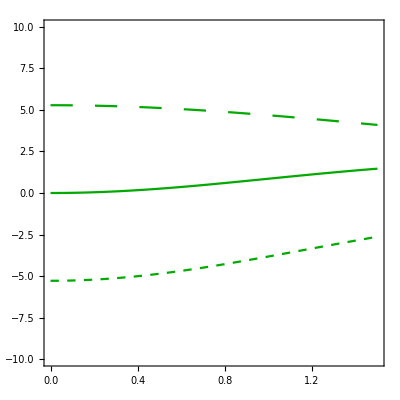
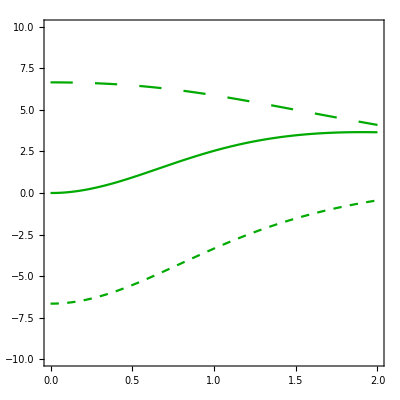
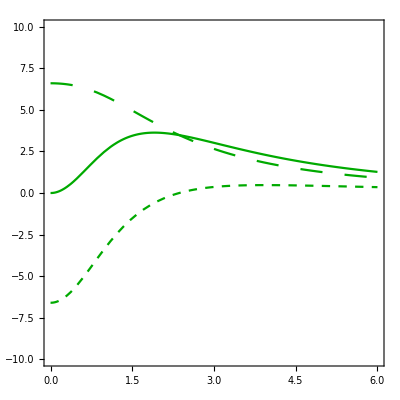
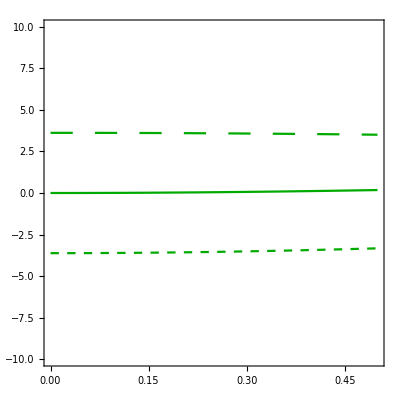
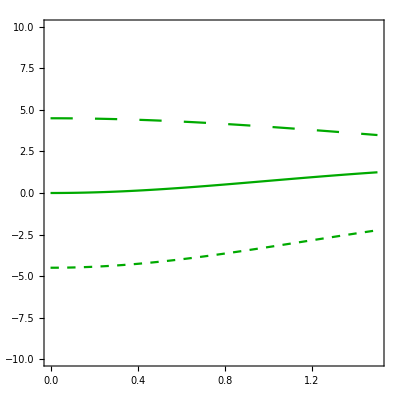
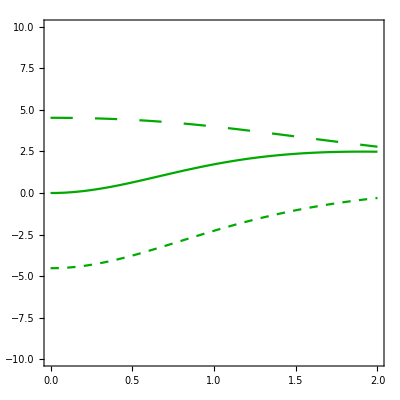
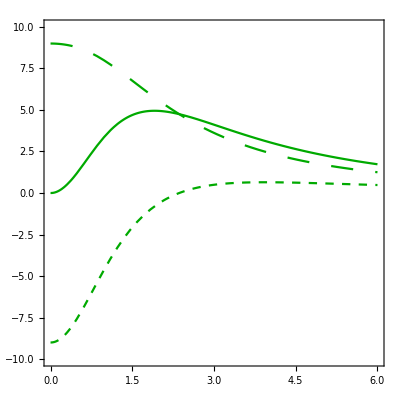
-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  | -Graphics- |

```mathematica
Block[{SLL=1/2},PlotAll[2dσCfset,Ucolors, Yrange,YNorms]]
```

```mathematica
(*Legends*)
```

```mathematica
legend=LineLegend[Ucolors,{MaTeX["d\\sigma^{T}_{UU}"],MaTeX["{\\bf I}[ f_1 \circledast D_{1}] \\;"],MaTeX["S_{LL}{\\bf I}[f_1 \circledast D_{1LL}] \\;"]},LegendLayout->"Row"]
```

```mathematica
TFFfig=Grid[{{MaTeX["\\mathcal{N}\\frac{d\\sigma}{d{\\bf P}_\\perp^2}\\; {\\rm [pb/GeV^2]},\\; \\sqrt{s}=63 \\; \\rm GeV"]},{legend},{Block[{SLL=1/2},PlotAll[2dσCfset,Ucolors, Yrange,YNorms]]}}]
```

InterpolatingFunction::dmval: Input value {0.0000102143} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  | -Graphics- |

#### Logitudinally Polarized J/ψ

```mathematica
(*Interpolating data*)
```

```mathematica
dσCsetinterp[i_,j_] := Interpolation[dσCset[[i,j]]][PT]
```

```mathematica
dσCfset = Table[dσCsetinterp[i,j],{i,1,Length[dσCset]},{j,1,Length[dσCset[[1]]]}];
```

```mathematica
Lrange = {All, {-1,15}};
```

```mathematica
(*Plots of longitudinally polarized J/ψ*)
```

```mathematica
Ucolors = {Purple,{Purple,Dashing[.04]}, {Purple,Dashing[.015]}};
```

InterpolatingFunction::dmval: Input value {0.0000102143} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

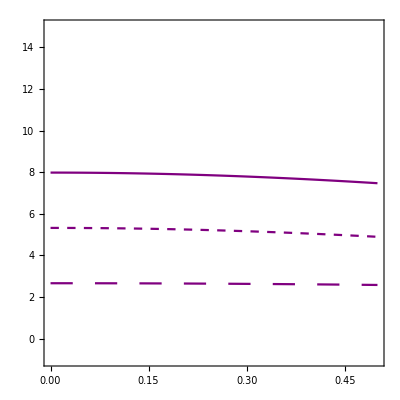
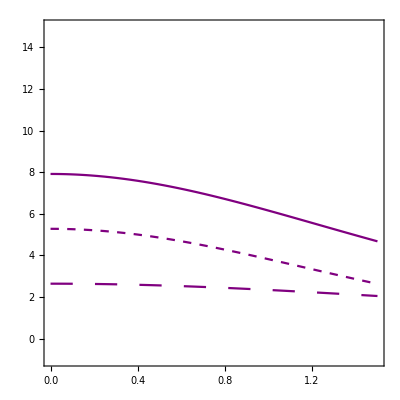
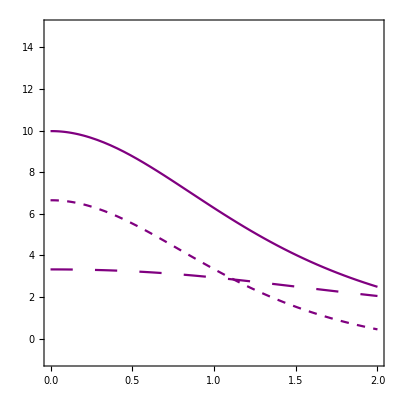
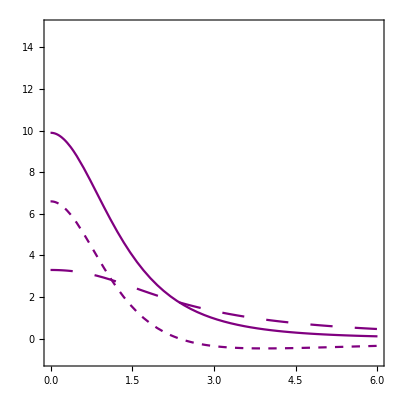
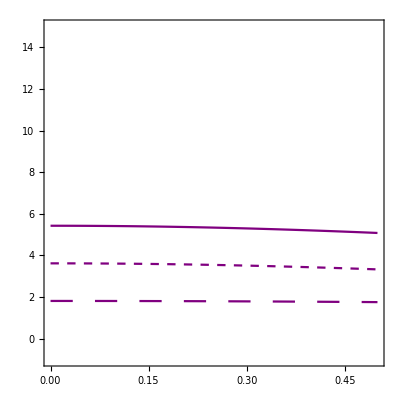
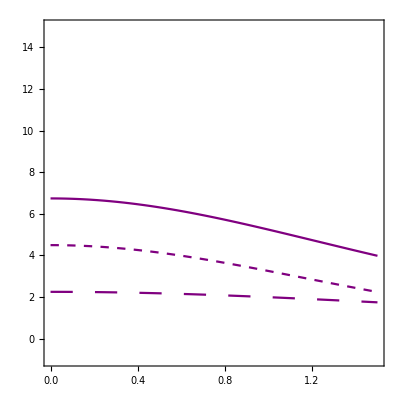
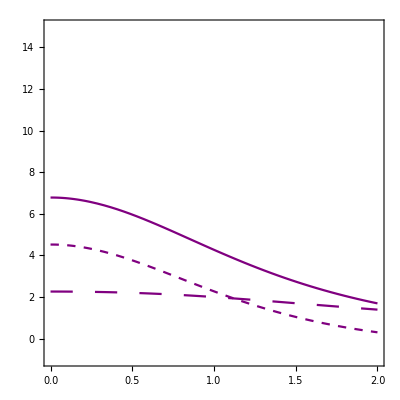
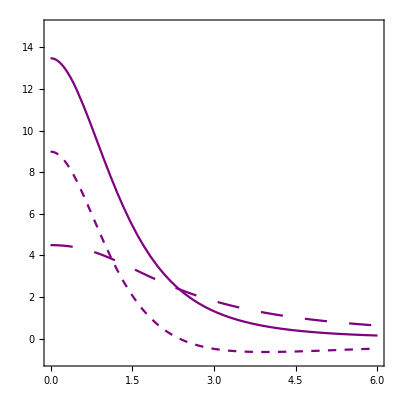
-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  | -Graphics- |

```mathematica
Block[{SLL=-1},PlotAll[dσCfset,Ucolors, Lrange,YNorms]]
```

```mathematica
(*Legend*)
```

```mathematica
legend=LineLegend[Ucolors,{MaTeX["d\\sigma^{L}_{UU}"],MaTeX["{\\bf I}[ f_1 \circledast D_{1}] \\;"],MaTeX["S_{LL}{\\bf I}[f_1 \circledast D_{1LL}] \\;"]},LegendLayout->"Row"]
```

```mathematica
LFFfig=Grid[{{MaTeX["\\mathcal{N}\\frac{d\\sigma}{d{\\bf P}_\\perp^2}\\; {\\rm [pb/GeV^2]},\\; \\sqrt{s}=63 \\; \\rm GeV"]},{legend},{Block[{SLL=-1},PlotAll[dσCfset,Ucolors, Lrange,YNorms]]}}]
```

InterpolatingFunction::dmval: Input value {0.0000102143} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  | -Graphics- |

#### All Polarized J/ψ

```mathematica
(*Preparing data to show only unpolarized J/ψ*)
```

```mathematica
dσCsettot = {Bin1listFFC,Bin2listFFC,Bin3listFFC,Bin4listFFC,Bin5listFFC,Bin6listFFC,Bin7listFFC,Bin8listFFC};
```

```mathematica
(*Interpolaring data*)
```

```mathematica
dσCsetinterptot[i_] := Interpolation[dσCsettot[[i]]][PT]
```

```mathematica
dσCfsettot  = Table[{(dσCsetinterptot[i]/.{SLL-> -1})+2*dσCsetinterptot[i]/.{SLL-> 1/2},dσCsetinterptot[i]/.{SLL-> -1},2dσCsetinterptot[i]/.{SLL-> 1/2}},{i,1,Length[dσCsettot ]}];
```

```mathematica
Totrange = {All, {0,15}};
```

```mathematica
Ucolors = {Blue,{Lighter[Purple],Dashed},{Darker[Green],Dashed}};
```

```mathematica
(*Unpolarized cross sections with logitudinal and transverse contributions*)
```

InterpolatingFunction::dmval: Input value {0.0000102143} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

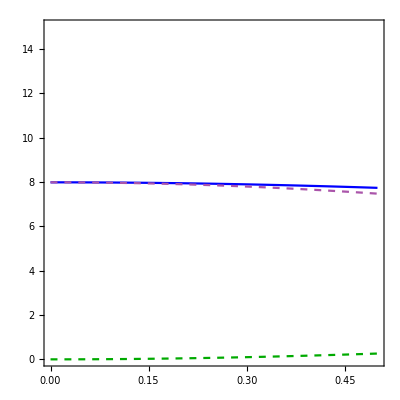
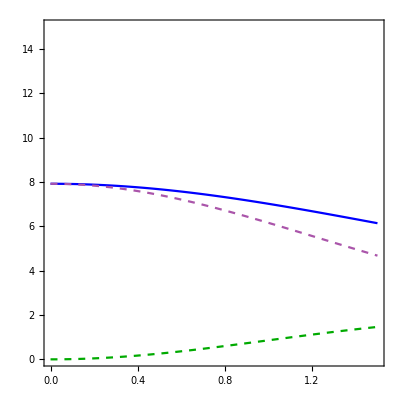
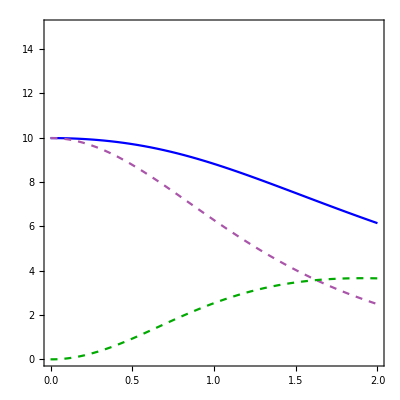
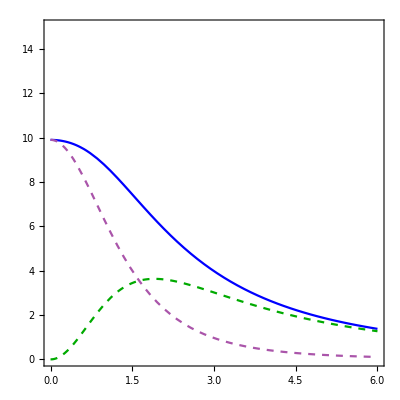
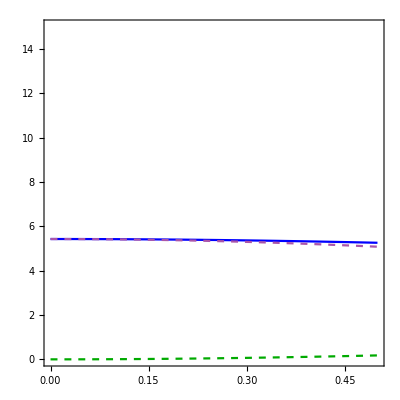
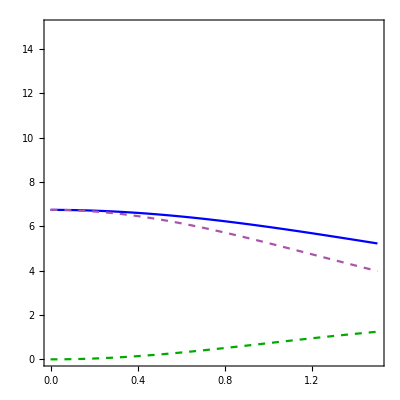
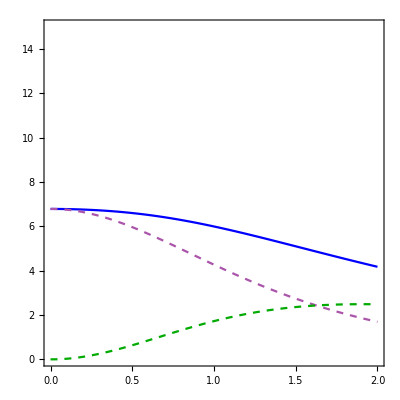
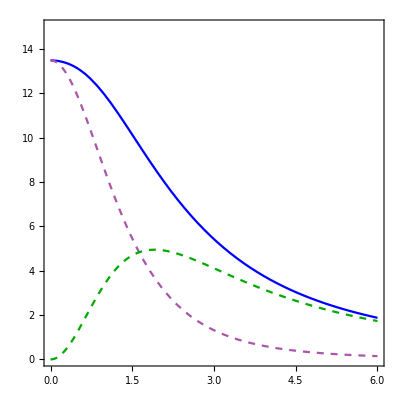
-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  | -Graphics- |

```mathematica
PlotAll[dσCfsettot,Ucolors, Totrange,YNorms]
```

```mathematica
legend=LineLegend[Ucolors,{MaTeX["{\\rm Unpolarized}"],MaTeX["{\\rm Longitudinal}"],MaTeX["{\\rm Transverse}"]},LegendLayout->"Row"]
```

InterpolatingFunction::dmval: Input value {0.0000102143} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

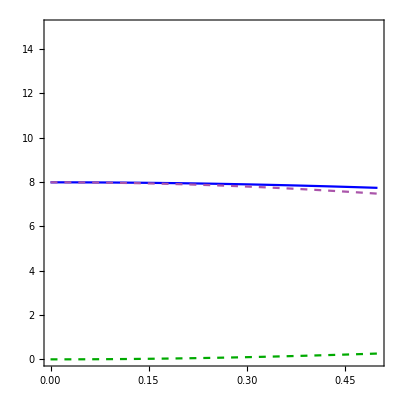
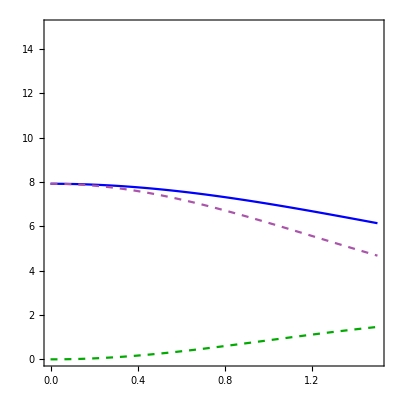
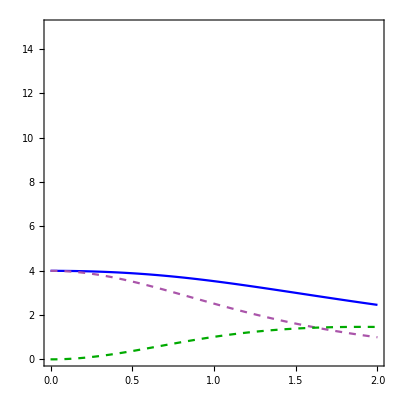
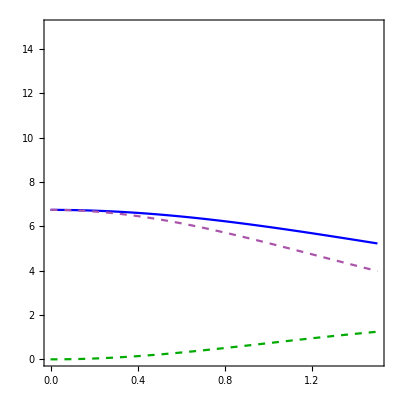
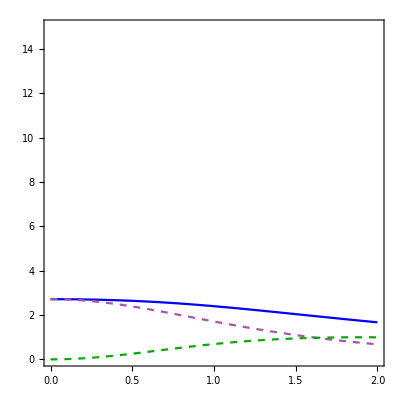
-Graphics-

-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  | -Graphics- |

```mathematica
TotFFfig=Grid[{{MaTeX["\\mathcal{N}\\frac{d\\sigma}{d{\\bf P}_\\perp^2}\\; {\\rm [pb/GeV^2]},\\; \\sqrt{s}=63 \\; \\rm GeV"]},{legend},{PlotAll[dσCfsettot,Ucolors, Totrange,YNorms]}}]
```

### dσ_LLPlots

#### Formatting plots for dσ_LL

```mathematica
(*Formatting plots in the style used for the Subscript[dσ, LL] figure*)
```

```mathematica
PlotAllLL[CS_,Color_, Range_,Norm_]:= Module[{P1,P2,P3,P4,P5,P6,P7,P8,grid},
SetOptions[MaTeX,Magnification->1.2];
SetOptions[Plot,AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->12},Frame->True,FrameStyle->Black,PlotRange->{-0.5,15},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green]},ImageSize->200];
normlabels={MaTeX["\\mathcal{N} =2\\times 10^5"],MaTeX["\\mathcal{N} = 2 \\times 10^7"],MaTeX["\\mathcal{N} = 2\\times 10^5"],MaTeX["\\mathcal{N} = 5 \\times 10^7"],MaTeX["\\mathcal{N} = 5 \\times 10^6"],MaTeX["\\mathcal{N} = 5 \\times 10^7"],MaTeX["\\mathcal{N} = 2 \\times 10^7"],MaTeX["\\mathcal{N} = 2 \\times 10^8"]};
padding={{15,5},{15,5}};

ImScale= {{ImageScaled[{0.95,0.3}],ImageScaled[{1,1}]},{ImageScaled[{0.95,0.3}],ImageScaled[{1,1}]},{ImageScaled[{0.95,0.3}],ImageScaled[{1,1}]},{ImageScaled[{0.95,0.3}],ImageScaled[{1,1}]},{ImageScaled[{0.95,0.85}],ImageScaled[{1,1}]},{ImageScaled[{0.95,0.85}],ImageScaled[{1,1}]},{ImageScaled[{0.95,0.85}],ImageScaled[{1,1}]},{ImageScaled[{0.95,0.85}],ImageScaled[{1,1}]}};
epilog[i_]:=Inset[normlabels[[i]],Evaluate[ImScale[[i,1]]],ImScale[[i,2]]];

leftonly={Automatic,Directive[FontOpacity->0,FontSize->0]};
noticks=Directive[FontOpacity->0,FontSize->0];
leftandbottom=Automatic;
bottomonly={Directive[FontOpacity->0,FontSize->0],Automatic};
ticksArray[i_]:={leftonly,noticks,noticks,noticks,leftandbottom,bottomonly,bottomonly,bottomonly}[[i]];

P1=Plot[Evaluate[Norm[[1]]CS[[1]]],{PT,0,.5},PlotStyle->Color,PlotRange-> Range,Epilog-> epilog[1],FrameTicksStyle->ticksArray[1],ImagePadding->padding];
P2= Plot[Evaluate[Norm[[2]]CS[[2]]],{PT,0,1.5},PlotStyle->Color,PlotRange-> Range,Epilog-> epilog[2],FrameTicksStyle->ticksArray[2],ImagePadding->padding];
P3 = Plot[Evaluate[Norm[[3]] CS[[3]]],{PT,0,2},PlotStyle->Color,PlotRange-> Range,Epilog-> epilog[3],FrameTicksStyle->ticksArray[3],ImagePadding->padding];
P4=Plot[Evaluate[Norm[[4]] CS[[4]]],{PT,0,6},PlotStyle->Color,PlotRange-> Range,Epilog-> epilog[4],FrameTicksStyle->ticksArray[4],ImagePadding->padding];
P5 = Plot[Evaluate[Norm[[5]] CS[[5]]],{PT,0,.5},PlotStyle->Color,PlotRange-> Range,Epilog-> epilog[5],FrameTicksStyle->ticksArray[5],ImagePadding->padding]; 
P6 = Plot[Evaluate[Norm[[6]] CS[[6]]],{PT,0,1.5},PlotStyle->Color,PlotRange-> Range,Epilog-> epilog[6],FrameTicksStyle->ticksArray[6],ImagePadding->padding];
P7 = Plot[Evaluate[Norm[[7]] CS[[7]]],{PT,0,2},PlotStyle->Color,PlotRange-> Range,Epilog-> epilog[7],FrameTicksStyle->ticksArray[7],ImagePadding->padding];
P8 = Plot[Evaluate[Norm[[8]] CS[[8]]],{PT,0,6},PlotStyle->Color,PlotRange-> Range,Epilog-> epilog[8],FrameTicksStyle->ticksArray[8],ImagePadding->padding];

grid=Grid[{{MaTeX["z\\in[0.1,0.4], \\; Q\\in[10,30]"],MaTeX["z\\in[0.1,0.4], \\; Q\\in[30,50]"],MaTeX["z\\in[0.4,0.8], \\; Q\\in[10,30]"],MaTeX["z\\in[0.4,0.8], \\; Q\\in[30,50]"],""},{P1,P2,P3,P4,Rotate[MaTeX["x\\in[0.1,0.5]"],-90Degree]},{P5,P6,P7,P8,Rotate[MaTeX["x\\in[0.5,1.0]"],-90Degree]},{"","","",MaTeX["\\; \\; \\; \\;  {\\bf P}_\\perp \\; \\rm [GeV]"],""}},Spacings->{0,0}]
]
```

```mathematica
OF = 1;
```

```mathematica
(*LL Normalizations*)
N1LL = OF*2*10^5/(2.56819*10^(-9));
N2LL =OF*2*10^7/(2.56819*10^(-9));
N3LL =OF*2*10^5/(2.56819*10^(-9));
N4LL =OF* 5*10^7/(2.56819*10^(-9));
N5LL = OF*5*10^6/(2.56819*10^(-9));
N6LL = OF*5*10^7/(2.56819*10^(-9));
N7LL =OF* 2*10^7/(2.56819*10^(-9));
N8LL = OF*2*10^8/(2.56819*10^(-9));
```

```mathematica
Yrange = {All, {-5,5}};
```

```mathematica
YNormsLL = {N1LL,N2LL,N3LL,N4LL,N5LL,N6LL,N7LL,N8LL};
```

#### Transversely Polarized J/ψ

```mathematica
(*Interpolating LL data*)
```

```mathematica
dσCsetinterpLL[i_,j_] := Interpolation[dσCsetLL[[i,j]]][PT]
```

```mathematica
dσCfsetLL = Table[dσCsetinterpLL[i,j],{i,1,Length[dσCsetLL]},{j,1,Length[dσCsetLL[[1]]]}]
```

{{InterpolatingFunction[…][PT],InterpolatingFunction[…][PT],InterpolatingFunction[…][PT]},{InterpolatingFunction[…][PT],InterpolatingFunction[…][PT],InterpolatingFunction[…][PT]},{InterpolatingFunction[…][PT],InterpolatingFunction[…][PT],InterpolatingFunction[…][PT]},{InterpolatingFunction[…][PT],InterpolatingFunction[…][PT],InterpolatingFunction[…][PT]},{InterpolatingFunction[…][PT],InterpolatingFunction[…][PT],InterpolatingFunction[…][PT]},{InterpolatingFunction[…][PT],InterpolatingFunction[…][PT],InterpolatingFunction[…][PT]},{InterpolatingFunction[…][PT],InterpolatingFunction[…][PT],InterpolatingFunction[…][PT]},{InterpolatingFunction[…][PT],InterpolatingFunction[…][PT],InterpolatingFunction[…][PT]}}

```mathematica
Ucolors = {Darker[Green],{Gray,Dashed}, {Black,Dotted}};
```

InterpolatingFunction::dmval: Input value {0.0000102143} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

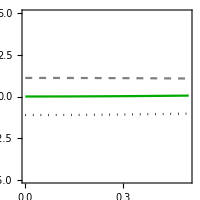
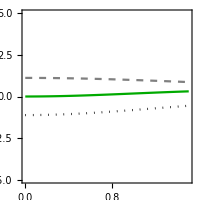
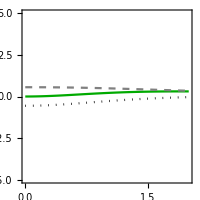
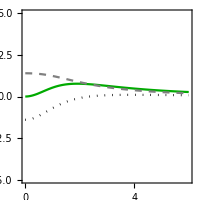
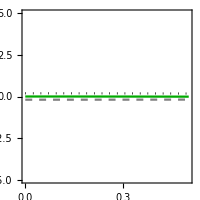
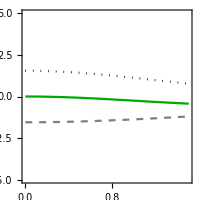
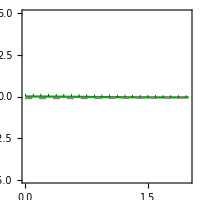
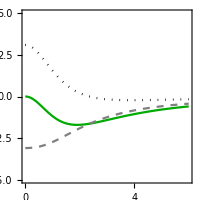
-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  | -Graphics- |

```mathematica
Block[{SLL=1/2},PlotAllLL[2dσCfsetLL,Ucolors, Yrange,YNorms]]
```

```mathematica
legend=LineLegend[Ucolors,{MaTeX["d\\sigma^{T}_{LL}"],MaTeX["{\\bf I}[ g_{1L} \circledast D_{1}] \\;"],MaTeX["S_{LL}{\\bf I}[g_{1L} \circledast D_{1LL}] \\;"]},LegendLayout->"Row"]
```

```mathematica
TFFfig=Grid[{{MaTeX["\\mathcal{N}\\frac{d\\sigma}{d{\\bf P}_\\perp^2}\\; {\\rm [pb/GeV^2]},\\; \\sqrt{s}=63 \\; \\rm GeV"]},{legend},{Block[{SLL=1/2},PlotAllLL[2dσCfsetLL,Ucolors, Yrange,YNorms]]}}]
```

InterpolatingFunction::dmval: Input value {0.0000102143} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  | -Graphics- |

#### Logitudinally Polarized J/ψ

```mathematica
(*Interpolating LL data*)
```

```mathematica
dσCsetinterpLL[i_,j_] := Interpolation[dσCsetLL[[i,j]]][PT]
```

```mathematica
dσCfsetLL = Table[dσCsetinterpLL[i,j],{i,1,Length[dσCsetLL]},{j,1,Length[dσCsetLL[[1]]]}]
```

{{InterpolatingFunction[…][PT],InterpolatingFunction[…][PT],InterpolatingFunction[…][PT]},{InterpolatingFunction[…][PT],InterpolatingFunction[…][PT],InterpolatingFunction[…][PT]},{InterpolatingFunction[…][PT],InterpolatingFunction[…][PT],InterpolatingFunction[…][PT]},{InterpolatingFunction[…][PT],InterpolatingFunction[…][PT],InterpolatingFunction[…][PT]},{InterpolatingFunction[…][PT],InterpolatingFunction[…][PT],InterpolatingFunction[…][PT]},{InterpolatingFunction[…][PT],InterpolatingFunction[…][PT],InterpolatingFunction[…][PT]},{InterpolatingFunction[…][PT],InterpolatingFunction[…][PT],InterpolatingFunction[…][PT]},{InterpolatingFunction[…][PT],InterpolatingFunction[…][PT],InterpolatingFunction[…][PT]}}

```mathematica
Lrange = {All, {-5,5}};
```

```mathematica
Ucolors = {Purple,{Lighter[Red],Dashed}, {Orange,Dashed}};
```

InterpolatingFunction::dmval: Input value {0.0000102143} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

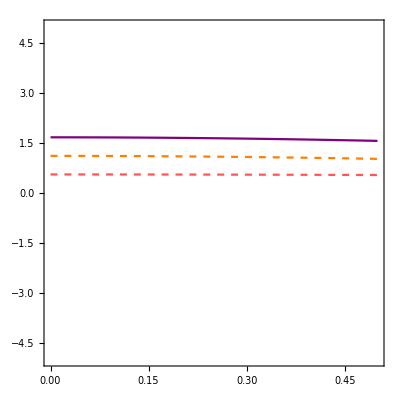
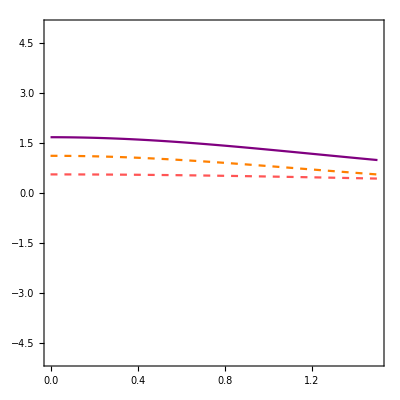
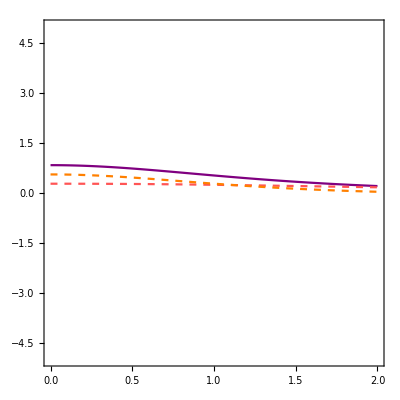
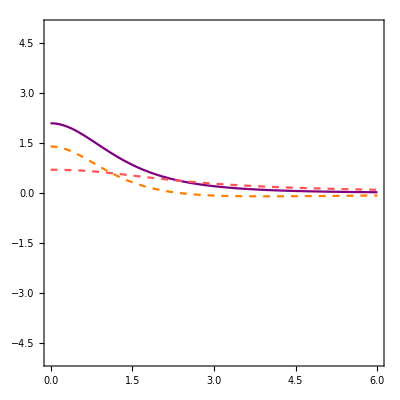
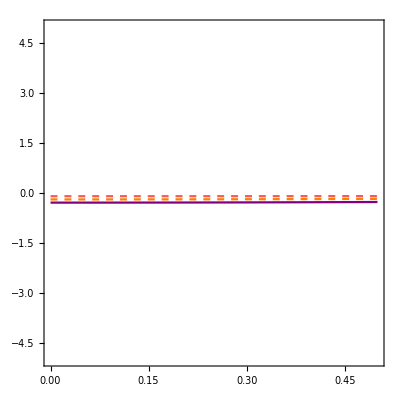
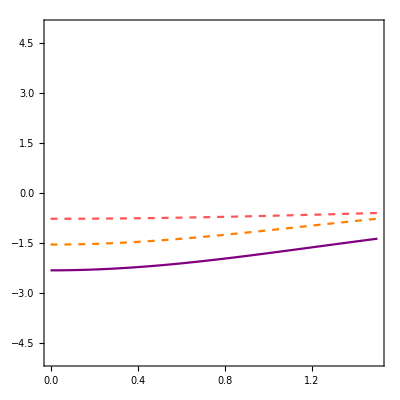
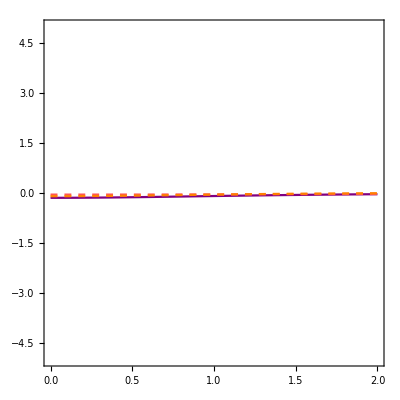
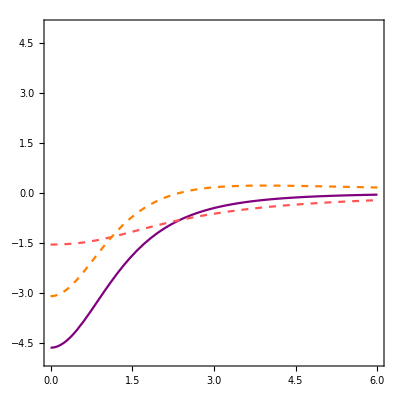
-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  | -Graphics- |

```mathematica
Block[{SLL=-1},PlotAllLL[dσCfsetLL,Ucolors, Lrange,YNorms]]
```

```mathematica
legend=LineLegend[Ucolors,{MaTeX["d\\sigma^{L}_{UU}"],MaTeX["{\\bf I}[ f_1 \circledast D_{1LL}] \\;"],MaTeX["S_{LL}{\\bf I}[f_1 \circledast D_1] \\;"]},LegendLayout->"Row"]
```

InterpolatingFunction::dmval: Input value {0.0000102143} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

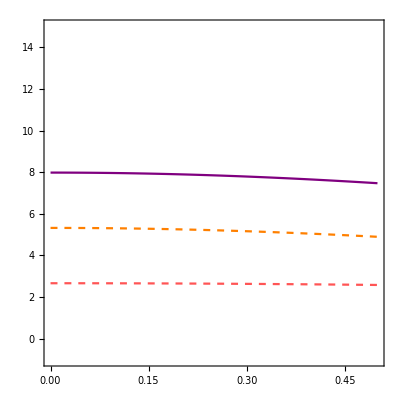
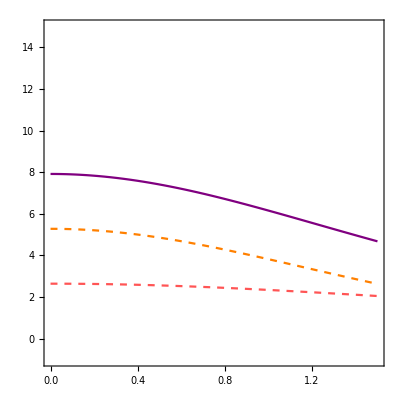
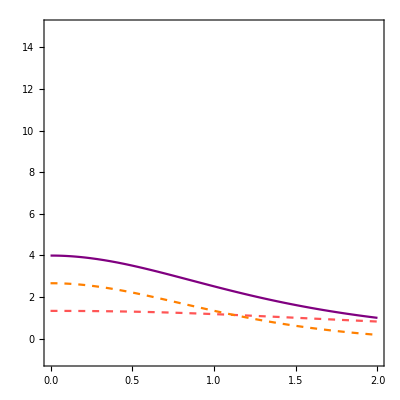
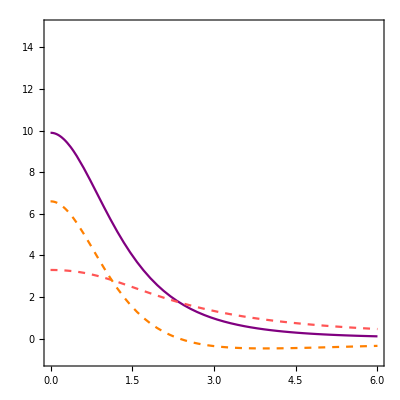
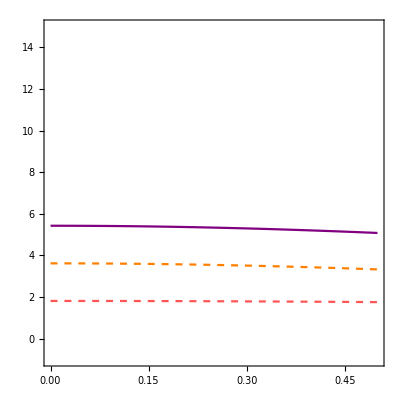
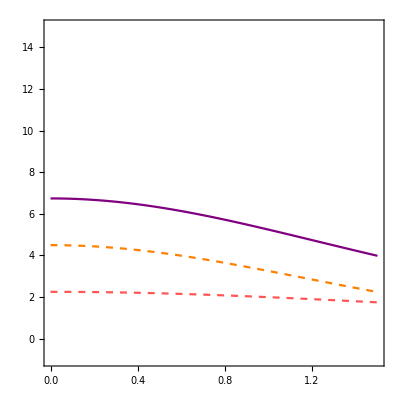
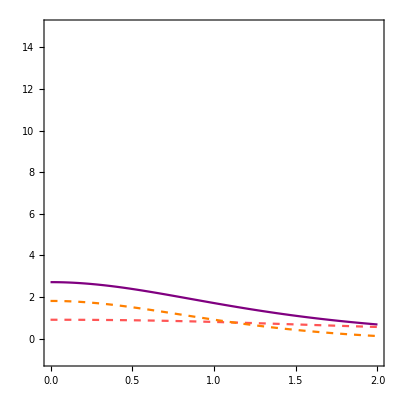
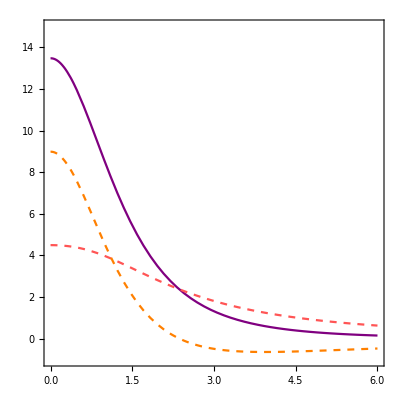
-Graphics-

-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  | -Graphics- |

```mathematica
LFFfig=Grid[{{MaTeX["\\mathcal{N}\\frac{d\\sigma}{d{\\bf P}_\\perp^2}\\; {\\rm [pb/GeV^2]},\\; \\sqrt{s}=63 \\; \\rm GeV"]},{legend},{Block[{SLL=-1},PlotAllLL[dσCfset,Ucolors, Lrange,YNorms]]}}]
```

#### All Polarized J/ψ

```mathematica
(*Preparing data to show total Subscript[dσ, LL] cross section*)
```

```mathematica
dσCsettotLL = {Bin1listFFCLL,Bin2listFFCLL,Bin3listFFCLL,Bin4listFFCLL,Bin5listFFCLL,Bin6listFFCLL,Bin7listFFCLL,Bin8listFFCLL};
```

```mathematica
dσCsetinterptotLL[i_] := Interpolation[dσCsettotLL[[i]]][PT]
```

```mathematica
dσCfsettotLL  = Table[{(dσCsetinterptotLL[i]/.{SLL-> -1})+2*dσCsetinterptotLL[i]/.{SLL-> 1/2},dσCsetinterptotLL[i]/.{SLL-> -1},2dσCsetinterptotLL[i]/.{SLL-> 1/2}},{i,1,Length[dσCsettotLL ]}];
```

```mathematica
Totrange = {All, {-5,5}};
```

```mathematica
Ucolors = {Blue,{Lighter[Purple],Dashed},{Darker[Green],Dashed}};
```

```mathematica
(*Plot of Subscript[dσ, LL] cross sections with contributions from longitudinally and transversely polarized J/ψ*)
```

InterpolatingFunction::dmval: Input value {0.0000102143} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

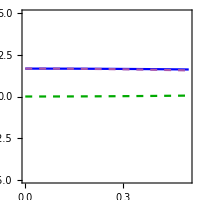
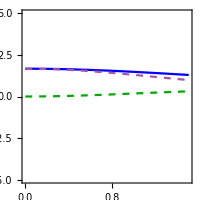
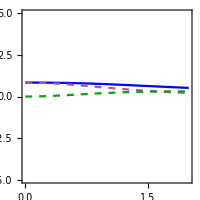
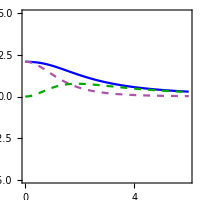
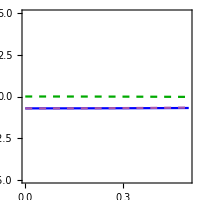
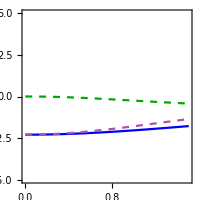
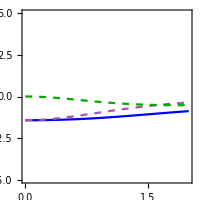
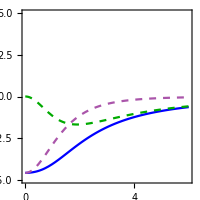
-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  | -Graphics- |

```mathematica
PlotAllLL[dσCfsettotLL,Ucolors, Totrange,YNormsLL]
```

```mathematica
legend=LineLegend[Ucolors,{MaTeX["{\\rm Unpolarized}"],MaTeX["{\\rm Longitudinal}"],MaTeX["{\\rm Transverse}"]},LegendLayout->"Row"]
```

```mathematica
TotFFfigLL=Grid[{{MaTeX["\\mathcal{N}\\frac{d\\sigma_{LL}}{d{\\bf P}_\\perp^2}\\; {\\rm [pb/GeV^2]},\\; \\sqrt{s}=63 \\; \\rm GeV"]},{legend},{PlotAllLL[dσCfsettotLL,Ucolors, Totrange,YNormsLL]}}]
```

InterpolatingFunction::dmval: Input value {0.0000102143} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  | -Graphics- |